```mathematica
Exit
```

## xAct`xPert`

### Authors

© 2005-2018, under the GNU General Public License (GPL)

David Brizuela, david.brizuela@ehu.eus
José M. Martín-García, jose@xact.es
Guillermo A. Mena Marugán, mena@iem.cfmac.csic.es

### Intro

xPert` is a package for efficient construction and manipulation of high-order perturbations of the curvature tensors of a Riemannian manifold. Its main application is Perturbation Theory in General Relativity.
xPert` is part of the xAct` framework for Tensor Computer Algebra in Mathematica, and in particular it needs the underlying package xTensor` for abstract tensor manipulations.

### Load the package

This loads the package from the default directory, for example $HOME/.Mathematica/Applications/xAct/ for a single-user installation under Linux. xTensor` and xPerm` are automatically loaded.

```mathematica
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2015, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2018, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

The default options of MakeRule and ContractMetric have been changed:

```mathematica
Options[MakeRule]
```

{PatternIndices→All,TestIndices→True,MetricOn→All,UseSymmetries→True,Verbose→False,ContractMetrics→True,Evaluate→False}

```mathematica
Options[ContractMetric]
```

{AllowUpperDerivatives→True,OverDerivatives→False}

We also load the timing package and lower its default threshold of 1 second to 0.1 seconds

```mathematica
<<xAct`ShowTime1`
```

```mathematica
$ShowTimeThreshold=0.1;
```

We define a function to collect and canonicalize equal-order terms:

```mathematica
org[expr_]:=Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical]
```

## 0. Set up

xPert`  has been built on xTensor`  and shares its notation. Then, a session with xPert` begins just like one with xTensor`, defining one or more manifolds and vector bundles and the objects living on them:

Define a 4d manifold M. Note that most of the results will not depend on the chosen dimension.

```mathematica
DefManifold[M,4,{a,b,c,d,e,f}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

We also define a metric on this manifold, with negative determinant and associated covariant derivative CD. This derivative is extended to act on tensor densities defined using the determinant of the metric g in the basis AIndex:

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","D"},WeightedWithBasis->AIndex]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

0.365443

The absolute value of its determinant in the basis AIndex is obtained as

```mathematica
Determinant[g][]
```

g^OverTilde[~]

and it is actually called

```mathematica
InputForm[%]
```

Detg[]

By default, curvature tensors are output showing the name of the derivative they are associated to:

```mathematica
RiemannCD[-a,-b,-c,d]
```

R[D] |   |   |   | d
a | b | c |

Because we shall work with a single covariant derivative operator, we can choose a simpler output for the geometric tensors

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
```

so that now

```mathematica
RiemannCD[-a,-b,-c,d]
```

R |   |   |   | d
a | b | c |

After defining the background manifold in xTensor`, we now define the perturbative structure with the command DefMetricPerturbation of xPert`.

We define the symmetric two-tensor h that will be understood as the perturbation of the metric. As can be seen in the output, the first index of this tensor is a label index (LI), which will encode the perturbative order.

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor h[LI[order],-a,-b].

The perturbative parameter ϵ is stored in the global variable

```mathematica
$PerturbationParameter
```

ϵ

Finally, we colour in blue the perturbative orders

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
IndexForm[LI[n]]
```

n

## 1. Perturbations of the metric and fundamental properties

The main objective of xPert` is giving the n-th perturbation of any object in terms of metric perturbations of order n and lower. Here we introduce the Perturbation head and give examples of use of different perturbative orders. For those readers already familiar with xTensor`, let us point out that the symbol Perturbation is a linear inert-head.

The perturbation of the metric is represented as follows:

```mathematica
Perturbation[ g[-a,-b] ]
```

h | 1 |   |  
  | a | b

Perturbation has actually two argumens in general. The first one is the expression we want to perturb and the second one the perturbative order (with default 1 when it is not specified, as in the previous case). For instance, acting on the metric at fifth perturbative order returns

```mathematica
Perturbation[g[-a,-b],5]
```

h | 5 |   |  
  | a | b

Or on the perturbed tensor itself,

```mathematica
Perturbation[h[LI[3],-a,-b],5]
```

h | 8 |   |  
  | a | b

It also knows how to act on a Kronecker delta

```mathematica
Perturbation[delta[a,-b],3]
```

0

Perturbation uses the fundamental properties of a derivative: linearity and Leibnitz rule. When it does not know the answer of the action on a given tensor, for example the inverse of the metric or the Ricci tensor, the head Perturbation is kept (this is where its inert-head character plays a role):

```mathematica
Perturbation[g[-a,-b]+g[c,d]RicciCD[-a,-c]RicciCD[-d,-b]]
```

h | 1 |   |  
  | a | b+g | c | d
  |   △[R |   |  
d | b] R |   |  
a | c+g | c | d
  |   △[R |   |  
a | c] R |   |  
d | b+△[g | c | d
  |  ] R |   |  
a | c R |   |  
d | b

We can consider the same case but at a higher perturbative order, for instance at seveteenth order and see that the calculation is almost immediate.

```mathematica
Perturbation[g[-a,-b]+g[c,d]RicciCD[-a,-c]RicciCD[-d,-b],17]
```

h | 17 |   |  
  | a | b+272 △[R |   |  
a | c] △[R |   |  
d | b] △^15[g | c | d
  |  ]+2040 △[R |   |  
d | b] △^14[g | c | d
  |  ] △^2[R |   |  
a | c]+9520 △[R |   |  
d | b] △^13[g | c | d
  |  ] △^3[R |   |  
a | c]+30940 △[R |   |  
d | b] △^12[g | c | d
  |  ] △^4[R |   |  
a | c]+74256 △[R |   |  
d | b] △^11[g | c | d
  |  ] △^5[R |   |  
a | c]+136136 △[R |   |  
d | b] △^10[g | c | d
  |  ] △^6[R |   |  
a | c]+194480 △[R |   |  
d | b] △^9[g | c | d
  |  ] △^7[R |   |  
a | c]+218790 △[R |   |  
d | b] △^8[g | c | d
  |  ] △^8[R |   |  
a | c]+194480 △[R |   |  
d | b] △^7[g | c | d
  |  ] △^9[R |   |  
a | c]+136136 △[R |   |  
d | b] △^6[g | c | d
  |  ] △^10[R |   |  
a | c]+74256 △[R |   |  
d | b] △^5[g | c | d
  |  ] △^11[R |   |  
a | c]+30940 △[R |   |  
d | b] △^4[g | c | d
  |  ] △^12[R |   |  
a | c]+9520 △[R |   |  
d | b] △^3[g | c | d
  |  ] △^13[R |   |  
a | c]+2040 △[R |   |  
d | b] △^2[g | c | d
  |  ] △^14[R |   |  
a | c]+272 △[g | c | d
  |  ] △[R |   |  
d | b] △^15[R |   |  
a | c]+17 g | c | d
  |   △[R |   |  
d | b] △^16[R |   |  
a | c]+2040 △[R |   |  
a | c] △^14[g | c | d
  |  ] △^2[R |   |  
d | b]+14280 △^13[g | c | d
  |  ] △^2[R |   |  
a | c] △^2[R |   |  
d | b]+61880 △^12[g | c | d
  |  ] △^3[R |   |  
a | c] △^2[R |   |  
d | b]+185640 △^11[g | c | d
  |  ] △^4[R |   |  
a | c] △^2[R |   |  
d | b]+408408 △^10[g | c | d
  |  ] △^5[R |   |  
a | c] △^2[R |   |  
d | b]+680680 △^9[g | c | d
  |  ] △^6[R |   |  
a | c] △^2[R |   |  
d | b]+875160 △^8[g | c | d
  |  ] △^7[R |   |  
a | c] △^2[R |   |  
d | b]+875160 △^7[g | c | d
  |  ] △^8[R |   |  
a | c] △^2[R |   |  
d | b]+680680 △^6[g | c | d
  |  ] △^9[R |   |  
a | c] △^2[R |   |  
d | b]+408408 △^5[g | c | d
  |  ] △^10[R |   |  
a | c] △^2[R |   |  
d | b]+185640 △^4[g | c | d
  |  ] △^11[R |   |  
a | c] △^2[R |   |  
d | b]+61880 △^3[g | c | d
  |  ] △^12[R |   |  
a | c] △^2[R |   |  
d | b]+14280 △^2[g | c | d
  |  ] △^13[R |   |  
a | c] △^2[R |   |  
d | b]+2040 △[g | c | d
  |  ] △^14[R |   |  
a | c] △^2[R |   |  
d | b]+136 g | c | d
  |   △^15[R |   |  
a | c] △^2[R |   |  
d | b]+9520 △[R |   |  
a | c] △^13[g | c | d
  |  ] △^3[R |   |  
d | b]+61880 △^12[g | c | d
  |  ] △^2[R |   |  
a | c] △^3[R |   |  
d | b]+247520 △^11[g | c | d
  |  ] △^3[R |   |  
a | c] △^3[R |   |  
d | b]+680680 △^10[g | c | d
  |  ] △^4[R |   |  
a | c] △^3[R |   |  
d | b]+1361360 △^9[g | c | d
  |  ] △^5[R |   |  
a | c] △^3[R |   |  
d | b]+2042040 △^8[g | c | d
  |  ] △^6[R |   |  
a | c] △^3[R |   |  
d | b]+2333760 △^7[g | c | d
  |  ] △^7[R |   |  
a | c] △^3[R |   |  
d | b]+2042040 △^6[g | c | d
  |  ] △^8[R |   |  
a | c] △^3[R |   |  
d | b]+1361360 △^5[g | c | d
  |  ] △^9[R |   |  
a | c] △^3[R |   |  
d | b]+680680 △^4[g | c | d
  |  ] △^10[R |   |  
a | c] △^3[R |   |  
d | b]+247520 △^3[g | c | d
  |  ] △^11[R |   |  
a | c] △^3[R |   |  
d | b]+61880 △^2[g | c | d
  |  ] △^12[R |   |  
a | c] △^3[R |   |  
d | b]+9520 △[g | c | d
  |  ] △^13[R |   |  
a | c] △^3[R |   |  
d | b]+680 g | c | d
  |   △^14[R |   |  
a | c] △^3[R |   |  
d | b]+30940 △[R |   |  
a | c] △^12[g | c | d
  |  ] △^4[R |   |  
d | b]+185640 △^11[g | c | d
  |  ] △^2[R |   |  
a | c] △^4[R |   |  
d | b]+680680 △^10[g | c | d
  |  ] △^3[R |   |  
a | c] △^4[R |   |  
d | b]+1701700 △^9[g | c | d
  |  ] △^4[R |   |  
a | c] △^4[R |   |  
d | b]+3063060 △^8[g | c | d
  |  ] △^5[R |   |  
a | c] △^4[R |   |  
d | b]+4084080 △^7[g | c | d
  |  ] △^6[R |   |  
a | c] △^4[R |   |  
d | b]+4084080 △^6[g | c | d
  |  ] △^7[R |   |  
a | c] △^4[R |   |  
d | b]+3063060 △^5[g | c | d
  |  ] △^8[R |   |  
a | c] △^4[R |   |  
d | b]+1701700 △^4[g | c | d
  |  ] △^9[R |   |  
a | c] △^4[R |   |  
d | b]+680680 △^3[g | c | d
  |  ] △^10[R |   |  
a | c] △^4[R |   |  
d | b]+185640 △^2[g | c | d
  |  ] △^11[R |   |  
a | c] △^4[R |   |  
d | b]+30940 △[g | c | d
  |  ] △^12[R |   |  
a | c] △^4[R |   |  
d | b]+2380 g | c | d
  |   △^13[R |   |  
a | c] △^4[R |   |  
d | b]+74256 △[R |   |  
a | c] △^11[g | c | d
  |  ] △^5[R |   |  
d | b]+408408 △^10[g | c | d
  |  ] △^2[R |   |  
a | c] △^5[R |   |  
d | b]+1361360 △^9[g | c | d
  |  ] △^3[R |   |  
a | c] △^5[R |   |  
d | b]+3063060 △^8[g | c | d
  |  ] △^4[R |   |  
a | c] △^5[R |   |  
d | b]+4900896 △^7[g | c | d
  |  ] △^5[R |   |  
a | c] △^5[R |   |  
d | b]+5717712 △^6[g | c | d
  |  ] △^6[R |   |  
a | c] △^5[R |   |  
d | b]+4900896 △^5[g | c | d
  |  ] △^7[R |   |  
a | c] △^5[R |   |  
d | b]+3063060 △^4[g | c | d
  |  ] △^8[R |   |  
a | c] △^5[R |   |  
d | b]+1361360 △^3[g | c | d
  |  ] △^9[R |   |  
a | c] △^5[R |   |  
d | b]+408408 △^2[g | c | d
  |  ] △^10[R |   |  
a | c] △^5[R |   |  
d | b]+74256 △[g | c | d
  |  ] △^11[R |   |  
a | c] △^5[R |   |  
d | b]+6188 g | c | d
  |   △^12[R |   |  
a | c] △^5[R |   |  
d | b]+136136 △[R |   |  
a | c] △^10[g | c | d
  |  ] △^6[R |   |  
d | b]+680680 △^9[g | c | d
  |  ] △^2[R |   |  
a | c] △^6[R |   |  
d | b]+2042040 △^8[g | c | d
  |  ] △^3[R |   |  
a | c] △^6[R |   |  
d | b]+4084080 △^7[g | c | d
  |  ] △^4[R |   |  
a | c] △^6[R |   |  
d | b]+5717712 △^6[g | c | d
  |  ] △^5[R |   |  
a | c] △^6[R |   |  
d | b]+5717712 △^5[g | c | d
  |  ] △^6[R |   |  
a | c] △^6[R |   |  
d | b]+4084080 △^4[g | c | d
  |  ] △^7[R |   |  
a | c] △^6[R |   |  
d | b]+2042040 △^3[g | c | d
  |  ] △^8[R |   |  
a | c] △^6[R |   |  
d | b]+680680 △^2[g | c | d
  |  ] △^9[R |   |  
a | c] △^6[R |   |  
d | b]+136136 △[g | c | d
  |  ] △^10[R |   |  
a | c] △^6[R |   |  
d | b]+12376 g | c | d
  |   △^11[R |   |  
a | c] △^6[R |   |  
d | b]+194480 △[R |   |  
a | c] △^9[g | c | d
  |  ] △^7[R |   |  
d | b]+875160 △^8[g | c | d
  |  ] △^2[R |   |  
a | c] △^7[R |   |  
d | b]+2333760 △^7[g | c | d
  |  ] △^3[R |   |  
a | c] △^7[R |   |  
d | b]+4084080 △^6[g | c | d
  |  ] △^4[R |   |  
a | c] △^7[R |   |  
d | b]+4900896 △^5[g | c | d
  |  ] △^5[R |   |  
a | c] △^7[R |   |  
d | b]+4084080 △^4[g | c | d
  |  ] △^6[R |   |  
a | c] △^7[R |   |  
d | b]+2333760 △^3[g | c | d
  |  ] △^7[R |   |  
a | c] △^7[R |   |  
d | b]+875160 △^2[g | c | d
  |  ] △^8[R |   |  
a | c] △^7[R |   |  
d | b]+194480 △[g | c | d
  |  ] △^9[R |   |  
a | c] △^7[R |   |  
d | b]+19448 g | c | d
  |   △^10[R |   |  
a | c] △^7[R |   |  
d | b]+218790 △[R |   |  
a | c] △^8[g | c | d
  |  ] △^8[R |   |  
d | b]+875160 △^7[g | c | d
  |  ] △^2[R |   |  
a | c] △^8[R |   |  
d | b]+2042040 △^6[g | c | d
  |  ] △^3[R |   |  
a | c] △^8[R |   |  
d | b]+3063060 △^5[g | c | d
  |  ] △^4[R |   |  
a | c] △^8[R |   |  
d | b]+3063060 △^4[g | c | d
  |  ] △^5[R |   |  
a | c] △^8[R |   |  
d | b]+2042040 △^3[g | c | d
  |  ] △^6[R |   |  
a | c] △^8[R |   |  
d | b]+875160 △^2[g | c | d
  |  ] △^7[R |   |  
a | c] △^8[R |   |  
d | b]+218790 △[g | c | d
  |  ] △^8[R |   |  
a | c] △^8[R |   |  
d | b]+24310 g | c | d
  |   △^9[R |   |  
a | c] △^8[R |   |  
d | b]+194480 △[R |   |  
a | c] △^7[g | c | d
  |  ] △^9[R |   |  
d | b]+680680 △^6[g | c | d
  |  ] △^2[R |   |  
a | c] △^9[R |   |  
d | b]+1361360 △^5[g | c | d
  |  ] △^3[R |   |  
a | c] △^9[R |   |  
d | b]+1701700 △^4[g | c | d
  |  ] △^4[R |   |  
a | c] △^9[R |   |  
d | b]+1361360 △^3[g | c | d
  |  ] △^5[R |   |  
a | c] △^9[R |   |  
d | b]+680680 △^2[g | c | d
  |  ] △^6[R |   |  
a | c] △^9[R |   |  
d | b]+194480 △[g | c | d
  |  ] △^7[R |   |  
a | c] △^9[R |   |  
d | b]+24310 g | c | d
  |   △^8[R |   |  
a | c] △^9[R |   |  
d | b]+136136 △[R |   |  
a | c] △^6[g | c | d
  |  ] △^10[R |   |  
d | b]+408408 △^5[g | c | d
  |  ] △^2[R |   |  
a | c] △^10[R |   |  
d | b]+680680 △^4[g | c | d
  |  ] △^3[R |   |  
a | c] △^10[R |   |  
d | b]+680680 △^3[g | c | d
  |  ] △^4[R |   |  
a | c] △^10[R |   |  
d | b]+408408 △^2[g | c | d
  |  ] △^5[R |   |  
a | c] △^10[R |   |  
d | b]+136136 △[g | c | d
  |  ] △^6[R |   |  
a | c] △^10[R |   |  
d | b]+19448 g | c | d
  |   △^7[R |   |  
a | c] △^10[R |   |  
d | b]+74256 △[R |   |  
a | c] △^5[g | c | d
  |  ] △^11[R |   |  
d | b]+185640 △^4[g | c | d
  |  ] △^2[R |   |  
a | c] △^11[R |   |  
d | b]+247520 △^3[g | c | d
  |  ] △^3[R |   |  
a | c] △^11[R |   |  
d | b]+185640 △^2[g | c | d
  |  ] △^4[R |   |  
a | c] △^11[R |   |  
d | b]+74256 △[g | c | d
  |  ] △^5[R |   |  
a | c] △^11[R |   |  
d | b]+12376 g | c | d
  |   △^6[R |   |  
a | c] △^11[R |   |  
d | b]+30940 △[R |   |  
a | c] △^4[g | c | d
  |  ] △^12[R |   |  
d | b]+61880 △^3[g | c | d
  |  ] △^2[R |   |  
a | c] △^12[R |   |  
d | b]+61880 △^2[g | c | d
  |  ] △^3[R |   |  
a | c] △^12[R |   |  
d | b]+30940 △[g | c | d
  |  ] △^4[R |   |  
a | c] △^12[R |   |  
d | b]+6188 g | c | d
  |   △^5[R |   |  
a | c] △^12[R |   |  
d | b]+9520 △[R |   |  
a | c] △^3[g | c | d
  |  ] △^13[R |   |  
d | b]+14280 △^2[g | c | d
  |  ] △^2[R |   |  
a | c] △^13[R |   |  
d | b]+9520 △[g | c | d
  |  ] △^3[R |   |  
a | c] △^13[R |   |  
d | b]+2380 g | c | d
  |   △^4[R |   |  
a | c] △^13[R |   |  
d | b]+2040 △[R |   |  
a | c] △^2[g | c | d
  |  ] △^14[R |   |  
d | b]+2040 △[g | c | d
  |  ] △^2[R |   |  
a | c] △^14[R |   |  
d | b]+680 g | c | d
  |   △^3[R |   |  
a | c] △^14[R |   |  
d | b]+272 △[g | c | d
  |  ] △[R |   |  
a | c] △^15[R |   |  
d | b]+136 g | c | d
  |   △^2[R |   |  
a | c] △^15[R |   |  
d | b]+17 g | c | d
  |   △[R |   |  
a | c] △^16[R |   |  
d | b]+17 △[R |   |  
d | b] △^16[g | c | d
  |  ] R |   |  
a | c+136 △^15[g | c | d
  |  ] △^2[R |   |  
d | b] R |   |  
a | c+680 △^14[g | c | d
  |  ] △^3[R |   |  
d | b] R |   |  
a | c+2380 △^13[g | c | d
  |  ] △^4[R |   |  
d | b] R |   |  
a | c+6188 △^12[g | c | d
  |  ] △^5[R |   |  
d | b] R |   |  
a | c+12376 △^11[g | c | d
  |  ] △^6[R |   |  
d | b] R |   |  
a | c+19448 △^10[g | c | d
  |  ] △^7[R |   |  
d | b] R |   |  
a | c+24310 △^9[g | c | d
  |  ] △^8[R |   |  
d | b] R |   |  
a | c+24310 △^8[g | c | d
  |  ] △^9[R |   |  
d | b] R |   |  
a | c+19448 △^7[g | c | d
  |  ] △^10[R |   |  
d | b] R |   |  
a | c+12376 △^6[g | c | d
  |  ] △^11[R |   |  
d | b] R |   |  
a | c+6188 △^5[g | c | d
  |  ] △^12[R |   |  
d | b] R |   |  
a | c+2380 △^4[g | c | d
  |  ] △^13[R |   |  
d | b] R |   |  
a | c+680 △^3[g | c | d
  |  ] △^14[R |   |  
d | b] R |   |  
a | c+136 △^2[g | c | d
  |  ] △^15[R |   |  
d | b] R |   |  
a | c+17 △[g | c | d
  |  ] △^16[R |   |  
d | b] R |   |  
a | c+g | c | d
  |   △^17[R |   |  
d | b] R |   |  
a | c+17 △[R |   |  
a | c] △^16[g | c | d
  |  ] R |   |  
d | b+136 △^15[g | c | d
  |  ] △^2[R |   |  
a | c] R |   |  
d | b+680 △^14[g | c | d
  |  ] △^3[R |   |  
a | c] R |   |  
d | b+2380 △^13[g | c | d
  |  ] △^4[R |   |  
a | c] R |   |  
d | b+6188 △^12[g | c | d
  |  ] △^5[R |   |  
a | c] R |   |  
d | b+12376 △^11[g | c | d
  |  ] △^6[R |   |  
a | c] R |   |  
d | b+19448 △^10[g | c | d
  |  ] △^7[R |   |  
a | c] R |   |  
d | b+24310 △^9[g | c | d
  |  ] △^8[R |   |  
a | c] R |   |  
d | b+24310 △^8[g | c | d
  |  ] △^9[R |   |  
a | c] R |   |  
d | b+19448 △^7[g | c | d
  |  ] △^10[R |   |  
a | c] R |   |  
d | b+12376 △^6[g | c | d
  |  ] △^11[R |   |  
a | c] R |   |  
d | b+6188 △^5[g | c | d
  |  ] △^12[R |   |  
a | c] R |   |  
d | b+2380 △^4[g | c | d
  |  ] △^13[R |   |  
a | c] R |   |  
d | b+680 △^3[g | c | d
  |  ] △^14[R |   |  
a | c] R |   |  
d | b+136 △^2[g | c | d
  |  ] △^15[R |   |  
a | c] R |   |  
d | b+17 △[g | c | d
  |  ] △^16[R |   |  
a | c] R |   |  
d | b+g | c | d
  |   △^17[R |   |  
a | c] R |   |  
d | b+△^17[g | c | d
  |  ] R |   |  
a | c R |   |  
d | b

The perturbative order of an expression can be computed with

```mathematica
PerturbationOrder[%]
```

17

By definition, Perturbation commutes with partial derivatives,

```mathematica
Perturbation[PD[-a][RicciCD[-c,-d]],5]
```

∂_a △^5[R |   |  
c | d]

and with covariant derivatives acting on scalars,

```mathematica
Perturbation[CD[-a][RicciScalarCD[]],6]
```

D_a△^6[R]

but not with covariant derivatives acting on tensors,

```mathematica
Perturbation[CD[-a][RicciCD[a,-b]],3]
```

△^3[R | a |   |   
  | b | ;a]

It is essential to have in mind that the ToCanonical or Simplification commands cannot be used as long as there is any Perturbation head in the expression because internal indices of the expression inside Perturbation could be moved improperly. A warning reminds us of the danger:

For example the expression

```mathematica
h[LI[3],-a,-e]CD[-d][Perturbation[RicciCD[a,e]]]
```

h | 3 |   |  
  | a | e (D_d△[R | a | e
  |  ])

is not properly canonicalized here:

```mathematica
%//ToCanonical
```

h | 3 | a | e
  |   |   (D_d△[R |   |  
a | e])

This is not a restriction at all. It just means that the perturbations must be replaced by other tensor expression before canonicalization. How this is done is shown next. In case canonicalization at this stage is really needed the right sequence of commands is

```mathematica
ToCanonical[%%//SeparateMetric[]//ContractMetric,UseMetricOnVBundle->None]
```

2 h | 3 |   |  
  | a | e R | a |  
  | b (D_d△[g | e | b
  |  ])+h | 3 | a | e
  |   |   (D_d△[R |   |  
a | e])+2 h | 3 |   |  
  | a | e △[g | a | b
  |  ] R | e |   |   
  | b | ;d

which uses explicit metric factors instead of moving indices up and down.

## 2. ExpandPerturbation

The command ExpandPerturbation is the most powerful one of this package. As we have seen, the Perturbation operator automatically uses linearity and the Leibnitz rule to expand expressions. But up to now it only knows how to act on the metric with covariant indices. All other cases are handled by ExpandPerturbation, which makes use of exact formulas to expand the perturbations of any geometric object.

The perturbations of the inverse metric are

```mathematica
Perturbation[g[a,b]]
```

△[g | a | b
  |  ]

```mathematica
%//ExpandPerturbation
```

-h | 1 | a | b
  |   |

```mathematica
Perturbation[g[a,b],4]
```

△^4[g | a | b
  |  ]

```mathematica
%//ExpandPerturbation
```

24 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | b
  | e |  -12 h | 1 |   | d
  | c |   h | 1 |   | b
  | d |   h | 2 | a | c
  |   |  +6 h | 2 | a | c
  |   |   h | 2 |   | b
  | c |  -12 h | 1 | a | c
  |   |   h | 1 |   | b
  | d |   h | 2 |   | d
  | c |  -12 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 2 |   | b
  | d |  +4 h | 1 |   | b
  | c |   h | 3 | a | c
  |   |  +4 h | 1 | a | c
  |   |   h | 3 |   | b
  | c |  -h | 4 | a | b
  |   |

or the perturbations of the Ricci tensor are

```mathematica
Perturbation[RicciCD[-a,-b]]//ExpandPerturbation
```

1/2 (-h | 1 | c |   |    |   
  |   | c | ;b | ;a-h | 1 | c |   |    |   
  |   | b | ;c | ;a+h | 1 |   |   | ;c |   
  | b | c |    | ;a)+1/2 (h | 1 | c |   |    |   
  |   | b | ;a | ;c+h | 1 | c |   |    |   
  |   | a | ;b | ;c-h | 1 |   |   | ;c |   
  | b | a |    | ;c)

```mathematica
Perturbation[RicciCD[-a,-b],2]//ExpandPerturbation
```

1/2 (-h | 2 | c |   |    |   
  |   | c | ;b | ;a-h | 2 | c |   |    |   
  |   | b | ;c | ;a+h | 2 |   |   | ;c |   
  | b | c |    | ;a)+1/2 (h | 2 | c |   |    |   
  |   | b | ;a | ;c+h | 2 | c |   |    |   
  |   | a | ;b | ;c-h | 2 |   |   | ;c |   
  | b | a |    | ;c)+2 (1/2 h | 1 | c | d
  |   |   (h | 1 |   |   |    |   
  | d | c | ;b | ;a+h | 1 |   |   |    |   
  | d | b | ;c | ;a-h | 1 |   |   |    |   
  | b | c | ;d | ;a)+1/4 (h | 1 |   |   |   
  | e | c | ;b+h | 1 |   |   |   
  | e | b | ;c-h | 1 |   |   |   
  | c | b | ;e) (h | 1 | e | c |   
  |   |   | ;a+h | 1 | e |   | ;c
  |   | a |   -h | 1 | c |   | ;e
  |   | a |   ))-2 (1/2 h | 1 | c | d
  |   |   (h | 1 |   |   |    |   
  | d | b | ;a | ;c+h | 1 |   |   |    |   
  | d | a | ;b | ;c-h | 1 |   |   |    |   
  | b | a | ;d | ;c)+1/4 (h | 1 |   |   |   
  | e | b | ;a+h | 1 |   |   |   
  | e | a | ;b-h | 1 |   |   |   
  | a | b | ;e) (h | 1 | e | c |   
  |   |   | ;c+h | 1 | e |   | ;c
  |   | c |   -h | 1 | c |   | ;e
  |   | c |   ))

The ExpandPerturbation command has been only predefined on certain tensors, and only when those have indices with their expected characters (for the Ricci tensor, for example, both indices are expected to be covariant; all characters are accepted for the metric). All other cases and derivatives of the tensors are handled through optional internal algorithms.

ExpandPerturbation has two options, which are by default switched on:

```mathematica
Options[ExpandPerturbation]
```

{SeparateMetric→True,OverDerivatives→True}

SeparateMetric moves indices into their character (covariant or contravariant) specified at definition time,  introducing metric factors if required (this is performed using the SeparateMetric command in xTensor`, hence the name of the option). For instance:

```mathematica
Perturbation[RicciCD[a,b]]
```

△[R | a | b
  |  ]

```mathematica
%//ExpandPerturbation
```

-g | b | d
  |   h | 1 | a | c
  |   |   R |   |  
c | d-g | a | c
  |   h | 1 | b | d
  |   |   R |   |  
c | d+g | a | c
  |   g | b | d
  |   (1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ;c-h | 1 | e |   |    |   
  |   | d | ;e | ;c+h | 1 |   |   | ;e |   
  | d | e |    | ;c)+1/2 (h | 1 | e |   |    |   
  |   | d | ;c | ;e+h | 1 | e |   |    |   
  |   | c | ;d | ;e-h | 1 |   |   | ;e |   
  | d | c |    | ;e))

The additional metric factors can be absorbed using ContractMetric:

```mathematica
%//ContractMetric
```

-h | 1 | b | c
  |   |   R | a |  
  | c-h | 1 | a | c
  |   |   R |   | b
c |  -1/2 h | 1 | c |   | ;b | ;a
  |   | c |    |   -1/2 h | 1 | c | b |    | ;a
  |   |   | ;c |   +1/2 h | 1 | b |   | ;c | ;a
  |   | c |    |   +1/2 h | 1 | c | b | ;a |   
  |   |   |    | ;c+1/2 h | 1 | c | a | ;b |   
  |   |   |    | ;c-1/2 h | 1 | b | a | ;c |   
  |   |   |    | ;c

```mathematica
ExpandPerturbation[%%%,SeparateMetric->False]
```

△[R | a | b
  |  ]

OverDerivatives allows to jump over Lie or covariant derivatives. The latter gives perturbations of the Christoffel symbols, that are also expanded into derivatives of metric perturbations. For example,

```mathematica
Perturbation [CD[-a][RicciCD[-b,-c]]]
```

△[R |   |   |   
b | c | ;a]

```mathematica
%//ExpandPerturbation
```

1/2 (-h | 1 | d |   |    |    |   
  |   | d | ;c | ;b | ;a-h | 1 | d |   |    |    |   
  |   | c | ;d | ;b | ;a+h | 1 |   |   | ;d |    |   
  | c | d |    | ;b | ;a)+1/2 (h | 1 | d |   |    |    |   
  |   | c | ;b | ;d | ;a+h | 1 | d |   |    |    |   
  |   | b | ;c | ;d | ;a-h | 1 |   |   | ;d |    |   
  | c | b |    | ;d | ;a)-1/2 R |   |  
d | c (h | 1 | d |   |   
  |   | b | ;a+h | 1 | d |   |   
  |   | a | ;b-h | 1 |   |   | ;d
  | a | b |   )-1/2 R |   |  
b | d (h | 1 | d |   |   
  |   | c | ;a+h | 1 | d |   |   
  |   | a | ;c-h | 1 |   |   | ;d
  | a | c |   )

```mathematica
ExpandPerturbation[%%,OverDerivatives->False]
```

△[R |   |   |   
b | c | ;a]

In order to show an example with Lie derivatives, we need a vector-field

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

We perturb now at fourth-order the Lie derivative of the metric along a vector field:

```mathematica
Perturbation [LieD[v[a]][g[-a,-b]],4]
```

△^4[ℒ_v g |   |  
a | b]

Note that the perturbation of a Lie derivative can be written in terms of Lie derivatives only

```mathematica
%//ExpandPerturbation
```

4 (ℒ_(△[v | a
 ])h | 3 |   |  
  | a | b)+6 (ℒ_(△^2[v | a
 ])h | 2 |   |  
  | a | b)+4 (ℒ_(△^3[v | a
 ])h | 1 |   |  
  | a | b)+ℒ_(△^4[v | a
 ])g |   |  
a | b+ℒ_v h | 4 |   |  
  | a | b

Again, nothing happens when switching-off the option OverDerivatives

```mathematica
ExpandPerturbation[%%,OverDerivatives->False]
```

△^4[ℒ_v g |   |  
a | b]

## 3. Perturbations of curvature tensors

In this section we show how ExpandPerturbation acts on the most important geometric tensors of a Riemannian manifold, at any perturbative order. We shall compare its direct action at a particular order with a recursive computation of that order from lower orders. This is both a consistency check and an example of the efficiency of the direct action.

### 3.1. Perturbations of the inverse metric

Let us start comparing the seventh-order recursive and direct perturbations of the inverse of our metric tensor field.

Recursively :

```mathematica
Perturbation[g[a,b]]//ExpandPerturbation
```

-h | 1 | a | b
  |   |

```mathematica
%//Perturbation//ExpandPerturbation
```

g | b | d
  |   h | 1 | a | c
  |   |   h | 1 |   |  
  | c | d+g | a | c
  |   h | 1 | b | d
  |   |   h | 1 |   |  
  | c | d-g | a | c
  |   g | b | d
  |   h | 2 |   |  
  | c | d

```mathematica
%//Perturbation//ExpandPerturbation//org
```

-6 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   |  
  | c | d+3 h | 1 | b |  
  |   | c h | 2 | a | c
  |   |  +3 h | 1 | a | c
  |   |   h | 2 | b |  
  |   | c-h | 3 | a | b
  |   |

```mathematica
%//Perturbation//ExpandPerturbation//org
```

24 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e-12 h | 1 | b | d
  |   |   h | 1 |   |  
  | c | d h | 2 | a | c
  |   |  +6 h | 2 | a | c
  |   |   h | 2 | b |  
  |   | c-12 h | 1 | a | c
  |   |   h | 1 |   |  
  | c | d h | 2 | b | d
  |   |  -12 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 2 |   |  
  | c | d+4 h | 1 | b |  
  |   | c h | 3 | a | c
  |   |  +4 h | 1 | a | c
  |   |   h | 3 | b |  
  |   | c-h | 4 | a | b
  |   |

```mathematica
%//Perturbation//ExpandPerturbation//org
```

0.221228

-120 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f+60 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 2 | a | c
  |   |  +60 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 2 | b | d
  |   |  -30 h | 1 |   |  
  | c | d h | 2 | a | c
  |   |   h | 2 | b | d
  |   |  -30 h | 1 | b | d
  |   |   h | 2 | a | c
  |   |   h | 2 |   |  
  | c | d-30 h | 1 | a | c
  |   |   h | 2 | b | d
  |   |   h | 2 |   |  
  | c | d+60 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |  
  | c | e+60 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 2 |   |  
  | d | e-20 h | 1 | b | d
  |   |   h | 1 |   |  
  | c | d h | 3 | a | c
  |   |  +10 h | 2 | b |  
  |   | c h | 3 | a | c
  |   |  +10 h | 2 | a | c
  |   |   h | 3 | b |  
  |   | c-20 h | 1 | a | c
  |   |   h | 1 |   |  
  | c | d h | 3 | b | d
  |   |  -20 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 3 |   |  
  | c | d+5 h | 1 | b |  
  |   | c h | 4 | a | c
  |   |  +5 h | 1 | a | c
  |   |   h | 4 | b |  
  |   | c-h | 5 | a | b
  |   |

```mathematica
%//Perturbation//ExpandPerturbation//org
```

0.55329

720 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1-360 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | a | c
  |   |  -360 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | b | d
  |   |  +180 h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 2 | a | c
  |   |   h | 2 | b | d
  |   |  -90 h | 2 | a | c
  |   |   h | 2 | b | d
  |   |   h | 2 |   |  
  | c | d+180 h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 2 | a | c
  |   |   h | 2 |   |  
  | c | e+180 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 2 | b | d
  |   |   h | 2 |   |  
  | c | e-360 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   |  
  | c | f+180 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 2 | a | c
  |   |   h | 2 |   |  
  | d | e+180 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 2 | b | d
  |   |   h | 2 |   |  
  | d | e+180 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 2 |   | e
  | c |   h | 2 |   |  
  | d | e-360 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | e |   h | 2 |   |  
  | d | f-360 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 2 |   |  
  | e | f+120 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 3 | a | c
  |   |  -60 h | 1 |   |  
  | c | d h | 2 | b | d
  |   |   h | 3 | a | c
  |   |  -60 h | 1 | b | d
  |   |   h | 2 |   |  
  | c | d h | 3 | a | c
  |   |  +20 h | 3 | a | c
  |   |   h | 3 | b |  
  |   | c+120 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 3 | b | d
  |   |  -60 h | 1 |   |  
  | c | d h | 2 | a | c
  |   |   h | 3 | b | d
  |   |  -60 h | 1 | a | c
  |   |   h | 2 |   |  
  | c | d h | 3 | b | d
  |   |  -60 h | 1 | b | d
  |   |   h | 2 | a | c
  |   |   h | 3 |   |  
  | c | d-60 h | 1 | a | c
  |   |   h | 2 | b | d
  |   |   h | 3 |   |  
  | c | d+120 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 3 |   |  
  | c | e+120 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 3 |   |  
  | d | e-30 h | 1 | b | d
  |   |   h | 1 |   |  
  | c | d h | 4 | a | c
  |   |  +15 h | 2 | b |  
  |   | c h | 4 | a | c
  |   |  +15 h | 2 | a | c
  |   |   h | 4 | b |  
  |   | c-30 h | 1 | a | c
  |   |   h | 1 |   |  
  | c | d h | 4 | b | d
  |   |  -30 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 4 |   |  
  | c | d+6 h | 1 | b |  
  |   | c h | 5 | a | c
  |   |  +6 h | 1 | a | c
  |   |   h | 5 | b |  
  |   | c-h | 6 | a | b
  |   |

```mathematica
%//Perturbation//ExpandPerturbation//org
```

1.39502

-5040 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   | f2
  | f |   h | 1 |   |  
  | f1 | f2+2520 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1 h | 2 | a | c
  |   |  +2520 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1 h | 2 | b | d
  |   |  -1260 h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | a | c
  |   |   h | 2 | b | d
  |   |  +630 h | 1 |   | e
  | d |   h | 2 | a | c
  |   |   h | 2 | b | d
  |   |   h | 2 |   |  
  | c | e-1260 h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 | a | c
  |   |   h | 2 |   |  
  | c | f-1260 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 | b | d
  |   |   h | 2 |   |  
  | c | f+2520 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 2 |   |  
  | c | f1+630 h | 1 |   | e
  | c |   h | 2 | a | c
  |   |   h | 2 | b | d
  |   |   h | 2 |   |  
  | d | e+630 h | 1 | b | d
  |   |   h | 2 | a | c
  |   |   h | 2 |   | e
  | c |   h | 2 |   |  
  | d | e+630 h | 1 | a | c
  |   |   h | 2 | b | d
  |   |   h | 2 |   | e
  | c |   h | 2 |   |  
  | d | e-1260 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | e |   h | 2 | a | c
  |   |   h | 2 |   |  
  | d | f-1260 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | e |   h | 2 | b | d
  |   |   h | 2 |   |  
  | d | f-1260 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 | e | f
  |   |   h | 2 |   |  
  | c | e h | 2 |   |  
  | d | f+2520 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 2 |   |  
  | d | f1-1260 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 2 | a | c
  |   |   h | 2 |   |  
  | e | f-1260 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 2 | b | d
  |   |   h | 2 |   |  
  | e | f-1260 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   | f
  | c |   h | 2 |   |  
  | e | f-1260 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 2 |   | f
  | d |   h | 2 |   |  
  | e | f+2520 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | f |   h | 2 |   |  
  | e | f1+2520 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 2 |   |  
  | f | f1-840 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 3 | a | c
  |   |  +420 h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 2 | b | d
  |   |   h | 3 | a | c
  |   |  -210 h | 2 | b | d
  |   |   h | 2 |   |  
  | c | d h | 3 | a | c
  |   |  +420 h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |  
  | c | e h | 3 | a | c
  |   |  +420 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 2 |   |  
  | d | e h | 3 | a | c
  |   |  -840 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 3 | b | d
  |   |  +420 h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 2 | a | c
  |   |   h | 3 | b | d
  |   |  -210 h | 2 | a | c
  |   |   h | 2 |   |  
  | c | d h | 3 | b | d
  |   |  +420 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 2 |   |  
  | c | e h | 3 | b | d
  |   |  +420 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 2 |   |  
  | d | e h | 3 | b | d
  |   |  -140 h | 1 |   |  
  | c | d h | 3 | a | c
  |   |   h | 3 | b | d
  |   |  -210 h | 2 | a | c
  |   |   h | 2 | b | d
  |   |   h | 3 |   |  
  | c | d-140 h | 1 | b | d
  |   |   h | 3 | a | c
  |   |   h | 3 |   |  
  | c | d-140 h | 1 | a | c
  |   |   h | 3 | b | d
  |   |   h | 3 |   |  
  | c | d+420 h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 2 | a | c
  |   |   h | 3 |   |  
  | c | e+420 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 2 | b | d
  |   |   h | 3 |   |  
  | c | e+420 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 2 |   | e
  | d |   h | 3 |   |  
  | c | e-840 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 3 |   |  
  | c | f+420 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 2 | a | c
  |   |   h | 3 |   |  
  | d | e+420 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 2 | b | d
  |   |   h | 3 |   |  
  | d | e+420 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 2 |   | e
  | c |   h | 3 |   |  
  | d | e-840 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | e |   h | 3 |   |  
  | d | f-840 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 3 |   |  
  | e | f+210 h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 4 | a | c
  |   |  -105 h | 1 |   |  
  | c | d h | 2 | b | d
  |   |   h | 4 | a | c
  |   |  -105 h | 1 | b | d
  |   |   h | 2 |   |  
  | c | d h | 4 | a | c
  |   |  +35 h | 3 | b |  
  |   | c h | 4 | a | c
  |   |  +35 h | 3 | a | c
  |   |   h | 4 | b |  
  |   | c+210 h | 1 | a | c
  |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e h | 4 | b | d
  |   |  -105 h | 1 |   |  
  | c | d h | 2 | a | c
  |   |   h | 4 | b | d
  |   |  -105 h | 1 | a | c
  |   |   h | 2 |   |  
  | c | d h | 4 | b | d
  |   |  -105 h | 1 | b | d
  |   |   h | 2 | a | c
  |   |   h | 4 |   |  
  | c | d-105 h | 1 | a | c
  |   |   h | 2 | b | d
  |   |   h | 4 |   |  
  | c | d+210 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 4 |   |  
  | c | e+210 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 1 |   | e
  | c |   h | 4 |   |  
  | d | e-42 h | 1 | b | d
  |   |   h | 1 |   |  
  | c | d h | 5 | a | c
  |   |  +21 h | 2 | b |  
  |   | c h | 5 | a | c
  |   |  +21 h | 2 | a | c
  |   |   h | 5 | b |  
  |   | c-42 h | 1 | a | c
  |   |   h | 1 |   |  
  | c | d h | 5 | b | d
  |   |  -42 h | 1 | a | c
  |   |   h | 1 | b | d
  |   |   h | 5 |   |  
  | c | d+7 h | 1 | b |  
  |   | c h | 6 | a | c
  |   |  +7 h | 1 | a | c
  |   |   h | 6 | b |  
  |   | c-h | 7 | a | b
  |   |

Applying ExpandPerturbation directly,

```mathematica
Perturbation[g[a,b],7]//ExpandPerturbation
```

-5040 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   | f2
  | f1 |   h | 1 |   | b
  | f2 |  +2520 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   | b
  | f1 |   h | 2 | a | c
  |   |  +2520 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   | b
  | f1 |   h | 2 |   | d
  | c |  -1260 h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f |   h | 2 | a | c
  |   |   h | 2 |   | d
  | c |  +2520 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   | b
  | f1 |   h | 2 |   | e
  | d |  -1260 h | 1 |   | d
  | c |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f |   h | 2 | a | c
  |   |   h | 2 |   | e
  | d |  -1260 h | 1 | a | c
  |   |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f |   h | 2 |   | d
  | c |   h | 2 |   | e
  | d |  +630 h | 1 |   | b
  | e |   h | 2 | a | c
  |   |   h | 2 |   | d
  | c |   h | 2 |   | e
  | d |  +630 h | 1 |   | e
  | d |   h | 2 | a | c
  |   |   h | 2 |   | d
  | c |   h | 2 |   | b
  | e |  +630 h | 1 |   | d
  | c |   h | 2 | a | c
  |   |   h | 2 |   | e
  | d |   h | 2 |   | b
  | e |  +630 h | 1 | a | c
  |   |   h | 2 |   | d
  | c |   h | 2 |   | e
  | d |   h | 2 |   | b
  | e |  +2520 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f1
  | f |   h | 1 |   | b
  | f1 |   h | 2 |   | f
  | e |  -1260 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | b
  | f |   h | 2 | a | c
  |   |   h | 2 |   | f
  | e |  -1260 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 1 |   | b
  | f |   h | 2 |   | d
  | c |   h | 2 |   | f
  | e |  -1260 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | b
  | f |   h | 2 |   | e
  | d |   h | 2 |   | f
  | e |  -1260 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 | a | c
  |   |   h | 2 |   | b
  | f |  -1260 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   | d
  | c |   h | 2 |   | b
  | f |  -1260 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | f
  | e |   h | 2 |   | e
  | d |   h | 2 |   | b
  | f |  -1260 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 2 |   | f
  | e |   h | 2 |   | b
  | f |  +2520 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f1 |   h | 2 |   | f1
  | f |  +2520 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 2 |   | b
  | f1 |  -840 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f |   h | 3 | a | c
  |   |  +420 h | 1 |   | e
  | d |   h | 1 |   | b
  | e |   h | 2 |   | d
  | c |   h | 3 | a | c
  |   |  -210 h | 2 |   | d
  | c |   h | 2 |   | b
  | d |   h | 3 | a | c
  |   |  +420 h | 1 |   | d
  | c |   h | 1 |   | b
  | e |   h | 2 |   | e
  | d |   h | 3 | a | c
  |   |  +420 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 2 |   | b
  | e |   h | 3 | a | c
  |   |  -840 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f |   h | 3 |   | d
  | c |  +420 h | 1 |   | e
  | d |   h | 1 |   | b
  | e |   h | 2 | a | c
  |   |   h | 3 |   | d
  | c |  -210 h | 2 | a | c
  |   |   h | 2 |   | b
  | d |   h | 3 |   | d
  | c |  +420 h | 1 | a | c
  |   |   h | 1 |   | b
  | e |   h | 2 |   | e
  | d |   h | 3 |   | d
  | c |  +420 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 2 |   | b
  | e |   h | 3 |   | d
  | c |  -140 h | 1 |   | b
  | d |   h | 3 | a | c
  |   |   h | 3 |   | d
  | c |  -210 h | 2 | a | c
  |   |   h | 2 |   | d
  | c |   h | 3 |   | b
  | d |  -140 h | 1 |   | d
  | c |   h | 3 | a | c
  |   |   h | 3 |   | b
  | d |  -140 h | 1 | a | c
  |   |   h | 3 |   | d
  | c |   h | 3 |   | b
  | d |  -840 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | f
  | e |   h | 1 |   | b
  | f |   h | 3 |   | e
  | d |  +420 h | 1 |   | d
  | c |   h | 1 |   | b
  | e |   h | 2 | a | c
  |   |   h | 3 |   | e
  | d |  +420 h | 1 | a | c
  |   |   h | 1 |   | b
  | e |   h | 2 |   | d
  | c |   h | 3 |   | e
  | d |  +420 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 2 |   | b
  | e |   h | 3 |   | e
  | d |  +420 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 2 | a | c
  |   |   h | 3 |   | b
  | e |  +420 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 2 |   | d
  | c |   h | 3 |   | b
  | e |  +420 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 2 |   | e
  | d |   h | 3 |   | b
  | e |  -840 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | b
  | f |   h | 3 |   | f
  | e |  -840 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 3 |   | b
  | f |  +210 h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 1 |   | b
  | e |   h | 4 | a | c
  |   |  -105 h | 1 |   | b
  | d |   h | 2 |   | d
  | c |   h | 4 | a | c
  |   |  -105 h | 1 |   | d
  | c |   h | 2 |   | b
  | d |   h | 4 | a | c
  |   |  +35 h | 3 |   | b
  | c |   h | 4 | a | c
  |   |  +35 h | 3 | a | c
  |   |   h | 4 |   | b
  | c |  +210 h | 1 | a | c
  |   |   h | 1 |   | e
  | d |   h | 1 |   | b
  | e |   h | 4 |   | d
  | c |  -105 h | 1 |   | b
  | d |   h | 2 | a | c
  |   |   h | 4 |   | d
  | c |  -105 h | 1 | a | c
  |   |   h | 2 |   | b
  | d |   h | 4 |   | d
  | c |  -105 h | 1 |   | d
  | c |   h | 2 | a | c
  |   |   h | 4 |   | b
  | d |  -105 h | 1 | a | c
  |   |   h | 2 |   | d
  | c |   h | 4 |   | b
  | d |  +210 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | b
  | e |   h | 4 |   | e
  | d |  +210 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | e
  | d |   h | 4 |   | b
  | e |  -42 h | 1 |   | d
  | c |   h | 1 |   | b
  | d |   h | 5 | a | c
  |   |  +21 h | 2 |   | b
  | c |   h | 5 | a | c
  |   |  +21 h | 2 | a | c
  |   |   h | 5 |   | b
  | c |  -42 h | 1 | a | c
  |   |   h | 1 |   | b
  | d |   h | 5 |   | d
  | c |  -42 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 5 |   | b
  | d |  +7 h | 1 |   | b
  | c |   h | 6 | a | c
  |   |  +7 h | 1 | a | c
  |   |   h | 6 |   | b
  | c |  -h | 7 | a | b
  |   |

Comparison and check:

```mathematica
%-%%//ToCanonical
```

0.665077

0

Another interesting check is proving that the perturbed inverse of the metric is in fact the inverse of the perturbed metric up to the correct order. For that we will use another xPert` command named Perturbed that expands an expression into a power series up to the order provided.

The power series of the perturbed metric up to fifth order (note that we do not use the Series construct of Mathematica)

```mathematica
Perturbed[g[-a,-b],5]
```

g |   |  
a | b+ϵ h | 1 |   |  
  | a | b+1/2 ϵ^2 h | 2 |   |  
  | a | b+1/6 ϵ^3 h | 3 |   |  
  | a | b+1/24 ϵ^4 h | 4 |   |  
  | a | b+1/120 ϵ^5 h | 5 |   |  
  | a | b

The corresponding expansion for its inverse

```mathematica
Perturbed[g[b,c],5]//ExpandPerturbation
```

g | b | c
  |  -ϵ h | 1 | b | c
  |   |  +1/2 ϵ^2 (2 h | 1 |   | c
  | a |   h | 1 | b | a
  |   |  -h | 2 | b | c
  |   |  )+1/6 ϵ^3 (-6 h | 1 |   | d
  | a |   h | 1 | b | a
  |   |   h | 1 |   | c
  | d |  +3 h | 1 |   | c
  | f |   h | 2 | b | f
  |   |  +3 h | 1 | b | e
  |   |   h | 2 |   | c
  | e |  -h | 3 | b | c
  |   |  )+1/24 ϵ^4 (24 h | 1 |   | d
  | a |   h | 1 | b | a
  |   |   h | 1 |   | e
  | d |   h | 1 |   | c
  | e |  -12 h | 1 |   | f5
  | f4 |   h | 1 |   | c
  | f5 |   h | 2 | b | f4
  |   |  -12 h | 1 | b | f
  |   |   h | 1 |   | f1
  | f |   h | 2 |   | c
  | f1 |  -12 h | 1 | b | f2
  |   |   h | 1 |   | c
  | f3 |   h | 2 |   | f3
  | f2 |  +6 h | 2 | b | f7
  |   |   h | 2 |   | c
  | f7 |  +4 h | 1 |   | c
  | f8 |   h | 3 | b | f8
  |   |  +4 h | 1 | b | f6
  |   |   h | 3 |   | c
  | f6 |  -h | 4 | b | c
  |   |  )+1/120 ϵ^5 (-120 h | 1 |   | d
  | a |   h | 1 | b | a
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   | c
  | f |  +60 h | 1 |   | f11
  | f10 |   h | 1 |   | f12
  | f11 |   h | 1 |   | c
  | f12 |   h | 2 | b | f10
  |   |  -30 h | 1 | b | f15
  |   |   h | 2 |   | f16
  | f15 |   h | 2 |   | c
  | f16 |  -30 h | 1 |   | f20
  | f19 |   h | 2 | b | f19
  |   |   h | 2 |   | c
  | f20 |  -30 h | 1 |   | c
  | f22 |   h | 2 | b | f21
  |   |   h | 2 |   | f22
  | f21 |  +60 h | 1 | b | f1
  |   |   h | 1 |   | f2
  | f1 |   h | 1 |   | f3
  | f2 |   h | 2 |   | c
  | f3 |  +60 h | 1 | b | f4
  |   |   h | 1 |   | f5
  | f4 |   h | 1 |   | c
  | f6 |   h | 2 |   | f6
  | f5 |  +60 h | 1 | b | f7
  |   |   h | 1 |   | f9
  | f8 |   h | 1 |   | c
  | f9 |   h | 2 |   | f8
  | f7 |  -20 h | 1 |   | f24
  | f23 |   h | 1 |   | c
  | f24 |   h | 3 | b | f23
  |   |  +10 h | 2 |   | c
  | f27 |   h | 3 | b | f27
  |   |  -20 h | 1 | b | f13
  |   |   h | 1 |   | f14
  | f13 |   h | 3 |   | c
  | f14 |  -20 h | 1 | b | f17
  |   |   h | 1 |   | c
  | f18 |   h | 3 |   | f18
  | f17 |  +10 h | 2 | b | f26
  |   |   h | 3 |   | c
  | f26 |  +5 h | 1 |   | c
  | f28 |   h | 4 | b | f28
  |   |  +5 h | 1 | b | f25
  |   |   h | 4 |   | c
  | f25 |  -h | 5 | b | c
  |   |  )

And the check

```mathematica
% %%//org
```

0.949691

δ |   | c
a |  +ϵ^6 (-h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1+1/2 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 |   | b
  | a |  -1/4 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   | b
  | a |   h | 2 |   |  
  | b | e+1/2 h | 1 |   | b
  | a |   h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   |  
  | b | f+1/2 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | c | d
  |   |  -1/4 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 2 |   | b
  | a |   h | 2 | c | d
  |   |  +1/8 h | 2 |   | b
  | a |   h | 2 |   |  
  | b | d h | 2 | c | d
  |   |  -1/4 h | 1 |   | b
  | a |   h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 2 | c | d
  |   |  -1/4 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 2 |   |  
  | d | e-1/4 h | 1 |   | b
  | a |   h | 1 | c | d
  |   |   h | 2 |   | e
  | b |   h | 2 |   |  
  | d | e-1/4 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 2 | c | d
  |   |   h | 2 |   |  
  | d | e+1/2 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | e |   h | 2 |   |  
  | d | f+1/2 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 2 |   |  
  | e | f-1/6 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 3 |   | b
  | a |  +1/12 h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d h | 3 |   | b
  | a |  +1/12 h | 1 |   |  
  | b | d h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  +1/12 h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 3 |   |  
  | b | d+1/12 h | 1 |   | b
  | a |   h | 2 | c | d
  |   |   h | 3 |   |  
  | b | d-1/6 h | 1 |   | b
  | a |   h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 3 |   |  
  | b | e-1/36 h | 3 |   | b
  | a |   h | 3 | c |  
  |   | b-1/6 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 3 | c | d
  |   |  +1/12 h | 1 |   |  
  | b | d h | 2 |   | b
  | a |   h | 3 | c | d
  |   |  +1/12 h | 1 |   | b
  | a |   h | 2 |   |  
  | b | d h | 3 | c | d
  |   |  -1/6 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 3 |   |  
  | d | e+1/24 h | 1 |   |  
  | b | d h | 1 | c | d
  |   |   h | 4 |   | b
  | a |  -1/48 h | 2 | c |  
  |   | b h | 4 |   | b
  | a |  +1/24 h | 1 |   | b
  | a |   h | 1 | c | d
  |   |   h | 4 |   |  
  | b | d-1/48 h | 2 |   | b
  | a |   h | 4 | c |  
  |   | b+1/24 h | 1 |   | b
  | a |   h | 1 |   |  
  | b | d h | 4 | c | d
  |   |  -1/120 h | 1 | c |  
  |   | b h | 5 |   | b
  | a |  -1/120 h | 1 |   | b
  | a |   h | 5 | c |  
  |   | b)+ϵ^7 (-1/2 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1 h | 2 |   | b
  | a |  +1/4 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   | b
  | a |   h | 2 |   |  
  | b | f+1/4 h | 1 |   | e
  | b |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 |   | b
  | a |   h | 2 | c | d
  |   |  -1/8 h | 1 |   | e
  | d |   h | 2 |   | b
  | a |   h | 2 |   |  
  | b | e h | 2 | c | d
  |   |  -1/8 h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 2 |   | e
  | b |   h | 2 |   |  
  | d | e-1/8 h | 1 |   | e
  | b |   h | 2 |   | b
  | a |   h | 2 | c | d
  |   |   h | 2 |   |  
  | d | e+1/4 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | e |   h | 2 |   | b
  | a |   h | 2 |   |  
  | d | f+1/4 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 2 |   | b
  | a |   h | 2 |   |  
  | e | f+1/6 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 3 |   | b
  | a |  -1/12 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 3 |   | b
  | a |  -1/12 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  +1/24 h | 2 |   |  
  | b | d h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  -1/12 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 2 |   |  
  | d | e h | 3 |   | b
  | a |  +1/24 h | 2 |   | b
  | a |   h | 2 | c | d
  |   |   h | 3 |   |  
  | b | d+1/36 h | 1 | c | d
  |   |   h | 3 |   | b
  | a |   h | 3 |   |  
  | b | d-1/12 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   | b
  | a |   h | 3 |   |  
  | b | e-1/12 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 2 |   | b
  | a |   h | 3 | c | d
  |   |  +1/24 h | 2 |   | b
  | a |   h | 2 |   |  
  | b | d h | 3 | c | d
  |   |  +1/36 h | 1 |   |  
  | b | d h | 3 |   | b
  | a |   h | 3 | c | d
  |   |  -1/12 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 3 |   |  
  | d | e-1/24 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 4 |   | b
  | a |  +1/48 h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d h | 4 |   | b
  | a |  +1/48 h | 1 |   |  
  | b | d h | 2 | c | d
  |   |   h | 4 |   | b
  | a |  -1/144 h | 3 | c |  
  |   | b h | 4 |   | b
  | a |  +1/48 h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 4 |   |  
  | b | d-1/144 h | 3 |   | b
  | a |   h | 4 | c |  
  |   | b+1/48 h | 1 |   |  
  | b | d h | 2 |   | b
  | a |   h | 4 | c | d
  |   |  +1/120 h | 1 |   |  
  | b | d h | 1 | c | d
  |   |   h | 5 |   | b
  | a |  -1/240 h | 2 | c |  
  |   | b h | 5 |   | b
  | a |  -1/240 h | 2 |   | b
  | a |   h | 5 | c |  
  |   | b)+ϵ^8 (-1/6 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1 h | 3 |   | b
  | a |  +1/12 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   |  
  | b | f h | 3 |   | b
  | a |  +1/12 h | 1 |   | e
  | b |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  -1/24 h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  -1/24 h | 1 | c | d
  |   |   h | 2 |   | e
  | b |   h | 2 |   |  
  | d | e h | 3 |   | b
  | a |  -1/24 h | 1 |   | e
  | b |   h | 2 | c | d
  |   |   h | 2 |   |  
  | d | e h | 3 |   | b
  | a |  +1/12 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | e |   h | 2 |   |  
  | d | f h | 3 |   | b
  | a |  +1/12 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 2 |   |  
  | e | f h | 3 |   | b
  | a |  +1/72 h | 2 | c | d
  |   |   h | 3 |   | b
  | a |   h | 3 |   |  
  | b | d-1/36 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 3 |   | b
  | a |   h | 3 |   |  
  | b | e-1/36 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 3 |   | b
  | a |   h | 3 | c | d
  |   |  +1/72 h | 2 |   |  
  | b | d h | 3 |   | b
  | a |   h | 3 | c | d
  |   |  -1/36 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 3 |   | b
  | a |   h | 3 |   |  
  | d | e+1/24 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 4 |   | b
  | a |  -1/48 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 4 |   | b
  | a |  -1/48 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 2 | c | d
  |   |   h | 4 |   | b
  | a |  +1/96 h | 2 |   |  
  | b | d h | 2 | c | d
  |   |   h | 4 |   | b
  | a |  -1/48 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 2 |   |  
  | d | e h | 4 |   | b
  | a |  +1/144 h | 1 | c | d
  |   |   h | 3 |   |  
  | b | d h | 4 |   | b
  | a |  +1/144 h | 1 |   |  
  | b | d h | 3 | c | d
  |   |   h | 4 |   | b
  | a |  +1/144 h | 1 | c | d
  |   |   h | 3 |   | b
  | a |   h | 4 |   |  
  | b | d-1/576 h | 4 |   | b
  | a |   h | 4 | c |  
  |   | b+1/144 h | 1 |   |  
  | b | d h | 3 |   | b
  | a |   h | 4 | c | d
  |   |  -1/120 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 5 |   | b
  | a |  +1/240 h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d h | 5 |   | b
  | a |  +1/240 h | 1 |   |  
  | b | d h | 2 | c | d
  |   |   h | 5 |   | b
  | a |  -1/720 h | 3 | c |  
  |   | b h | 5 |   | b
  | a |  -1/720 h | 3 |   | b
  | a |   h | 5 | c |  
  |   | b)+ϵ^9 (-1/24 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1 h | 4 |   | b
  | a |  +1/48 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   |  
  | b | f h | 4 |   | b
  | a |  +1/48 h | 1 |   | e
  | b |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | c | d
  |   |   h | 4 |   | b
  | a |  -1/96 h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 2 | c | d
  |   |   h | 4 |   | b
  | a |  -1/96 h | 1 | c | d
  |   |   h | 2 |   | e
  | b |   h | 2 |   |  
  | d | e h | 4 |   | b
  | a |  -1/96 h | 1 |   | e
  | b |   h | 2 | c | d
  |   |   h | 2 |   |  
  | d | e h | 4 |   | b
  | a |  +1/48 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | e |   h | 2 |   |  
  | d | f h | 4 |   | b
  | a |  +1/48 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 2 |   |  
  | e | f h | 4 |   | b
  | a |  +1/288 h | 2 | c | d
  |   |   h | 3 |   |  
  | b | d h | 4 |   | b
  | a |  -1/144 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 3 |   |  
  | b | e h | 4 |   | b
  | a |  -1/144 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 3 | c | d
  |   |   h | 4 |   | b
  | a |  +1/288 h | 2 |   |  
  | b | d h | 3 | c | d
  |   |   h | 4 |   | b
  | a |  -1/144 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 3 |   |  
  | d | e h | 4 |   | b
  | a |  +1/576 h | 1 | c | d
  |   |   h | 4 |   | b
  | a |   h | 4 |   |  
  | b | d+1/576 h | 1 |   |  
  | b | d h | 4 |   | b
  | a |   h | 4 | c | d
  |   |  +1/120 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 5 |   | b
  | a |  -1/240 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 5 |   | b
  | a |  -1/240 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 2 | c | d
  |   |   h | 5 |   | b
  | a |  +1/480 h | 2 |   |  
  | b | d h | 2 | c | d
  |   |   h | 5 |   | b
  | a |  -1/240 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 2 |   |  
  | d | e h | 5 |   | b
  | a |  +1/720 h | 1 | c | d
  |   |   h | 3 |   |  
  | b | d h | 5 |   | b
  | a |  +1/720 h | 1 |   |  
  | b | d h | 3 | c | d
  |   |   h | 5 |   | b
  | a |  -(h | 4 | c |  
  |   | b h | 5 |   | b
  | a |)/2880-(h | 4 |   | b
  | a |   h | 5 | c |  
  |   | b)/2880)+ϵ^10 (-1/120 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   | f1
  | e |   h | 1 |   |  
  | f | f1 h | 5 |   | b
  | a |  +1/240 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 2 |   |  
  | b | f h | 5 |   | b
  | a |  +1/240 h | 1 |   | e
  | b |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f h | 2 | c | d
  |   |   h | 5 |   | b
  | a |  -1/480 h | 1 |   | e
  | d |   h | 2 |   |  
  | b | e h | 2 | c | d
  |   |   h | 5 |   | b
  | a |  -1/480 h | 1 | c | d
  |   |   h | 2 |   | e
  | b |   h | 2 |   |  
  | d | e h | 5 |   | b
  | a |  -1/480 h | 1 |   | e
  | b |   h | 2 | c | d
  |   |   h | 2 |   |  
  | d | e h | 5 |   | b
  | a |  +1/240 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | e |   h | 2 |   |  
  | d | f h | 5 |   | b
  | a |  +1/240 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 2 |   |  
  | e | f h | 5 |   | b
  | a |  +(h | 2 | c | d
  |   |   h | 3 |   |  
  | b | d h | 5 |   | b
  | a |)/1440-1/720 h | 1 | c | d
  |   |   h | 1 |   | e
  | d |   h | 3 |   |  
  | b | e h | 5 |   | b
  | a |  -1/720 h | 1 |   | e
  | b |   h | 1 |   |  
  | d | e h | 3 | c | d
  |   |   h | 5 |   | b
  | a |  +(h | 2 |   |  
  | b | d h | 3 | c | d
  |   |   h | 5 |   | b
  | a |)/1440-1/720 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 3 |   |  
  | d | e h | 5 |   | b
  | a |  +(h | 1 | c | d
  |   |   h | 4 |   |  
  | b | d h | 5 |   | b
  | a |)/2880+(h | 1 |   |  
  | b | d h | 4 | c | d
  |   |   h | 5 |   | b
  | a |)/2880-(h | 5 |   | b
  | a |   h | 5 | c |  
  |   | b)/14400)

### 3.2. Perturbations of the determinant of the metric and the antisymmetric tensor

Now we compute the perturbations of the determinant of the metric up to sixth order. Two comments are in order:
First, note that the result is always proportional to the determinant itself times a combination of contracted metric perturbations. This proportionality scalar depends on the dimension we are considering. In fact, for a given dimension N, there cannot be products of more than N metric perturbations (recall that N=4 in our examples). Timings are highly dependent on the dimensions because the internal algorithms use determinants of NxN matrices.
Second, the concept of determinant is basis-dependent (actually a density) and hence can only be treated properly using xCoba`, the xAct` package for component computations in a given basis. xTensor` implements a fake basis called AIndex, which we will assume throughout this subsection.

Low order perturbations of the determinant:

```mathematica
Perturbation[Detg[]]//ExpandPerturbation//Simplification
```

g^OverTilde[~] h | 1 | a |  
  |   | a

```mathematica
Perturbation[Detg[],2]//ExpandPerturbation//Simplification
```

g^OverTilde[~] (-h | 1 |   |  
  | a | b h | 1 | a | b
  |   |  +h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b+h | 2 | a |  
  |   | a)

```mathematica
Perturbation[Detg[],3]//ExpandPerturbation//Simplification
```

g^OverTilde[~] (2 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   |  
  | b | c-3 h | 1 | a | b
  |   |   h | 2 |   |  
  | a | b+h | 1 | a |  
  |   | a (-3 h | 1 |   |  
  | b | c h | 1 | b | c
  |   |  +h | 1 | b |  
  |   | b h | 1 | c |  
  |   | c+3 h | 2 | b |  
  |   | b)+h | 3 | a |  
  |   | a)

```mathematica
Perturbation[Detg[],4]//ExpandPerturbation//Simplification
```

0.180858

g^OverTilde[~] (3 h | 1 |   |  
  | a | b h | 1 | a | b
  |   |   h | 1 |   |  
  | c | d h | 1 | c | d
  |   |  -3 h | 2 |   |  
  | a | b h | 2 | a | b
  |   |  -6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   (h | 1 |   | d
  | b |   h | 1 |   |  
  | c | d-2 h | 2 |   |  
  | b | c)+3 h | 2 | a |  
  |   | a h | 2 | b |  
  |   | b-6 h | 1 |   |  
  | a | b h | 1 | a | b
  |   |   h | 2 | c |  
  |   | c-4 h | 1 | a | b
  |   |   h | 3 |   |  
  | a | b+h | 1 | a |  
  |   | a (8 h | 1 |   | d
  | b |   h | 1 | b | c
  |   |   h | 1 |   |  
  | c | d+h | 1 | b |  
  |   | b (-6 h | 1 |   |  
  | c | d h | 1 | c | d
  |   |  +h | 1 | c |  
  |   | c h | 1 | d |  
  |   | d+6 h | 2 | c |  
  |   | c)+4 (-3 h | 1 | b | c
  |   |   h | 2 |   |  
  | b | c+h | 3 | b |  
  |   | b))+h | 4 | a |  
  |   | a)

Now the perturbative order will exceed the dimension. Still we get just products of up to four metric perturbations. In other dimensions these formulas would be wrong:

```mathematica
Perturbation[Detg[],5]//ExpandPerturbation//Simplification
```

1.86298

g^OverTilde[~] (-10 h | 2 | a | b
  |   |   h | 3 |   |  
  | a | b+10 h | 2 | a |  
  |   | a h | 3 | b |  
  |   | b+5 h | 1 | a | b
  |   |   (6 h | 2 |   | c
  | a |   h | 2 |   |  
  | b | c+6 h | 1 |   |  
  | a | b h | 1 | c | d
  |   |   h | 2 |   |  
  | c | d-6 h | 2 |   |  
  | a | b h | 2 | c |  
  |   | c+4 h | 1 |   | c
  | a |   (-3 h | 1 |   | d
  | b |   h | 2 |   |  
  | c | d+h | 1 |   |  
  | b | c h | 2 | d |  
  |   | d+h | 3 |   |  
  | b | c)-2 h | 1 |   |  
  | a | b h | 3 | c |  
  |   | c-h | 4 |   |  
  | a | b)-5 h | 1 | a |  
  |   | a (3 h | 2 |   |  
  | b | c h | 2 | b | c
  |   |  -12 h | 1 |   | d
  | b |   h | 1 | b | c
  |   |   h | 2 |   |  
  | c | d+6 h | 1 | b |  
  |   | b h | 1 | c | d
  |   |   h | 2 |   |  
  | c | d-3 h | 2 | b |  
  |   | b h | 2 | c |  
  |   | c+6 h | 1 |   |  
  | b | c h | 1 | b | c
  |   |   h | 2 | d |  
  |   | d-2 h | 1 | b |  
  |   | b h | 1 | c |  
  |   | c h | 2 | d |  
  |   | d+4 h | 1 | b | c
  |   |   h | 3 |   |  
  | b | c-2 h | 1 | b |  
  |   | b h | 3 | c |  
  |   | c-h | 4 | b |  
  |   | b)+h | 5 | a |  
  |   | a)

```mathematica
Perturbation[Detg[],6]//ExpandPerturbation//Simplification
```

3.7281

g^OverTilde[~] (-45 h | 2 | a |  
  |   | a h | 2 |   |  
  | b | c h | 2 | b | c
  |   |  +180 h | 1 | a |  
  |   | a h | 1 | b | c
  |   |   h | 2 |   | d
  | b |   h | 2 |   |  
  | c | d+15 h | 2 | a |  
  |   | a h | 2 | b |  
  |   | b h | 2 | c |  
  |   | c-45 h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b h | 2 |   |  
  | c | d h | 2 | c | d
  |   |  -180 h | 1 | a |  
  |   | a h | 1 | b | c
  |   |   h | 2 |   |  
  | b | c h | 2 | d |  
  |   | d+45 h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b h | 2 | c |  
  |   | c h | 2 | d |  
  |   | d-10 h | 3 |   |  
  | a | b h | 3 | a | b
  |   |  -60 h | 1 | a |  
  |   | a h | 2 | b | c
  |   |   h | 3 |   |  
  | b | c+30 h | 2 |   | c
  | a |   (h | 2 | a | b
  |   |   h | 2 |   |  
  | b | c+4 h | 1 | a | b
  |   |   h | 3 |   |  
  | b | c)+10 h | 3 | a |  
  |   | a h | 3 | b |  
  |   | b+120 h | 1 | a |  
  |   | a h | 1 |   | d
  | b |   h | 1 | b | c
  |   |   h | 3 |   |  
  | c | d-60 h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b h | 1 | c | d
  |   |   h | 3 |   |  
  | c | d+60 h | 1 | a |  
  |   | a h | 2 | b |  
  |   | b h | 3 | c |  
  |   | c-60 h | 1 | a |  
  |   | a h | 1 |   |  
  | b | c h | 1 | b | c
  |   |   h | 3 | d |  
  |   | d+20 h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b h | 1 | c |  
  |   | c h | 3 | d |  
  |   | d-15 h | 2 | a | b
  |   |   h | 4 |   |  
  | a | b-30 h | 1 | a |  
  |   | a h | 1 | b | c
  |   |   h | 4 |   |  
  | b | c+15 h | 2 | a |  
  |   | a h | 4 | b |  
  |   | b+15 h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b h | 4 | c |  
  |   | c-h | 1 | a | b
  |   |   (-45 h | 1 |   |  
  | a | b h | 2 |   |  
  | c | d h | 2 | c | d
  |   |  +45 h | 1 |   |  
  | a | b h | 2 | c |  
  |   | c h | 2 | d |  
  |   | d+60 h | 2 | c |  
  |   | c h | 3 |   |  
  | a | b+30 h | 1 | c | d
  |   |   (3 h | 2 |   |  
  | a | c h | 2 |   |  
  | b | d-3 h | 2 |   |  
  | a | b h | 2 |   |  
  | c | d-2 h | 1 |   |  
  | a | b h | 3 |   |  
  | c | d)+60 h | 2 |   |  
  | a | b h | 3 | c |  
  |   | c+10 h | 1 |   | c
  | a |   (18 h | 2 |   | d
  | b |   h | 2 |   |  
  | c | d-18 h | 2 |   |  
  | b | c h | 2 | d |  
  |   | d+12 h | 1 |   | d
  | b |   h | 3 |   |  
  | c | d-4 h | 1 |   |  
  | b | c h | 3 | d |  
  |   | d-3 h | 4 |   |  
  | b | c)+15 h | 1 |   |  
  | a | b h | 4 | c |  
  |   | c+6 h | 5 |   |  
  | a | b)+6 h | 1 | a |  
  |   | a h | 5 | b |  
  |   | b+h | 6 | a |  
  |   | a)

Perturbations of the antisymmetric volume-form tensor are given in terms of the perturbations of the determinant of the metric and have a similar structure.

At first-order

```mathematica
Perturbation[epsilong[-a,-b,-c,-d]]//ExpandPerturbation//Simplification
```

1/2 ϵg |   |   |   |  
a | b | c | d h | 1 | e |  
  |   | e

At third-order (note the head Scalar; see the documentation of xTensor` for a description)

```mathematica
Perturbation[epsilong[-a,-b,-c,-d],3]//ExpandPerturbation//Simplification
```

1/8 ϵg |   |   |   |  
a | b | c | d (8 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |  
  | f | f1-12 h | 1 | e | f
  |   |   h | 2 |   |  
  | e | f-2 h | 1 | e |  
  |   | e (3 h | 1 |   |  
  | f | f1 h | 1 | f | f1
  |   |  +h | 1 | f |  
  |   | f h | 1 | f1 |  
  |   | f1-3 h | 2 | f |  
  |   | f)+4 h | 3 | e |  
  |   | e+3 (h | 1 | a |  
  |   | a)^3)

Note that now there are five h factors multiplying due to the perturbation of Sqrt[Detg[]], and not only of Detg[]. The formula is still valid only in dimension 4 for the reasons above:

```mathematica
Perturbation[epsilong[-a,-b,-c,-d],5]//ExpandPerturbation//Simplification
```

2.90418

1/32 ϵg |   |   |   |  
a | b | c | d (480 h | 1 | e | f
  |   |   h | 2 |   | f1
  | e |   h | 2 |   |  
  | f | f1-960 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   | f10
  | f |   h | 2 |   |  
  | f1 | f10-240 h | 1 | e | f
  |   |   h | 2 |   |  
  | e | f h | 2 | f1 |  
  |   | f1+160 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |  
  | f | f1 h | 2 | f10 |  
  |   | f10-160 h | 2 | e | f
  |   |   h | 3 |   |  
  | e | f+320 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 3 |   |  
  | f | f1+80 h | 2 | e |  
  |   | e h | 3 | f |  
  |   | f-80 h | 1 | e | f
  |   |   h | 4 |   |  
  | e | f+16 h | 5 | e |  
  |   | e+240 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |  
  | f | f1 (h | 1 | a |  
  |   | a)^2-360 h | 1 | e | f
  |   |   h | 2 |   |  
  | e | f (h | 1 | a |  
  |   | a)^2+120 h | 3 | e |  
  |   | e (h | 1 | a |  
  |   | a)^2-300 h | 2 | e |  
  |   | e (h | 1 | a |  
  |   | a)^3+105 (h | 1 | a |  
  |   | a)^5+20 h | 1 |   |  
  | e | f h | 1 | e | f
  |   |   (8 h | 1 |   | f11
  | f1 |   h | 1 | f1 | f10
  |   |   h | 1 |   |  
  | f10 | f11+12 h | 1 | f1 | f10
  |   |   h | 2 |   |  
  | f1 | f10-4 h | 3 | f1 |  
  |   | f1+15 (h | 1 | a |  
  |   | a)^3)+20 h | 1 | e |  
  |   | e (-18 h | 1 |   |  
  | f | f1 h | 1 | f | f1
  |   |   h | 1 |   |  
  | f10 | f11 h | 1 | f10 | f11
  |   |  -6 h | 2 |   |  
  | f | f1 h | 2 | f | f1
  |   |  +12 h | 1 |   | f10
  | f |   h | 1 | f | f1
  |   |   (h | 1 |   | f11
  | f1 |   h | 1 |   |  
  | f10 | f11+2 h | 2 |   |  
  | f1 | f10)-6 h | 2 | f |  
  |   | f h | 2 | f1 |  
  |   | f1+12 h | 1 |   |  
  | f | f1 h | 1 | f | f1
  |   |   h | 2 | f10 |  
  |   | f10-8 h | 1 | f | f1
  |   |   h | 3 |   |  
  | f | f1+2 h | 4 | f |  
  |   | f-18 h | 1 |   |  
  | f | f1 h | 1 | f | f1
  |   |   (h | 1 | a |  
  |   | a)^2+18 h | 2 | f |  
  |   | f (h | 1 | a |  
  |   | a)^2-h | 1 | f |  
  |   | f (24 h | 1 |   | f11
  | f1 |   h | 1 | f1 | f10
  |   |   h | 1 |   |  
  | f10 | f11-12 h | 1 | f1 | f10
  |   |   h | 2 |   |  
  | f1 | f10+4 h | 3 | f1 |  
  |   | f1+15 (h | 1 | a |  
  |   | a)^3+h | 1 | f1 |  
  |   | f1 (-28 h | 1 |   |  
  | f10 | f11 h | 1 | f10 | f11
  |   |  +6 h | 1 | f10 |  
  |   | f10 h | 1 | f11 |  
  |   | f11+20 h | 2 | f10 |  
  |   | f10-6 (h | 1 | a |  
  |   | a)^2))+9 (h | 1 |   |  
  | a | b h | 1 | a | b
  |   |  )^2-18 (h | 1 |   |  
  | a | b h | 1 | a | b
  |   |  ) (h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b)+9 (h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b)^2-18 (h | 1 |   |  
  | a | b h | 1 | a | b
  |   |  ) (h | 2 | a |  
  |   | a)+18 (h | 1 | a |  
  |   | a h | 1 | b |  
  |   | b) (h | 2 | a |  
  |   | a)+9 (h | 2 | a |  
  |   | a)^2))

### 3.3. Perturbations of the Christoffel symbols

In order to obtain the perturbation of the Christoffel symbols, we can write them in terms of partial derivatives of the metric and then apply the ExpandPerturbation command that will only act on metrics and inverse metrics. It is faster to do it directly applying ExpandPerturbation, that will calculate the perturbation by making use of non-recursive formulas for the n-th order perturbation of the Christoffel symbols. We shall check and compare the relative efficiency of both methods.

First-order perturbation of the Christoffel in terms of the metric and its inverse

```mathematica
Perturbation[ChristoffelCD[a,-b,-c]//ChristoffelToMetric]
```

1/2 (△[g | a | d
  |  ] (g |   |   |   
c | d | ,b+g |   |   |   
b | d | ,c-g |   |   |   
b | c | ,d)+g | a | d
  |   (h | 1 |   |   |   
  | c | d | ,b+h | 1 |   |   |   
  | b | d | ,c-h | 1 |   |   |   
  | b | c | ,d))

We will frequently convert partial derivatives into covariant derivatives to help canonicalizing:

```mathematica
CovDToChristoffel[%//ExpandPerturbation,PD,CD]//org
```

-1/2 h | 1 |   |   | ;a
  | b | c |   +1/2 h | 1 | a |   |   
  |   | c | ;b+1/2 h | 1 | a |   |   
  |   | b | ;c

Comparison with the direct action of ExpandPerturbation

```mathematica
%-(Perturbation[ChristoffelCD[a,-b,-c]]//ExpandPerturbation)//Simplification
```

0

We do the same for the second-order perturbation

```mathematica
Perturbation[ChristoffelCD[a,-b,-c]//ChristoffelToMetric,2]
```

1/2 (△^2[g | a | d
  |  ] (g |   |   |   
c | d | ,b+g |   |   |   
b | d | ,c-g |   |   |   
b | c | ,d)+2 △[g | a | d
  |  ] (h | 1 |   |   |   
  | c | d | ,b+h | 1 |   |   |   
  | b | d | ,c-h | 1 |   |   |   
  | b | c | ,d)+g | a | d
  |   (h | 2 |   |   |   
  | c | d | ,b+h | 2 |   |   |   
  | b | d | ,c-h | 2 |   |   |   
  | b | c | ,d))

```mathematica
CovDToChristoffel[%//ExpandPerturbation,PD,CD]//org
```

0.111079

-1/2 h | 2 |   |   | ;a
  | b | c |   -h | 1 | a | d
  |   |   h | 1 |   |   |   
  | c | d | ;b+1/2 h | 2 | a |   |   
  |   | c | ;b-h | 1 | a | d
  |   |   h | 1 |   |   |   
  | b | d | ;c+1/2 h | 2 | a |   |   
  |   | b | ;c+h | 1 | a | d
  |   |   h | 1 |   |   |   
  | b | c | ;d

```mathematica
%-ExpandPerturbation[Perturbation[ChristoffelCD[a,-b,-c],2]]//ToCanonical
```

0

At third order

```mathematica
Perturbation[ChristoffelCD[a,-b,-c]//ChristoffelToMetric,3]
```

1/2 (△^3[g | a | d
  |  ] (g |   |   |   
c | d | ,b+g |   |   |   
b | d | ,c-g |   |   |   
b | c | ,d)+3 △^2[g | a | d
  |  ] (h | 1 |   |   |   
  | c | d | ,b+h | 1 |   |   |   
  | b | d | ,c-h | 1 |   |   |   
  | b | c | ,d)+3 △[g | a | d
  |  ] (h | 2 |   |   |   
  | c | d | ,b+h | 2 |   |   |   
  | b | d | ,c-h | 2 |   |   |   
  | b | c | ,d)+g | a | d
  |   (h | 3 |   |   |   
  | c | d | ,b+h | 3 |   |   |   
  | b | d | ,c-h | 3 |   |   |   
  | b | c | ,d))

```mathematica
CovDToChristoffel[%//ExpandPerturbation,PD,CD]//org
```

0.256769

-1/2 h | 3 |   |   | ;a
  | b | c |   -3/2 h | 2 | a | d
  |   |   h | 1 |   |   |   
  | c | d | ;b+3 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   |   |   
  | c | e | ;b-3/2 h | 1 | a | d
  |   |   h | 2 |   |   |   
  | c | d | ;b+1/2 h | 3 | a |   |   
  |   | c | ;b-3/2 h | 2 | a | d
  |   |   h | 1 |   |   |   
  | b | d | ;c+3 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   |   |   
  | b | e | ;c-3/2 h | 1 | a | d
  |   |   h | 2 |   |   |   
  | b | d | ;c+1/2 h | 3 | a |   |   
  |   | b | ;c+3/2 h | 2 | a | d
  |   |   h | 1 |   |   |   
  | b | c | ;d+3/2 h | 1 | a | d
  |   |   h | 2 |   |   |   
  | b | c | ;d-3 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   |   |   
  | b | c | ;e

```mathematica
%-ExpandPerturbation[Perturbation[ChristoffelCD[a,-b,-c],3]]//ToCanonical
```

0

And finally at four order

```mathematica
Perturbation[ChristoffelCD[a,-b,-c]//ChristoffelToMetric,4]
```

1/2 (△^4[g | a | d
  |  ] (g |   |   |   
c | d | ,b+g |   |   |   
b | d | ,c-g |   |   |   
b | c | ,d)+4 △^3[g | a | d
  |  ] (h | 1 |   |   |   
  | c | d | ,b+h | 1 |   |   |   
  | b | d | ,c-h | 1 |   |   |   
  | b | c | ,d)+6 △^2[g | a | d
  |  ] (h | 2 |   |   |   
  | c | d | ,b+h | 2 |   |   |   
  | b | d | ,c-h | 2 |   |   |   
  | b | c | ,d)+4 △[g | a | d
  |  ] (h | 3 |   |   |   
  | c | d | ,b+h | 3 |   |   |   
  | b | d | ,c-h | 3 |   |   |   
  | b | c | ,d)+g | a | d
  |   (h | 4 |   |   |   
  | c | d | ,b+h | 4 |   |   |   
  | b | d | ,c-h | 4 |   |   |   
  | b | c | ,d))

```mathematica
CovDToChristoffel[%//ExpandPerturbation,PD,CD]//org
```

0.575306

-1/2 h | 4 |   |   | ;a
  | b | c |   -2 h | 3 | a | d
  |   |   h | 1 |   |   |   
  | c | d | ;b+6 h | 1 |   | e
  | d |   h | 2 | a | d
  |   |   h | 1 |   |   |   
  | c | e | ;b+6 h | 1 | a | d
  |   |   h | 2 |   | e
  | d |   h | 1 |   |   |   
  | c | e | ;b-12 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | c | f | ;b-3 h | 2 | a | d
  |   |   h | 2 |   |   |   
  | c | d | ;b+6 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |   |   
  | c | e | ;b-2 h | 1 | a | d
  |   |   h | 3 |   |   |   
  | c | d | ;b+1/2 h | 4 | a |   |   
  |   | c | ;b-2 h | 3 | a | d
  |   |   h | 1 |   |   |   
  | b | d | ;c+6 h | 1 |   | e
  | d |   h | 2 | a | d
  |   |   h | 1 |   |   |   
  | b | e | ;c+6 h | 1 | a | d
  |   |   h | 2 |   | e
  | d |   h | 1 |   |   |   
  | b | e | ;c-12 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | b | f | ;c-3 h | 2 | a | d
  |   |   h | 2 |   |   |   
  | b | d | ;c+6 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |   |   
  | b | e | ;c-2 h | 1 | a | d
  |   |   h | 3 |   |   |   
  | b | d | ;c+1/2 h | 4 | a |   |   
  |   | b | ;c+2 h | 3 | a | d
  |   |   h | 1 |   |   |   
  | b | c | ;d+3 h | 2 | a | d
  |   |   h | 2 |   |   |   
  | b | c | ;d+2 h | 1 | a | d
  |   |   h | 3 |   |   |   
  | b | c | ;d-6 h | 1 |   | e
  | d |   h | 2 | a | d
  |   |   h | 1 |   |   |   
  | b | c | ;e-6 h | 1 | a | d
  |   |   h | 2 |   | e
  | d |   h | 1 |   |   |   
  | b | c | ;e-6 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 2 |   |   |   
  | b | c | ;e+12 h | 1 | a | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | b | c | ;f

```mathematica
%-ExpandPerturbation[Perturbation[ChristoffelCD[a,-b,-c],4]]//ToCanonical
```

0.124491

0

Note that the first method is much slower: let us compute the seventh-order perturbations:

```mathematica
tmp1=CovDToChristoffel[Perturbation[ChristoffelCD[a,-b,-c]//ChristoffelToMetric,7]//ExpandPerturbation,PD,CD]//org;
```

6.19393

```mathematica
tmp2=ExpandPerturbation[Perturbation[ChristoffelCD[a,-b,-c],7]]//org;
```

1.12218

```mathematica
tmp1-tmp2//ToCanonical
```

0.341886

0

### 3.4. Perturbations of the Riemann tensor

As we have done for the Christoffel symbols, we can calculate the perturbations of Riemann in two ways. The first one will start from the expression of Riemann tensor in terms of the metric, its inverse and partial derivatives. The second will apply directly ExpandPerturbation.

At first order going through the metric

```mathematica
Perturbation[RiemannCD[-a,-b,-c,d],1]//RiemannToChristoffel//ChristoffelToMetric
```

1/2 (△[g | d | e
  |  ] (g |   |   |    |   
c | e | ,a | ,b+g |   |   |    |   
a | e | ,c | ,b-g |   |   |    |   
a | c | ,e | ,b)+g | d | e
  |   (h | 1 |   |   |    |   
  | c | e | ,a | ,b+h | 1 |   |   |    |   
  | a | e | ,c | ,b-h | 1 |   |   |    |   
  | a | c | ,e | ,b)+∂_b △[g | d | e
  |  ] (g |   |   |   
c | e | ,a+g |   |   |   
a | e | ,c-g |   |   |   
a | c | ,e)-g | d | f
  |   g | e | f1
  |   g |   |   |   
f | f1 | ,b (h | 1 |   |   |   
  | c | e | ,a+h | 1 |   |   |   
  | a | e | ,c-h | 1 |   |   |   
  | a | c | ,e))+1/2 (-△[g | d | e
  |  ] (g |   |   |    |   
c | e | ,b | ,a+g |   |   |    |   
b | e | ,c | ,a-g |   |   |    |   
b | c | ,e | ,a)-g | d | e
  |   (h | 1 |   |   |    |   
  | c | e | ,b | ,a+h | 1 |   |   |    |   
  | b | e | ,c | ,a-h | 1 |   |   |    |   
  | b | c | ,e | ,a)-∂_a △[g | d | e
  |  ] (g |   |   |   
c | e | ,b+g |   |   |   
b | e | ,c-g |   |   |   
b | c | ,e)+g | d | f
  |   g | e | f1
  |   g |   |   |   
f | f1 | ,a (h | 1 |   |   |   
  | c | e | ,b+h | 1 |   |   |   
  | b | e | ,c-h | 1 |   |   |   
  | b | c | ,e))+1/4 g | d | f
  |   (g |   |   |   
e | f | ,b+g |   |   |   
b | f | ,e-g |   |   |   
b | e | ,f) (△[g | e | f1
  |  ] (g |   |   |   
c | f1 | ,a+g |   |   |   
a | f1 | ,c-g |   |   |   
a | c | ,f1)+g | e | f1
  |   (h | 1 |   |   |   
  | c | f1 | ,a+h | 1 |   |   |   
  | a | f1 | ,c-h | 1 |   |   |   
  | a | c | ,f1))-1/4 g | e | f
  |   (g |   |   |   
c | f | ,b+g |   |   |   
b | f | ,c-g |   |   |   
b | c | ,f) (△[g | d | f1
  |  ] (g |   |   |   
e | f1 | ,a+g |   |   |   
a | f1 | ,e-g |   |   |   
a | e | ,f1)+g | d | f1
  |   (h | 1 |   |   |   
  | e | f1 | ,a+h | 1 |   |   |   
  | a | f1 | ,e-h | 1 |   |   |   
  | a | e | ,f1))-1/4 g | d | f
  |   (g |   |   |   
e | f | ,a+g |   |   |   
a | f | ,e-g |   |   |   
a | e | ,f) (△[g | e | f1
  |  ] (g |   |   |   
c | f1 | ,b+g |   |   |   
b | f1 | ,c-g |   |   |   
b | c | ,f1)+g | e | f1
  |   (h | 1 |   |   |   
  | c | f1 | ,b+h | 1 |   |   |   
  | b | f1 | ,c-h | 1 |   |   |   
  | b | c | ,f1))+1/4 g | e | f
  |   (g |   |   |   
c | f | ,a+g |   |   |   
a | f | ,c-g |   |   |   
a | c | ,f) (△[g | d | f1
  |  ] (g |   |   |   
e | f1 | ,b+g |   |   |   
b | f1 | ,e-g |   |   |   
b | e | ,f1)+g | d | f1
  |   (h | 1 |   |   |   
  | e | f1 | ,b+h | 1 |   |   |   
  | b | f1 | ,e-h | 1 |   |   |   
  | b | e | ,f1))

```mathematica
ChangeCovD[%//ExpandPerturbation,PD,CD]//org
```

2.31729

-1/2 h | 1 |   | d |    |   
  | c |   | ;b | ;a-1/2 h | 1 |   | d |    |   
  | b |   | ;c | ;a+1/2 h | 1 |   |   | ;d |   
  | b | c |    | ;a+1/2 h | 1 |   | d |    |   
  | c |   | ;a | ;b+1/2 h | 1 |   | d |    |   
  | a |   | ;c | ;b-1/2 h | 1 |   |   | ;d |   
  | a | c |    | ;b

Applying directly ExpandPerturbation

```mathematica
Perturbation[RiemannCD[-a,-b,-c,d],1]//ExpandPerturbation
```

1/2 (-h | 1 | d |   |    |   
  |   | c | ;b | ;a-h | 1 | d |   |    |   
  |   | b | ;c | ;a+h | 1 |   |   | ;d |   
  | c | b |    | ;a)+1/2 (h | 1 | d |   |    |   
  |   | c | ;a | ;b+h | 1 | d |   |    |   
  |   | a | ;c | ;b-h | 1 |   |   | ;d |   
  | c | a |    | ;b)

Comparison

```mathematica
%%-%//ToCanonical
```

0

That result is usually presented with only four covariant derivatives, but with 10 Riemann terms (which vanish in vacuum):

```mathematica
%%//SortCovDs//ToCanonical
```

-1/2 h | 1 | d | e
  |   |   R |   |   |   |  
a | b | c | e-1/2 h | 1 |   | e
  | c |   R |   |   | d |  
a | b |   | e-1/2 h | 1 | d | e
  |   |   R |   |   |   |  
a | c | b | e-1/2 h | 1 |   | e
  | b |   R |   |   | d |  
a | c |   | e+1/2 h | 1 |   | e
  | c |   R |   | d |   |  
a |   | b | e+1/2 h | 1 |   | e
  | b |   R |   | d |   |  
a |   | c | e+1/2 h | 1 | d | e
  |   |   R |   |   |   |  
a | e | b | c-1/2 h | 1 |   | e
  | c |   R |   |   |   | d
a | e | b |  +1/2 h | 1 |   | e
  | a |   R |   |   | d |  
b | c |   | e-1/2 h | 1 |   | e
  | a |   R |   | d |   |  
b |   | c | e-1/2 h | 1 |   | d |    |   
  | b |   | ;a | ;c+1/2 h | 1 |   | d |    |   
  | a |   | ;b | ;c+1/2 h | 1 |   |   |    | ;d
  | b | c | ;a |   -1/2 h | 1 |   |   |    | ;d
  | a | c | ;b |

At second order going through the metric

```mathematica
Perturbation[RiemannCD[-a,-b,-c,d],2]//RiemannToChristoffel//ChristoffelToMetric
```

1/2 (△^2[g | d | e
  |  ] (g |   |   |    |   
c | e | ,a | ,b+g |   |   |    |   
a | e | ,c | ,b-g |   |   |    |   
a | c | ,e | ,b)+g | d | e
  |   (h | 2 |   |   |    |   
  | c | e | ,a | ,b+h | 2 |   |   |    |   
  | a | e | ,c | ,b-h | 2 |   |   |    |   
  | a | c | ,e | ,b)+∂_b △^2[g | d | e
  |  ] (g |   |   |   
c | e | ,a+g |   |   |   
a | e | ,c-g |   |   |   
a | c | ,e)+2 (△[g | d | e
  |  ] (h | 1 |   |   |    |   
  | c | e | ,a | ,b+h | 1 |   |   |    |   
  | a | e | ,c | ,b-h | 1 |   |   |    |   
  | a | c | ,e | ,b)+∂_b △[g | d | e
  |  ] (h | 1 |   |   |   
  | c | e | ,a+h | 1 |   |   |   
  | a | e | ,c-h | 1 |   |   |   
  | a | c | ,e))-g | d | f
  |   g | e | f1
  |   g |   |   |   
f | f1 | ,b (h | 2 |   |   |   
  | c | e | ,a+h | 2 |   |   |   
  | a | e | ,c-h | 2 |   |   |   
  | a | c | ,e))+1/2 (-△^2[g | d | e
  |  ] (g |   |   |    |   
c | e | ,b | ,a+g |   |   |    |   
b | e | ,c | ,a-g |   |   |    |   
b | c | ,e | ,a)-g | d | e
  |   (h | 2 |   |   |    |   
  | c | e | ,b | ,a+h | 2 |   |   |    |   
  | b | e | ,c | ,a-h | 2 |   |   |    |   
  | b | c | ,e | ,a)-∂_a △^2[g | d | e
  |  ] (g |   |   |   
c | e | ,b+g |   |   |   
b | e | ,c-g |   |   |   
b | c | ,e)-2 (△[g | d | e
  |  ] (h | 1 |   |   |    |   
  | c | e | ,b | ,a+h | 1 |   |   |    |   
  | b | e | ,c | ,a-h | 1 |   |   |    |   
  | b | c | ,e | ,a)+∂_a △[g | d | e
  |  ] (h | 1 |   |   |   
  | c | e | ,b+h | 1 |   |   |   
  | b | e | ,c-h | 1 |   |   |   
  | b | c | ,e))+g | d | f
  |   g | e | f1
  |   g |   |   |   
f | f1 | ,a (h | 2 |   |   |   
  | c | e | ,b+h | 2 |   |   |   
  | b | e | ,c-h | 2 |   |   |   
  | b | c | ,e))+1/2 (△[g | d | f
  |  ] (g |   |   |   
e | f | ,b+g |   |   |   
b | f | ,e-g |   |   |   
b | e | ,f)+g | d | f
  |   (h | 1 |   |   |   
  | e | f | ,b+h | 1 |   |   |   
  | b | f | ,e-h | 1 |   |   |   
  | b | e | ,f)) (△[g | e | f1
  |  ] (g |   |   |   
c | f1 | ,a+g |   |   |   
a | f1 | ,c-g |   |   |   
a | c | ,f1)+g | e | f1
  |   (h | 1 |   |   |   
  | c | f1 | ,a+h | 1 |   |   |   
  | a | f1 | ,c-h | 1 |   |   |   
  | a | c | ,f1))-1/2 (△[g | d | f
  |  ] (g |   |   |   
e | f | ,a+g |   |   |   
a | f | ,e-g |   |   |   
a | e | ,f)+g | d | f
  |   (h | 1 |   |   |   
  | e | f | ,a+h | 1 |   |   |   
  | a | f | ,e-h | 1 |   |   |   
  | a | e | ,f)) (△[g | e | f1
  |  ] (g |   |   |   
c | f1 | ,b+g |   |   |   
b | f1 | ,c-g |   |   |   
b | c | ,f1)+g | e | f1
  |   (h | 1 |   |   |   
  | c | f1 | ,b+h | 1 |   |   |   
  | b | f1 | ,c-h | 1 |   |   |   
  | b | c | ,f1))+1/4 g | d | f
  |   (g |   |   |   
e | f | ,b+g |   |   |   
b | f | ,e-g |   |   |   
b | e | ,f) (△^2[g | e | f1
  |  ] (g |   |   |   
c | f1 | ,a+g |   |   |   
a | f1 | ,c-g |   |   |   
a | c | ,f1)+2 △[g | e | f1
  |  ] (h | 1 |   |   |   
  | c | f1 | ,a+h | 1 |   |   |   
  | a | f1 | ,c-h | 1 |   |   |   
  | a | c | ,f1)+g | e | f1
  |   (h | 2 |   |   |   
  | c | f1 | ,a+h | 2 |   |   |   
  | a | f1 | ,c-h | 2 |   |   |   
  | a | c | ,f1))-1/4 g | e | f
  |   (g |   |   |   
c | f | ,b+g |   |   |   
b | f | ,c-g |   |   |   
b | c | ,f) (△^2[g | d | f1
  |  ] (g |   |   |   
e | f1 | ,a+g |   |   |   
a | f1 | ,e-g |   |   |   
a | e | ,f1)+2 △[g | d | f1
  |  ] (h | 1 |   |   |   
  | e | f1 | ,a+h | 1 |   |   |   
  | a | f1 | ,e-h | 1 |   |   |   
  | a | e | ,f1)+g | d | f1
  |   (h | 2 |   |   |   
  | e | f1 | ,a+h | 2 |   |   |   
  | a | f1 | ,e-h | 2 |   |   |   
  | a | e | ,f1))-1/4 g | d | f
  |   (g |   |   |   
e | f | ,a+g |   |   |   
a | f | ,e-g |   |   |   
a | e | ,f) (△^2[g | e | f1
  |  ] (g |   |   |   
c | f1 | ,b+g |   |   |   
b | f1 | ,c-g |   |   |   
b | c | ,f1)+2 △[g | e | f1
  |  ] (h | 1 |   |   |   
  | c | f1 | ,b+h | 1 |   |   |   
  | b | f1 | ,c-h | 1 |   |   |   
  | b | c | ,f1)+g | e | f1
  |   (h | 2 |   |   |   
  | c | f1 | ,b+h | 2 |   |   |   
  | b | f1 | ,c-h | 2 |   |   |   
  | b | c | ,f1))+1/4 g | e | f
  |   (g |   |   |   
c | f | ,a+g |   |   |   
a | f | ,c-g |   |   |   
a | c | ,f) (△^2[g | d | f1
  |  ] (g |   |   |   
e | f1 | ,b+g |   |   |   
b | f1 | ,e-g |   |   |   
b | e | ,f1)+2 △[g | d | f1
  |  ] (h | 1 |   |   |   
  | e | f1 | ,b+h | 1 |   |   |   
  | b | f1 | ,e-h | 1 |   |   |   
  | b | e | ,f1)+g | d | f1
  |   (h | 2 |   |   |   
  | e | f1 | ,b+h | 2 |   |   |   
  | b | f1 | ,e-h | 2 |   |   |   
  | b | e | ,f1))

```mathematica
ChangeCovD[%//ExpandPerturbation,PD,CD]//org
```

8.15691

h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | c | e | ;b | ;a-1/2 h | 2 |   | d |    |   
  | c |   | ;b | ;a+h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | b | e | ;c | ;a-1/2 h | 2 |   | d |    |   
  | b |   | ;c | ;a+1/2 h | 2 |   |   | ;d |   
  | b | c |    | ;a-h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | b | c | ;e | ;a+1/2 h | 1 | d |   |   
  |   | e | ;a h | 1 |   | e |   
  | c |   | ;b-1/2 h | 1 |   | e |   
  | c |   | ;a h | 1 | d |   |   
  |   | e | ;b-h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | c | e | ;a | ;b+1/2 h | 2 |   | d |    |   
  | c |   | ;a | ;b-h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | a | e | ;c | ;b+1/2 h | 2 |   | d |    |   
  | a |   | ;c | ;b-1/2 h | 2 |   |   | ;d |   
  | a | c |    | ;b+h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | a | c | ;e | ;b-1/2 h | 1 | d |   |   
  |   | e | ;b h | 1 |   | e |   
  | a |   | ;c+1/2 h | 1 | d |   |   
  |   | e | ;a h | 1 |   | e |   
  | b |   | ;c+1/2 h | 1 |   |   |   
  | c | e | ;b h | 1 |   | e | ;d
  | a |   |   +1/2 h | 1 |   |   |   
  | b | e | ;c h | 1 |   | e | ;d
  | a |   |   -1/2 h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   | ;d
  | b | e |   -1/2 h | 1 |   |   |   
  | c | e | ;a h | 1 |   | e | ;d
  | b |   |   -1/2 h | 1 |   | e | ;d
  | a |   |    h | 1 |   |   |   
  | b | c | ;e+1/2 h | 1 |   | e |   
  | a |   | ;c h | 1 |   | d |   
  | b |   | ;e+1/2 h | 1 | d |   |   
  |   | e | ;b h | 1 |   |   | ;e
  | a | c |   +1/2 h | 1 |   |   | ;d
  | b | e |    h | 1 |   |   | ;e
  | a | c |   -1/2 h | 1 |   | d |   
  | b |   | ;e h | 1 |   |   | ;e
  | a | c |   -1/2 h | 1 |   |   |   
  | c | e | ;b h | 1 |   | d | ;e
  | a |   |   -1/2 h | 1 |   |   |   
  | b | e | ;c h | 1 |   | d | ;e
  | a |   |   +1/2 h | 1 |   |   |   
  | b | c | ;e h | 1 |   | d | ;e
  | a |   |   -1/2 h | 1 | d |   |   
  |   | e | ;a h | 1 |   |   | ;e
  | b | c |   +1/2 h | 1 |   |   |   
  | c | e | ;a h | 1 |   | d | ;e
  | b |   |

Applying directly ExpandPerturbation

```mathematica
Perturbation[RiemannCD[-a,-b,-c,d],2]//ExpandPerturbation
```

1/2 (-h | 2 | d |   |    |   
  |   | c | ;b | ;a-h | 2 | d |   |    |   
  |   | b | ;c | ;a+h | 2 |   |   | ;d |   
  | c | b |    | ;a)+1/2 (h | 2 | d |   |    |   
  |   | c | ;a | ;b+h | 2 | d |   |    |   
  |   | a | ;c | ;b-h | 2 |   |   | ;d |   
  | c | a |    | ;b)+2 (1/2 h | 1 | d | e
  |   |   (h | 1 |   |   |    |   
  | e | c | ;b | ;a+h | 1 |   |   |    |   
  | e | b | ;c | ;a-h | 1 |   |   |    |   
  | c | b | ;e | ;a)+1/4 (h | 1 |   |   |   
  | f | c | ;b+h | 1 |   |   |   
  | f | b | ;c-h | 1 |   |   |   
  | b | c | ;f) (h | 1 | f | d |   
  |   |   | ;a+h | 1 | f |   | ;d
  |   | a |   -h | 1 | d |   | ;f
  |   | a |   ))-2 (1/2 h | 1 | d | e
  |   |   (h | 1 |   |   |    |   
  | e | c | ;a | ;b+h | 1 |   |   |    |   
  | e | a | ;c | ;b-h | 1 |   |   |    |   
  | c | a | ;e | ;b)+1/4 (h | 1 |   |   |   
  | f | c | ;a+h | 1 |   |   |   
  | f | a | ;c-h | 1 |   |   |   
  | a | c | ;f) (h | 1 | f | d |   
  |   |   | ;b+h | 1 | f |   | ;d
  |   | b |   -h | 1 | d |   | ;f
  |   | b |   ))

Comparison

```mathematica
%%-%//ToCanonical
```

0.270399

0

There is a large difference between the timings of both methods.

Here we show that the recursive method takes more of less the same time to compute the third-order perturbation as the direct method takes for the seventh-order one:

```mathematica
ChangeCovD[Perturbation[RiemannCD[-a,-b,-c,d],3]//RiemannToChristoffel//ChristoffelToMetric//ExpandPerturbation,PD,CD]//org;
```

23.919

```mathematica
ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],7]]//org;
```

29.1011

### 3.5. Perturbations of the Ricci tensor

The Ricci tensor is a simple trace of the Riemann tensor and hence behaves very similarly.

First-order perturbation going through the metric

```mathematica
ChangeCovD[Perturbation[RiemannCD[-a,-c,-b,c]//RiemannToChristoffel//ChristoffelToMetric],PD,CD]//ExpandPerturbation//org
```

2.33417

-1/2 h | 1 | c |   |    |   
  |   | c | ;a | ;b+1/2 h | 1 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 1 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 1 |   |   | ;c |   
  | a | b |    | ;c

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciCD[-a,-b]]//ExpandPerturbation//org
```

-1/2 h | 1 | c |   |    |   
  |   | c | ;a | ;b+1/2 h | 1 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 1 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 1 |   |   | ;c |   
  | a | b |    | ;c

Comparison

```mathematica
%%-%//ToCanonical
```

0

Second-order perturbation going through the metric

```mathematica
ChangeCovD[Perturbation[RiemannCD[-a,-c,-b,c]//RiemannToChristoffel//ChristoffelToMetric,2],PD,CD]//ExpandPerturbation//org
```

9.25537

h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | c | d | ;b | ;a+1/2 h | 1 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b-1/2 h | 2 | c |   |    |   
  |   | c | ;a | ;b+1/2 h | 1 |   | c |   
  | b |   | ;a h | 1 | d |   |   
  |   | d | ;c+1/2 h | 1 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c+1/2 h | 2 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 2 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 2 |   |   | ;c |   
  | a | b |    | ;c-1/2 h | 1 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -h | 1 |   | c |   
  | b |   | ;a h | 1 |   | d |   
  | c |   | ;d-h | 1 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d+h | 1 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d-h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | b | c | ;a | ;d-h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d+h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d-h | 1 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   +h | 1 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciCD[-a,-b],2]//ExpandPerturbation//org
```

0.143583

h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | c | d | ;b | ;a+1/2 h | 1 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b-1/2 h | 2 | c |   |    |   
  |   | c | ;a | ;b+1/2 h | 1 |   | c |   
  | b |   | ;a h | 1 | d |   |   
  |   | d | ;c+1/2 h | 1 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c+1/2 h | 2 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 2 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 2 |   |   | ;c |   
  | a | b |    | ;c-1/2 h | 1 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -h | 1 |   | c |   
  | b |   | ;a h | 1 |   | d |   
  | c |   | ;d-h | 1 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d+h | 1 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d-h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | b | c | ;a | ;d-h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d+h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d-h | 1 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   +h | 1 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |

Comparison

```mathematica
%%-%//ToCanonical
```

0

Third-order perturbation going through the metric

```mathematica
ChangeCovD[Perturbation[RiemannCD[-a,-c,-b,c]//RiemannToChristoffel//ChristoffelToMetric,3],PD,CD]//ExpandPerturbation//org
```

27.8964

3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | c | d | ;b | ;a-3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | d | e | ;b | ;a+3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | c | d | ;b | ;a+3/4 h | 2 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b-3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | c |   | ;a h | 1 |   |   |   
  | d | e | ;b+3/4 h | 1 | c | d |   
  |   |   | ;a h | 2 |   |   |   
  | c | d | ;b-1/2 h | 3 | c |   |    |   
  |   | c | ;a | ;b+3/4 h | 2 |   | c |   
  | b |   | ;a h | 1 | d |   |   
  |   | d | ;c+3/4 h | 2 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c+3/4 h | 1 |   | c |   
  | b |   | ;a h | 2 | d |   |   
  |   | d | ;c+3/4 h | 1 |   | c |   
  | a |   | ;b h | 2 | d |   |   
  |   | d | ;c+1/2 h | 3 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 3 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 3 |   |   | ;c |   
  | a | b |    | ;c-3/4 h | 2 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -3/4 h | 1 | d |   |   
  |   | d | ;c h | 2 |   |   | ;c
  | a | b |   -3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | e | ;d-3/2 h | 2 |   | c |   
  | b |   | ;a h | 1 |   | d |   
  | c |   | ;d-3/2 h | 2 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d+3/2 h | 2 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d+3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | e | ;d+3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | e | ;d-3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 | e |   |   
  |   | e | ;d-3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 | e |   |   
  |   | e | ;d+3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 | e |   |   
  |   | e | ;d-3/2 h | 1 |   | c |   
  | b |   | ;a h | 2 |   | d |   
  | c |   | ;d-3/2 h | 1 |   | c |   
  | a |   | ;b h | 2 |   | d |   
  | c |   | ;d+3/2 h | 1 |   |   | ;c
  | a | b |    h | 2 |   | d |   
  | c |   | ;d-3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | b | c | ;a | ;d-3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | b | c | ;a | ;d-3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d-3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | a | c | ;b | ;d+3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d+3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | a | b | ;c | ;d-3/2 h | 2 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   +3/2 h | 2 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |   -3/2 h | 1 |   |   |   
  | b | d | ;c h | 2 |   | c | ;d
  | a |   |   +3/2 h | 1 |   |   |   
  | b | c | ;d h | 2 |   | c | ;d
  | a |   |   +3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | d | ;e-3/2 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | d | ;e-3/2 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | d | ;e+3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 |   | e |   
  | d |   | ;e+3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 |   | e |   
  | d |   | ;e-3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 |   | e |   
  | d |   | ;e+3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | b | d | ;a | ;e+3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | d | ;b | ;e-3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;d | ;e-3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | c | e | ;d h | 1 |   |   | ;e
  | a | b |   +3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | c | d | ;e h | 1 |   |   | ;e
  | a | b |   +3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | e | ;d h | 1 |   |   | ;e
  | a | c |   -3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | d | ;e h | 1 |   |   | ;e
  | a | c |

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciCD[-a,-b],3]//ExpandPerturbation//org
```

0.51384

3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | c | d | ;b | ;a-3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | d | e | ;b | ;a+3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | c | d | ;b | ;a+3/4 h | 2 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b-3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | c |   | ;a h | 1 |   |   |   
  | d | e | ;b+3/4 h | 1 | c | d |   
  |   |   | ;a h | 2 |   |   |   
  | c | d | ;b-1/2 h | 3 | c |   |    |   
  |   | c | ;a | ;b+3/4 h | 2 |   | c |   
  | b |   | ;a h | 1 | d |   |   
  |   | d | ;c+3/4 h | 2 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c+3/4 h | 1 |   | c |   
  | b |   | ;a h | 2 | d |   |   
  |   | d | ;c+3/4 h | 1 |   | c |   
  | a |   | ;b h | 2 | d |   |   
  |   | d | ;c+1/2 h | 3 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 3 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 3 |   |   | ;c |   
  | a | b |    | ;c-3/4 h | 2 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -3/4 h | 1 | d |   |   
  |   | d | ;c h | 2 |   |   | ;c
  | a | b |   -3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | e | ;d-3/2 h | 2 |   | c |   
  | b |   | ;a h | 1 |   | d |   
  | c |   | ;d-3/2 h | 2 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d+3/2 h | 2 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d+3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | e | ;d+3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | e | ;d-3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 | e |   |   
  |   | e | ;d-3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 | e |   |   
  |   | e | ;d+3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 | e |   |   
  |   | e | ;d-3/2 h | 1 |   | c |   
  | b |   | ;a h | 2 |   | d |   
  | c |   | ;d-3/2 h | 1 |   | c |   
  | a |   | ;b h | 2 |   | d |   
  | c |   | ;d+3/2 h | 1 |   |   | ;c
  | a | b |    h | 2 |   | d |   
  | c |   | ;d-3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | b | c | ;a | ;d-3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | b | c | ;a | ;d-3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d-3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | a | c | ;b | ;d+3/2 h | 2 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d+3/2 h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | a | b | ;c | ;d-3/2 h | 2 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   +3/2 h | 2 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |   -3/2 h | 1 |   |   |   
  | b | d | ;c h | 2 |   | c | ;d
  | a |   |   +3/2 h | 1 |   |   |   
  | b | c | ;d h | 2 |   | c | ;d
  | a |   |   +3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | d | ;e-3/2 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | d | ;e-3/2 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | d | ;e+3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 |   | e |   
  | d |   | ;e+3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 |   | e |   
  | d |   | ;e-3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 |   | e |   
  | d |   | ;e+3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | b | d | ;a | ;e+3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | d | ;b | ;e-3 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;d | ;e-3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | c | e | ;d h | 1 |   |   | ;e
  | a | b |   +3/2 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | c | d | ;e h | 1 |   |   | ;e
  | a | b |   +3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | e | ;d h | 1 |   |   | ;e
  | a | c |   -3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | d | ;e h | 1 |   |   | ;e
  | a | c |

Comparison

```mathematica
%%-%//ToCanonical
```

0

Let us just compute the fourth-order perturbation making use only of the direct approach. Note that what really takes times is not to construct the perturbation itself but to simplify it.

```mathematica
Perturbation[RicciCD[-a,-b],4]//ExpandPerturbation;
```

```mathematica
%//org
```

1.59095

2 h | 3 | c | d
  |   |   h | 1 |   |   |    |   
  | c | d | ;b | ;a-12 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | d | e | ;b | ;a+12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |   |    |   
  | e | f | ;b | ;a+3 h | 2 | c | d
  |   |   h | 2 |   |   |    |   
  | c | d | ;b | ;a-6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | d | e | ;b | ;a+2 h | 1 | c | d
  |   |   h | 3 |   |   |    |   
  | c | d | ;b | ;a+h | 3 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b-6 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | c |   | ;a h | 1 |   |   |   
  | d | e | ;b-6 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | c |   | ;a h | 1 |   |   |   
  | d | e | ;b+6 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | e | ;a h | 1 |   |   |   
  | d | f | ;b+12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | d |   | ;a h | 1 |   |   |   
  | e | f | ;b+3/2 h | 2 | c | d |   
  |   |   | ;a h | 2 |   |   |   
  | c | d | ;b-6 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | c |   | ;a h | 2 |   |   |   
  | d | e | ;b+h | 1 | c | d |   
  |   |   | ;a h | 3 |   |   |   
  | c | d | ;b-1/2 h | 4 | c |   |    |   
  |   | c | ;a | ;b+h | 3 |   | c |   
  | b |   | ;a h | 1 | d |   |   
  |   | d | ;c+h | 3 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c+3/2 h | 2 |   | c |   
  | b |   | ;a h | 2 | d |   |   
  |   | d | ;c+3/2 h | 2 |   | c |   
  | a |   | ;b h | 2 | d |   |   
  |   | d | ;c+h | 1 |   | c |   
  | b |   | ;a h | 3 | d |   |   
  |   | d | ;c+h | 1 |   | c |   
  | a |   | ;b h | 3 | d |   |   
  |   | d | ;c+1/2 h | 4 |   | c |    |   
  | b |   | ;a | ;c+1/2 h | 4 |   | c |    |   
  | a |   | ;b | ;c-1/2 h | 4 |   |   | ;c |   
  | a | b |    | ;c-h | 3 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -3/2 h | 2 | d |   |   
  |   | d | ;c h | 2 |   |   | ;c
  | a | b |   -h | 1 | d |   |   
  |   | d | ;c h | 3 |   |   | ;c
  | a | b |   -6 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | e | ;d-6 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | e | ;d-2 h | 3 |   | c |   
  | b |   | ;a h | 1 |   | d |   
  | c |   | ;d-2 h | 3 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d+2 h | 3 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d+6 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | e | ;d+6 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | e | ;d+6 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | e | ;d+6 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | e | ;d+6 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 |   |   |   
  | e | f | ;d+6 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 |   |   |   
  | e | f | ;d-6 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 |   |   |   
  | e | f | ;d-3 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 | e |   |   
  |   | e | ;d-3 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | b | c | ;a h | 1 | e |   |   
  |   | e | ;d-3 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 | e |   |   
  |   | e | ;d-3 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | a | c | ;b h | 1 | e |   |   
  |   | e | ;d+3 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 | e |   |   
  |   | e | ;d+3 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | a | b | ;c h | 1 | e |   |   
  |   | e | ;d-6 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 2 |   |   |   
  | b | e | ;d-3 h | 2 |   | c |   
  | b |   | ;a h | 2 |   | d |   
  | c |   | ;d-3 h | 2 |   | c |   
  | a |   | ;b h | 2 |   | d |   
  | c |   | ;d+3 h | 2 |   |   | ;c
  | a | b |    h | 2 |   | d |   
  | c |   | ;d+6 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 2 |   |   |   
  | c | e | ;d+6 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 2 |   |   |   
  | c | e | ;d-3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 2 | e |   |   
  |   | e | ;d-3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 2 | e |   |   
  |   | e | ;d+3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 2 | e |   |   
  |   | e | ;d-2 h | 1 |   | c |   
  | b |   | ;a h | 3 |   | d |   
  | c |   | ;d-2 h | 1 |   | c |   
  | a |   | ;b h | 3 |   | d |   
  | c |   | ;d+2 h | 1 |   |   | ;c
  | a | b |    h | 3 |   | d |   
  | c |   | ;d-2 h | 3 | c | d
  |   |   h | 1 |   |   |    |   
  | b | c | ;a | ;d+6 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | b | e | ;a | ;d-3 h | 2 | c | d
  |   |   h | 2 |   |   |    |   
  | b | c | ;a | ;d-2 h | 1 | c | d
  |   |   h | 3 |   |   |    |   
  | b | c | ;a | ;d-2 h | 3 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d+6 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | a | e | ;b | ;d-3 h | 2 | c | d
  |   |   h | 2 |   |   |    |   
  | a | c | ;b | ;d-2 h | 1 | c | d
  |   |   h | 3 |   |   |    |   
  | a | c | ;b | ;d+2 h | 3 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d+3 h | 2 | c | d
  |   |   h | 2 |   |   |    |   
  | a | b | ;c | ;d+2 h | 1 | c | d
  |   |   h | 3 |   |   |    |   
  | a | b | ;c | ;d-6 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | a | b | ;e | ;d-2 h | 3 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   +2 h | 3 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |   -3 h | 2 |   |   |   
  | b | d | ;c h | 2 |   | c | ;d
  | a |   |   +3 h | 2 |   |   |   
  | b | c | ;d h | 2 |   | c | ;d
  | a |   |   -2 h | 1 |   |   |   
  | b | d | ;c h | 3 |   | c | ;d
  | a |   |   +2 h | 1 |   |   |   
  | b | c | ;d h | 3 |   | c | ;d
  | a |   |   -12 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | f | ;d h | 1 |   |   |   
  | a | c | ;e+6 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | d | ;e+6 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | a |   | ;c h | 1 |   |   |   
  | b | d | ;e+12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | a |   | ;d h | 1 |   |   |   
  | b | f | ;e-3 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | d | ;e-3 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | b |   | ;a h | 1 |   |   |   
  | c | d | ;e-3 h | 2 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | d | ;e-3 h | 1 | c | d
  |   |   h | 2 |   | e |   
  | a |   | ;b h | 1 |   |   |   
  | c | d | ;e+6 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 |   | e |   
  | d |   | ;e+6 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | b | c | ;a h | 1 |   | e |   
  | d |   | ;e+6 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 |   | e |   
  | d |   | ;e+6 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | a | c | ;b h | 1 |   | e |   
  | d |   | ;e-6 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 |   | e |   
  | d |   | ;e-6 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | a | b | ;c h | 1 |   | e |   
  | d |   | ;e-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | b |   | ;a h | 1 |   |   |   
  | d | f | ;e-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | a |   | ;b h | 1 |   |   |   
  | d | f | ;e+6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | d | ;a h | 1 | f |   |   
  |   | f | ;e+6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | d | ;b h | 1 | f |   |   
  |   | f | ;e-6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;d h | 1 | f |   |   
  |   | f | ;e+6 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;c h | 2 |   |   |   
  | b | d | ;e-3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | b |   | ;a h | 2 |   |   |   
  | c | d | ;e-3 h | 1 | c | d
  |   |   h | 1 |   | e |   
  | a |   | ;b h | 2 |   |   |   
  | c | d | ;e+6 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 2 |   | e |   
  | d |   | ;e+6 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 2 |   | e |   
  | d |   | ;e-6 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 2 |   | e |   
  | d |   | ;e+6 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | b | d | ;a | ;e+6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | b | d | ;a | ;e+6 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | a | d | ;b | ;e+6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | a | d | ;b | ;e-6 h | 1 | c | d
  |   |   h | 2 |   | e
  | c |   h | 1 |   |   |    |   
  | a | b | ;d | ;e-6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 2 |   |   |    |   
  | a | b | ;d | ;e-6 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | c | e | ;d h | 1 |   |   | ;e
  | a | b |   -6 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | c | e | ;d h | 1 |   |   | ;e
  | a | b |   +3 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | c | d | ;e h | 1 |   |   | ;e
  | a | b |   +3 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | c | d | ;e h | 1 |   |   | ;e
  | a | b |   +6 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | b | e | ;d h | 1 |   |   | ;e
  | a | c |   +6 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | b | e | ;d h | 1 |   |   | ;e
  | a | c |   -6 h | 2 | c | d
  |   |   h | 1 |   |   |   
  | b | d | ;e h | 1 |   |   | ;e
  | a | c |   -6 h | 1 | c | d
  |   |   h | 2 |   |   |   
  | b | d | ;e h | 1 |   |   | ;e
  | a | c |   -6 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | c | e | ;d h | 2 |   |   | ;e
  | a | b |   +3 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | c | d | ;e h | 2 |   |   | ;e
  | a | b |   +6 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | e | ;d h | 2 |   |   | ;e
  | a | c |   -6 h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | d | ;e h | 2 |   |   | ;e
  | a | c |   +12 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | c | ;e h | 1 |   |   |   
  | b | d | ;f-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | a |   | ;d h | 1 |   |   |   
  | b | e | ;f-12 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | c | ;a h | 1 |   |   |   
  | d | e | ;f+6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | b |   | ;a h | 1 |   |   |   
  | d | e | ;f-12 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | c | ;b h | 1 |   |   |   
  | d | e | ;f+6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f |   
  | a |   | ;b h | 1 |   |   |   
  | d | e | ;f+12 h | 1 | c | d
  |   |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | b | ;c h | 1 |   |   |   
  | d | e | ;f-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | d | ;a h | 1 |   | f |   
  | e |   | ;f-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | d | ;b h | 1 |   | f |   
  | e |   | ;f+12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | a | b | ;d h | 1 |   | f |   
  | e |   | ;f-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |   |    |   
  | b | e | ;a | ;f-12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |   |    |   
  | a | e | ;b | ;f+12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |   |    |   
  | a | b | ;e | ;f+12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | d | f | ;e h | 1 |   |   | ;f
  | a | b |   -6 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | d | e | ;f h | 1 |   |   | ;f
  | a | b |   -12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | f | ;e h | 1 |   |   | ;f
  | a | d |   +12 h | 1 |   | e
  | c |   h | 1 | c | d
  |   |   h | 1 |   |   |   
  | b | e | ;f h | 1 |   |   | ;f
  | a | d |

Some more examples:

```mathematica
Perturbation[RicciCD[-a,-b],8]//ExpandPerturbation;
```

0.519117

```mathematica
Perturbation[RicciCD[-a,-b],12]//ExpandPerturbation;
```

13.9676

### 3.6. Perturbations of the Ricci scalar

The Ricci scalar is computed from a double trace of the Riemann tensor.

```mathematica
ricciscalar=g[a,b]RiemannCD[-a,-c,-b,c]//RiemannToChristoffel//ChristoffelToMetric//NoScalar//Simplification
```

0.292255

-1/4 g | a | b
  |   g | c | d
  |   (-4 g |   |   |    |   
a | c | ,b | ,d+4 g |   |   |    |   
a | b | ,c | ,d+g | e | f
  |   (2 g |   |   |   
b | f | ,d g |   |   |   
a | c | ,e-3 g |   |   |   
a | c | ,e g |   |   |   
b | d | ,f+g |   |   |   
a | b | ,c (g |   |   |   
e | f | ,d-4 g |   |   |   
d | e | ,f)+4 g |   |   |   
a | c | ,b g |   |   |   
d | e | ,f))

First-order perturbation from the metric

```mathematica
ChangeCovD[Perturbation[ricciscalar]//ExpandPerturbation,PD,CD]//org
```

0.628265

-Γ | a | b | c
  |   |   Γ |   |   | d
b | a |   h | 1 |   |  
  | c | d+Γ | a |   | b
  | a |   Γ |   | c | d
b |   |   h | 1 |   |  
  | c | d+h | 1 | a | b
  |   |   Γ | c |   |   |   
  | a | c | ;b+h | 1 | a | b |    |   
  |   |   | ;a | ;b-h | 1 | a |   | ;b |   
  |   | a |    | ;b-h | 1 | a | b
  |   |   Γ | c |   |   |   
  | a | b | ;c

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciScalarCD[]]//ExpandPerturbation//org
```

-h | 1 | a | b
  |   |   R |   |  
a | b+h | 1 | a | b |    |   
  |   |   | ;a | ;b-h | 1 | a |   | ;b |   
  |   | a |    | ;b

Comparison

```mathematica
ChangeCovD[%-%%//RiemannToChristoffel,PD,CD]//Simplification
```

0

Second-order perturbation from the metric

```mathematica
ChangeCovD[Perturbation[ricciscalar,2]//ExpandPerturbation,PD,CD]//org
```

2.80668

2 Γ | a | b | c
  |   |   Γ |   |   | d
b | a |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e-2 Γ | a |   | b
  | a |   Γ |   | c | d
b |   |   h | 1 |   | e
  | c |   h | 1 |   |  
  | d | e-Γ | a | b | c
  |   |   Γ |   |   | d
b | a |   h | 2 |   |  
  | c | d+Γ | a |   | b
  | a |   Γ |   | c | d
b |   |   h | 2 |   |  
  | c | d+h | 2 | a | b
  |   |   Γ | c |   |   |   
  | a | c | ;b+2 h | 1 | a | b
  |   |   h | 1 | c |   |    |   
  |   | c | ;a | ;b+h | 2 | a | b |    |   
  |   |   | ;a | ;b-h | 2 | a |   | ;b |   
  |   | a |    | ;b-2 h | 1 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;c | ;b-1/2 h | 1 | c |   |   
  |   | c | ;b h | 1 | a |   | ;b
  |   | a |   -h | 2 | a | b
  |   |   Γ | c |   |   |   
  | a | b | ;c-2 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   Γ | d |   |   |   
  | b | d | ;c-2 h | 1 | a | b |   
  |   |   | ;a h | 1 |   | c |   
  | b |   | ;c+2 h | 1 | a |   | ;b
  |   | a |    h | 1 |   | c |   
  | b |   | ;c-2 h | 1 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;b | ;c+2 h | 1 | a | b
  |   |   h | 1 |   |   | ;c |   
  | a | b |    | ;c-h | 1 |   |   |   
  | a | c | ;b h | 1 | a | b | ;c
  |   |   |   +3/2 h | 1 |   |   |   
  | a | b | ;c h | 1 | a | b | ;c
  |   |   |   +2 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   Γ | d |   |   |   
  | b | c | ;d

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciScalarCD[],2]//ExpandPerturbation//org
```

0.174809

-h | 2 | a | b
  |   |   R |   |  
a | b+2 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   R |   |  
b | c+2 h | 1 | a | b
  |   |   h | 1 | c |   |    |   
  |   | c | ;a | ;b+h | 2 | a | b |    |   
  |   |   | ;a | ;b-h | 2 | a |   | ;b |   
  |   | a |    | ;b-2 h | 1 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;c | ;b-1/2 h | 1 | c |   |   
  |   | c | ;b h | 1 | a |   | ;b
  |   | a |   -2 h | 1 | a | b |   
  |   |   | ;a h | 1 |   | c |   
  | b |   | ;c+2 h | 1 | a |   | ;b
  |   | a |    h | 1 |   | c |   
  | b |   | ;c-2 h | 1 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;b | ;c+2 h | 1 | a | b
  |   |   h | 1 |   |   | ;c |   
  | a | b |    | ;c-h | 1 |   |   |   
  | a | c | ;b h | 1 | a | b | ;c
  |   |   |   +3/2 h | 1 |   |   |   
  | a | b | ;c h | 1 | a | b | ;c
  |   |   |

Comparison

```mathematica
ChangeCovD[%-%%//RiemannToChristoffel,PD,CD]//Simplification
```

0

Third-order perturbation iteratively from metric perturbations

```mathematica
ChangeCovD[Perturbation[ricciscalar,3]//ExpandPerturbation,PD,CD]//org
```

10.2634

-6 Γ | a | b | c
  |   |   Γ |   |   | d
b | a |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f+6 Γ | a |   | b
  | a |   Γ |   | c | d
b |   |   h | 1 |   | e
  | c |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f+6 Γ | a | b | c
  |   |   Γ |   |   | d
b | a |   h | 1 |   | e
  | c |   h | 2 |   |  
  | d | e-6 Γ | a |   | b
  | a |   Γ |   | c | d
b |   |   h | 1 |   | e
  | c |   h | 2 |   |  
  | d | e-Γ | a | b | c
  |   |   Γ |   |   | d
b | a |   h | 3 |   |  
  | c | d+Γ | a |   | b
  | a |   Γ |   | c | d
b |   |   h | 3 |   |  
  | c | d+h | 3 | a | b
  |   |   Γ | c |   |   |   
  | a | c | ;b-3 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | c | d | ;b-9/2 h | 1 | a | b
  |   |   h | 1 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b+3/2 h | 1 | a | b
  |   |   h | 1 | c |   |   
  |   | c | ;a h | 1 | d |   |   
  |   | d | ;b+3 h | 1 | a | b |   
  |   |   | ;a h | 2 | c |   |   
  |   | c | ;b+3 h | 2 | a | b
  |   |   h | 1 | c |   |    |   
  |   | c | ;a | ;b+3 h | 1 | a | b
  |   |   h | 2 | c |   |    |   
  |   | c | ;a | ;b+h | 3 | a | b |    |   
  |   |   | ;a | ;b-h | 3 | a |   | ;b |   
  |   | a |    | ;b-3 h | 2 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;c | ;b-3 h | 1 | a | b
  |   |   h | 2 |   | c |    |   
  | a |   | ;c | ;b-3/2 h | 2 | c |   |   
  |   | c | ;b h | 1 | a |   | ;b
  |   | a |   -h | 3 | a | b
  |   |   Γ | c |   |   |   
  | a | b | ;c-3 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | b | d | ;c-6 h | 1 | a | b
  |   |   h | 1 | d |   |   
  |   | d | ;b h | 1 |   | c |   
  | a |   | ;c-6 h | 1 | a | b
  |   |   h | 1 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c-6 h | 1 | a | b |   
  |   |   | ;a h | 2 |   | c |   
  | b |   | ;c+3 h | 1 | a |   | ;b
  |   | a |    h | 2 |   | c |   
  | b |   | ;c-3 h | 2 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;b | ;c-6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 | d |   |    |   
  |   | d | ;b | ;c-3 h | 1 | a | b
  |   |   h | 2 |   | c |    |   
  | a |   | ;b | ;c+3 h | 2 | a | b
  |   |   h | 1 |   |   | ;c |   
  | a | b |    | ;c+3 h | 1 | a | b
  |   |   h | 2 |   |   | ;c |   
  | a | b |    | ;c+6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d |    |   
  | b |   | ;d | ;c+3 h | 1 | a | b
  |   |   h | 1 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -3 h | 2 |   |   |   
  | a | c | ;b h | 1 | a | b | ;c
  |   |   |   +9/2 h | 2 |   |   |   
  | a | b | ;c h | 1 | a | b | ;c
  |   |   |   +6 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | b | c | ;d+6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d
  | b |   Γ | e |   |   |   
  | c | e | ;d+6 h | 1 | a | b
  |   |   h | 1 |   | c |   
  | a |   | ;c h | 1 |   | d |   
  | b |   | ;d+12 h | 1 | a | b
  |   |   h | 1 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d-6 h | 1 | a | b
  |   |   h | 1 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d+6 h | 1 | a | b
  |   |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d-6 h | 1 | a | b
  |   |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d+6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d |    |   
  | b |   | ;c | ;d-6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   |   | ;d |   
  | b | c |    | ;d+6 h | 1 | a | b
  |   |   h | 1 |   |   |   
  | c | d | ;b h | 1 |   | c | ;d
  | a |   |   +3 h | 1 | a | b
  |   |   h | 1 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   -9 h | 1 | a | b
  |   |   h | 1 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |   -6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d
  | b |   Γ | e |   |   |   
  | c | d | ;e

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciScalarCD[],3]//ExpandPerturbation//org
```

0.733254

-h | 3 | a | b
  |   |   R |   |  
a | b+6 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   R |   |  
b | c-6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d
  | b |   R |   |  
c | d-9/2 h | 1 | a | b
  |   |   h | 1 | c | d |   
  |   |   | ;a h | 1 |   |   |   
  | c | d | ;b+3/2 h | 1 | a | b
  |   |   h | 1 | c |   |   
  |   | c | ;a h | 1 | d |   |   
  |   | d | ;b+3 h | 1 | a | b |   
  |   |   | ;a h | 2 | c |   |   
  |   | c | ;b+3 h | 2 | a | b
  |   |   h | 1 | c |   |    |   
  |   | c | ;a | ;b+3 h | 1 | a | b
  |   |   h | 2 | c |   |    |   
  |   | c | ;a | ;b+h | 3 | a | b |    |   
  |   |   | ;a | ;b-h | 3 | a |   | ;b |   
  |   | a |    | ;b-3 h | 2 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;c | ;b-3 h | 1 | a | b
  |   |   h | 2 |   | c |    |   
  | a |   | ;c | ;b-3/2 h | 2 | c |   |   
  |   | c | ;b h | 1 | a |   | ;b
  |   | a |   -6 h | 1 | a | b
  |   |   h | 1 | d |   |   
  |   | d | ;b h | 1 |   | c |   
  | a |   | ;c-6 h | 1 | a | b
  |   |   h | 1 |   | c |   
  | a |   | ;b h | 1 | d |   |   
  |   | d | ;c-6 h | 1 | a | b |   
  |   |   | ;a h | 2 |   | c |   
  | b |   | ;c+3 h | 1 | a |   | ;b
  |   | a |    h | 2 |   | c |   
  | b |   | ;c-3 h | 2 | a | b
  |   |   h | 1 |   | c |    |   
  | a |   | ;b | ;c-6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 | d |   |    |   
  |   | d | ;b | ;c-3 h | 1 | a | b
  |   |   h | 2 |   | c |    |   
  | a |   | ;b | ;c+3 h | 2 | a | b
  |   |   h | 1 |   |   | ;c |   
  | a | b |    | ;c+3 h | 1 | a | b
  |   |   h | 2 |   |   | ;c |   
  | a | b |    | ;c+6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d |    |   
  | b |   | ;d | ;c+3 h | 1 | a | b
  |   |   h | 1 | d |   |   
  |   | d | ;c h | 1 |   |   | ;c
  | a | b |   -3 h | 2 |   |   |   
  | a | c | ;b h | 1 | a | b | ;c
  |   |   |   +9/2 h | 2 |   |   |   
  | a | b | ;c h | 1 | a | b | ;c
  |   |   |   +6 h | 1 | a | b
  |   |   h | 1 |   | c |   
  | a |   | ;c h | 1 |   | d |   
  | b |   | ;d+12 h | 1 | a | b
  |   |   h | 1 |   | c |   
  | a |   | ;b h | 1 |   | d |   
  | c |   | ;d-6 h | 1 | a | b
  |   |   h | 1 |   |   | ;c
  | a | b |    h | 1 |   | d |   
  | c |   | ;d+6 h | 1 | a | b
  |   |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | c | ;b | ;d-6 h | 1 | a | b
  |   |   h | 1 | c | d
  |   |   h | 1 |   |   |    |   
  | a | b | ;c | ;d+6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   | d |    |   
  | b |   | ;c | ;d-6 h | 1 |   | c
  | a |   h | 1 | a | b
  |   |   h | 1 |   |   | ;d |   
  | b | c |    | ;d+6 h | 1 | a | b
  |   |   h | 1 |   |   |   
  | c | d | ;b h | 1 |   | c | ;d
  | a |   |   +3 h | 1 | a | b
  |   |   h | 1 |   |   |   
  | b | d | ;c h | 1 |   | c | ;d
  | a |   |   -9 h | 1 | a | b
  |   |   h | 1 |   |   |   
  | b | c | ;d h | 1 |   | c | ;d
  | a |   |

Comparison

```mathematica
ChangeCovD[%%-%//RiemannToChristoffel,PD,CD]//org
```

0.185503

3 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | c | d | ;b-3 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | b | d | ;c

That expression is indeed only zero for a Levi-Civita connection. To show it we change back to partial derivatives and expand the Christoffels into derivatives of the metric:

```mathematica
ChangeCovD[%,CD,PD]//ToCanonical
```

3 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | c | d | ,b-3 h | 1 | a | b
  |   |   h | 2 |   | c
  | a |   Γ | d |   |   |   
  | b | d | ,c

```mathematica
%//ChristoffelToMetric//ToCanonical
```

0.111889

0

Fourth-order perturbation iteratively from metric perturbations

```mathematica
ChangeCovD[Perturbation[ricciscalar,4]//ExpandPerturbation,PD,CD]//org;
```

33.6925

Applying directly ExpandPerturbation

```mathematica
Perturbation[RicciScalarCD[],4]//ExpandPerturbation//org;
```

2.76266

Comparison

```mathematica
ChangeCovD[%%-%//ToCanonical//RiemannToChristoffel,PD,CD]//Simplification
```

0.639456

4 h | 1 | a | b
  |   |   (h | 3 |   | c
  | a |   (Γ | d |   |   |   
  | c | d | ;b-Γ | d |   |   |   
  | b | d | ;c)+3 h | 1 |   | c
  | a |   h | 2 |   | d
  | b |   (-Γ | e |   |   |   
  | d | e | ;c+Γ | e |   |   |   
  | c | e | ;d))

Again, this is zero for a Levi-Civita connection (we do not use the metric in the index-canonicalization process to avoid problems with the partial derivatives):

```mathematica
Simplification[ChangeCovD[%,CD,PD],UseMetricOnVBundle->None]
```

4 h | 1 | a | b
  |   |   (h | 3 |   | c
  | a |   (Γ | d |   |   |   
  | c | d | ,b-Γ | d |   |   |   
  | b | d | ,c)+3 h | 1 |   | c
  | a |   h | 2 |   | d
  | b |   (-Γ | e |   |   |   
  | d | e | ,c+Γ | e |   |   |   
  | c | e | ,d))

```mathematica
Simplification[%//ChristoffelToMetric,UseMetricOnVBundle->None]
```

0.232506

0

### 3.7. Perturbations of the Einstein tensor

To help in the recursive computation, we define the Einstein tensor in terms of the Christoffels instead of the metric.

```mathematica
einstein=EinsteinCD[-a,-b]//EinsteinToRicci//RiemannToChristoffel//NoScalar//Simplify
```

Γ | c |   |  
  | c | d Γ | d |   |  
  | a | b-Γ | c |   |  
  | a | d Γ | d |   |  
  | c | b-Γ | c |   |   |   
  | c | b | ,a+Γ | c |   |   |   
  | a | b | ,c-1/2 g |   |  
b | a g | c | d
  |   (Γ | e |   |  
  | e | f Γ | f |   |  
  | c | d-Γ | e |   |  
  | c | f Γ | f |   |  
  | e | d-Γ | e |   |   |   
  | e | d | ,c+Γ | e |   |   |   
  | c | d | ,e)

The first-order perturbation from the Christoffel perturbations:

```mathematica
Perturbation[einstein]//ExpandPerturbation//NoScalar
```

-1/2 Γ | d |   |  
  | c | b (h | 1 | c |   |   
  |   | d | ;a-h | 1 |   |   | ;c
  | a | d |   +h | 1 | c |   |   
  |   | a | ;d)+1/2 Γ | d |   |  
  | a | b (h | 1 | c |   |   
  |   | d | ;c-h | 1 |   |   | ;c
  | c | d |   +h | 1 | c |   |   
  |   | c | ;d)+1/2 Γ | c |   |  
  | c | d (h | 1 | d |   |   
  |   | b | ;a+h | 1 | d |   |   
  |   | a | ;b-h | 1 |   |   | ;d
  | a | b |   )-1/2 Γ | c |   |  
  | a | d (h | 1 | d |   |   
  |   | c | ;b+h | 1 | d |   |   
  |   | b | ;c-h | 1 |   |   | ;d
  | c | b |   )+1/2 (-h | 1 | c |   |    |   
  |   | c | ;b | ,a-h | 1 | c |   |    |   
  |   | b | ;c | ,a+h | 1 |   |   | ;c |   
  | c | b |    | ,a)+1/2 (h | 1 | c |   |    |   
  |   | b | ;a | ,c+h | 1 | c |   |    |   
  |   | a | ;b | ,c-h | 1 |   |   | ;c |   
  | a | b |    | ,c)+1/2 (-g | c | d
  |   h | 1 |   |  
  | b | a (Γ | e |   |  
  | e | f Γ | f |   |  
  | c | d-Γ | e |   |  
  | c | f Γ | f |   |  
  | e | d-Γ | e |   |   |   
  | e | d | ,c+Γ | e |   |   |   
  | c | d | ,e)+g |   |  
b | a h | 1 | c | d
  |   |   (Γ | e |   |  
  | e | f Γ | f |   |  
  | c | d-Γ | e |   |  
  | c | f Γ | f |   |  
  | e | d-Γ | e |   |   |   
  | e | d | ,c+Γ | e |   |   |   
  | c | d | ,e)-g |   |  
b | a g | c | d
  |   (-1/2 Γ | f |   |  
  | e | d (h | 1 | e |   |   
  |   | f | ;c-h | 1 |   |   | ;e
  | c | f |   +h | 1 | e |   |   
  |   | c | ;f)+1/2 Γ | f |   |  
  | c | d (h | 1 | e |   |   
  |   | f | ;e-h | 1 |   |   | ;e
  | e | f |   +h | 1 | e |   |   
  |   | e | ;f)+1/2 Γ | e |   |  
  | e | f (h | 1 | f |   |   
  |   | d | ;c+h | 1 | f |   |   
  |   | c | ;d-h | 1 |   |   | ;f
  | c | d |   )-1/2 Γ | e |   |  
  | c | f (h | 1 | f |   |   
  |   | e | ;d+h | 1 | f |   |   
  |   | d | ;e-h | 1 |   |   | ;f
  | e | d |   )+1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ,c-h | 1 | e |   |    |   
  |   | d | ;e | ,c+h | 1 |   |   | ;e |   
  | e | d |    | ,c)+1/2 (h | 1 | e |   |    |   
  |   | d | ;c | ,e+h | 1 | e |   |    |   
  |   | c | ;d | ,e-h | 1 |   |   | ;e |   
  | c | d |    | ,e)))

Appliying directly ExpandPerturbation

```mathematica
Perturbation[EinsteinCD[-a,-b]]//ExpandPerturbation
```

1/2 (-h | 1 | c |   |    |   
  |   | c | ;b | ;a-h | 1 | c |   |    |   
  |   | b | ;c | ;a+h | 1 |   |   | ;c |   
  | b | c |    | ;a)+1/2 (h | 1 | c |   |    |   
  |   | b | ;a | ;c+h | 1 | c |   |    |   
  |   | a | ;b | ;c-h | 1 |   |   | ;c |   
  | b | a |    | ;c)+1/2 (-h | 1 |   |  
  | a | b R-g |   |  
a | b (-h | 1 | c | d
  |   |   R |   |  
c | d+g | c | d
  |   (1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ;c-h | 1 | e |   |    |   
  |   | d | ;e | ;c+h | 1 |   |   | ;e |   
  | d | e |    | ;c)+1/2 (h | 1 | e |   |    |   
  |   | d | ;c | ;e+h | 1 | e |   |    |   
  |   | c | ;d | ;e-h | 1 |   |   | ;e |   
  | d | c |    | ;e))))

Comparison

```mathematica
ChangeCovD[%%-%//RiemannToChristoffel//NoScalar,PD,CD]//ToCanonical
```

0.297072

0

The second-order perturbation from Christoffel perturbations:

```mathematica
Perturbation[einstein,2]//ExpandPerturbation
```

1/2 (h | 1 | c |   |   
  |   | d | ;c-h | 1 |   |   | ;c
  | c | d |   +h | 1 | c |   |   
  |   | c | ;d) (h | 1 | d |   |   
  |   | b | ;a+h | 1 | d |   |   
  |   | a | ;b-h | 1 |   |   | ;d
  | a | b |   )-1/2 (h | 1 | c |   |   
  |   | d | ;a-h | 1 |   |   | ;c
  | a | d |   +h | 1 | c |   |   
  |   | a | ;d) (h | 1 | d |   |   
  |   | c | ;b+h | 1 | d |   |   
  |   | b | ;c-h | 1 |   |   | ;d
  | c | b |   )+Γ | c |   |  
  | c | d (1/2 (h | 2 | d |   |   
  |   | b | ;a+h | 2 | d |   |   
  |   | a | ;b-h | 2 |   |   | ;d
  | a | b |   )-h | 1 | d | e
  |   |   (h | 1 |   |   |   
  | e | b | ;a+h | 1 |   |   |   
  | e | a | ;b-h | 1 |   |   |   
  | a | b | ;e))-Γ | d |   |  
  | c | b (1/2 (h | 2 | c |   |   
  |   | d | ;a-h | 2 |   |   | ;c
  | a | d |   +h | 2 | c |   |   
  |   | a | ;d)-h | 1 | c | e
  |   |   (h | 1 |   |   |   
  | e | d | ;a+h | 1 |   |   |   
  | e | a | ;d-h | 1 |   |   |   
  | a | d | ;e))-Γ | c |   |  
  | a | d (1/2 (h | 2 | d |   |   
  |   | c | ;b+h | 2 | d |   |   
  |   | b | ;c-h | 2 |   |   | ;d
  | c | b |   )-h | 1 | d | e
  |   |   (h | 1 |   |   |   
  | e | c | ;b+h | 1 |   |   |   
  | e | b | ;c-h | 1 |   |   |   
  | c | b | ;e))+Γ | d |   |  
  | a | b (1/2 (h | 2 | c |   |   
  |   | d | ;c-h | 2 |   |   | ;c
  | c | d |   +h | 2 | c |   |   
  |   | c | ;d)-h | 1 | c | e
  |   |   (h | 1 |   |   |   
  | e | d | ;c+h | 1 |   |   |   
  | e | c | ;d-h | 1 |   |   |   
  | c | d | ;e))+(h | 1 |   |   |   
  | d | c | ;b+h | 1 |   |   |   
  | d | b | ;c-h | 1 |   |   |   
  | c | b | ;d) h | 1 | c | d |   
  |   |   | ,a+1/2 (-h | 2 | c |   |    |   
  |   | c | ;b | ,a-h | 2 | c |   |    |   
  |   | b | ;c | ,a+h | 2 |   |   | ;c |   
  | c | b |    | ,a)+h | 1 | c | d
  |   |   (h | 1 |   |   |    |   
  | d | c | ;b | ,a+h | 1 |   |   |    |   
  | d | b | ;c | ,a-h | 1 |   |   |    |   
  | c | b | ;d | ,a)-(h | 1 |   |   |   
  | d | b | ;a+h | 1 |   |   |   
  | d | a | ;b-h | 1 |   |   |   
  | a | b | ;d) h | 1 | c | d |   
  |   |   | ,c+1/2 (h | 2 | c |   |    |   
  |   | b | ;a | ,c+h | 2 | c |   |    |   
  |   | a | ;b | ,c-h | 2 |   |   | ;c |   
  | a | b |    | ,c)-h | 1 | c | d
  |   |   (h | 1 |   |   |    |   
  | d | b | ;a | ,c+h | 1 |   |   |    |   
  | d | a | ;b | ,c-h | 1 |   |   |    |   
  | a | b | ;d | ,c)+1/2 (2 h | 1 |   |  
  | b | a h | 1 | c | d
  |   |   (Γ | e |   |  
  | e | f Γ | f |   |  
  | c | d-Γ | e |   |  
  | c | f Γ | f |   |  
  | e | d-Γ | e |   |   |   
  | e | d | ,c+Γ | e |   |   |   
  | c | d | ,e)-g | c | d
  |   h | 2 |   |  
  | b | a (Γ | e |   |  
  | e | f Γ | f |   |  
  | c | d-Γ | e |   |  
  | c | f Γ | f |   |  
  | e | d-Γ | e |   |   |   
  | e | d | ,c+Γ | e |   |   |   
  | c | d | ,e)-g |   |  
b | a (2 h | 1 | c | f1
  |   |   h | 1 |   | d
  | f1 |  -h | 2 | c | d
  |   |  ) (Γ | e |   |  
  | e | f Γ | f |   |  
  | c | d-Γ | e |   |  
  | c | f Γ | f |   |  
  | e | d-Γ | e |   |   |   
  | e | d | ,c+Γ | e |   |   |   
  | c | d | ,e)-2 g | c | d
  |   h | 1 |   |  
  | b | a (-1/2 Γ | f |   |  
  | e | d (h | 1 | e |   |   
  |   | f | ;c-h | 1 |   |   | ;e
  | c | f |   +h | 1 | e |   |   
  |   | c | ;f)+1/2 Γ | f |   |  
  | c | d (h | 1 | e |   |   
  |   | f | ;e-h | 1 |   |   | ;e
  | e | f |   +h | 1 | e |   |   
  |   | e | ;f)+1/2 Γ | e |   |  
  | e | f (h | 1 | f |   |   
  |   | d | ;c+h | 1 | f |   |   
  |   | c | ;d-h | 1 |   |   | ;f
  | c | d |   )-1/2 Γ | e |   |  
  | c | f (h | 1 | f |   |   
  |   | e | ;d+h | 1 | f |   |   
  |   | d | ;e-h | 1 |   |   | ;f
  | e | d |   )+1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ,c-h | 1 | e |   |    |   
  |   | d | ;e | ,c+h | 1 |   |   | ;e |   
  | e | d |    | ,c)+1/2 (h | 1 | e |   |    |   
  |   | d | ;c | ,e+h | 1 | e |   |    |   
  |   | c | ;d | ,e-h | 1 |   |   | ;e |   
  | c | d |    | ,e))+2 g |   |  
b | a h | 1 | c | d
  |   |   (-1/2 Γ | f |   |  
  | e | d (h | 1 | e |   |   
  |   | f | ;c-h | 1 |   |   | ;e
  | c | f |   +h | 1 | e |   |   
  |   | c | ;f)+1/2 Γ | f |   |  
  | c | d (h | 1 | e |   |   
  |   | f | ;e-h | 1 |   |   | ;e
  | e | f |   +h | 1 | e |   |   
  |   | e | ;f)+1/2 Γ | e |   |  
  | e | f (h | 1 | f |   |   
  |   | d | ;c+h | 1 | f |   |   
  |   | c | ;d-h | 1 |   |   | ;f
  | c | d |   )-1/2 Γ | e |   |  
  | c | f (h | 1 | f |   |   
  |   | e | ;d+h | 1 | f |   |   
  |   | d | ;e-h | 1 |   |   | ;f
  | e | d |   )+1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ,c-h | 1 | e |   |    |   
  |   | d | ;e | ,c+h | 1 |   |   | ;e |   
  | e | d |    | ,c)+1/2 (h | 1 | e |   |    |   
  |   | d | ;c | ,e+h | 1 | e |   |    |   
  |   | c | ;d | ,e-h | 1 |   |   | ;e |   
  | c | d |    | ,e))-g |   |  
b | a g | c | d
  |   (1/2 (h | 1 | e |   |   
  |   | f | ;e-h | 1 |   |   | ;e
  | e | f |   +h | 1 | e |   |   
  |   | e | ;f) (h | 1 | f |   |   
  |   | d | ;c+h | 1 | f |   |   
  |   | c | ;d-h | 1 |   |   | ;f
  | c | d |   )-1/2 (h | 1 | e |   |   
  |   | f | ;c-h | 1 |   |   | ;e
  | c | f |   +h | 1 | e |   |   
  |   | c | ;f) (h | 1 | f |   |   
  |   | e | ;d+h | 1 | f |   |   
  |   | d | ;e-h | 1 |   |   | ;f
  | e | d |   )-Γ | f |   |  
  | e | d (1/2 (h | 2 | e |   |   
  |   | f | ;c-h | 2 |   |   | ;e
  | c | f |   +h | 2 | e |   |   
  |   | c | ;f)-h | 1 | e | f2
  |   |   (h | 1 |   |   |   
  | f2 | f | ;c+h | 1 |   |   |   
  | f2 | c | ;f-h | 1 |   |   |   
  | c | f | ;f2))+Γ | f |   |  
  | c | d (1/2 (h | 2 | e |   |   
  |   | f | ;e-h | 2 |   |   | ;e
  | e | f |   +h | 2 | e |   |   
  |   | e | ;f)-h | 1 | e | f3
  |   |   (h | 1 |   |   |   
  | f3 | f | ;e+h | 1 |   |   |   
  | f3 | e | ;f-h | 1 |   |   |   
  | e | f | ;f3))+Γ | e |   |  
  | e | f (1/2 (h | 2 | f |   |   
  |   | d | ;c+h | 2 | f |   |   
  |   | c | ;d-h | 2 |   |   | ;f
  | c | d |   )-h | 1 | f | f4
  |   |   (h | 1 |   |   |   
  | f4 | d | ;c+h | 1 |   |   |   
  | f4 | c | ;d-h | 1 |   |   |   
  | c | d | ;f4))-Γ | e |   |  
  | c | f (1/2 (h | 2 | f |   |   
  |   | e | ;d+h | 2 | f |   |   
  |   | d | ;e-h | 2 |   |   | ;f
  | e | d |   )-h | 1 | f | f5
  |   |   (h | 1 |   |   |   
  | f5 | e | ;d+h | 1 |   |   |   
  | f5 | d | ;e-h | 1 |   |   |   
  | e | d | ;f5))+(h | 1 |   |   |   
  | f6 | e | ;d+h | 1 |   |   |   
  | f6 | d | ;e-h | 1 |   |   |   
  | e | d | ;f6) h | 1 | e | f6 |   
  |   |   | ,c+1/2 (-h | 2 | e |   |    |   
  |   | e | ;d | ,c-h | 2 | e |   |    |   
  |   | d | ;e | ,c+h | 2 |   |   | ;e |   
  | e | d |    | ,c)+h | 1 | e | f6
  |   |   (h | 1 |   |   |    |   
  | f6 | e | ;d | ,c+h | 1 |   |   |    |   
  | f6 | d | ;e | ,c-h | 1 |   |   |    |   
  | e | d | ;f6 | ,c)-(h | 1 |   |   |   
  | f7 | d | ;c+h | 1 |   |   |   
  | f7 | c | ;d-h | 1 |   |   |   
  | c | d | ;f7) h | 1 | e | f7 |   
  |   |   | ,e+1/2 (h | 2 | e |   |    |   
  |   | d | ;c | ,e+h | 2 | e |   |    |   
  |   | c | ;d | ,e-h | 2 |   |   | ;e |   
  | c | d |    | ,e)-h | 1 | e | f7
  |   |   (h | 1 |   |   |    |   
  | f7 | d | ;c | ,e+h | 1 |   |   |    |   
  | f7 | c | ;d | ,e-h | 1 |   |   |    |   
  | c | d | ;f7 | ,e)))

Applying directly ExpandPerturbation

```mathematica
Perturbation[EinsteinCD[-a,-b],2]//ExpandPerturbation
```

1/2 (-h | 2 | c |   |    |   
  |   | c | ;b | ;a-h | 2 | c |   |    |   
  |   | b | ;c | ;a+h | 2 |   |   | ;c |   
  | b | c |    | ;a)+1/2 (h | 2 | c |   |    |   
  |   | b | ;a | ;c+h | 2 | c |   |    |   
  |   | a | ;b | ;c-h | 2 |   |   | ;c |   
  | b | a |    | ;c)+2 (1/2 h | 1 | c | d
  |   |   (h | 1 |   |   |    |   
  | d | c | ;b | ;a+h | 1 |   |   |    |   
  | d | b | ;c | ;a-h | 1 |   |   |    |   
  | b | c | ;d | ;a)+1/4 (h | 1 |   |   |   
  | e | c | ;b+h | 1 |   |   |   
  | e | b | ;c-h | 1 |   |   |   
  | c | b | ;e) (h | 1 | e | c |   
  |   |   | ;a+h | 1 | e |   | ;c
  |   | a |   -h | 1 | c |   | ;e
  |   | a |   ))-2 (1/2 h | 1 | c | d
  |   |   (h | 1 |   |   |    |   
  | d | b | ;a | ;c+h | 1 |   |   |    |   
  | d | a | ;b | ;c-h | 1 |   |   |    |   
  | b | a | ;d | ;c)+1/4 (h | 1 |   |   |   
  | e | b | ;a+h | 1 |   |   |   
  | e | a | ;b-h | 1 |   |   |   
  | a | b | ;e) (h | 1 | e | c |   
  |   |   | ;c+h | 1 | e |   | ;c
  |   | c |   -h | 1 | c |   | ;e
  |   | c |   ))+1/2 (-h | 2 |   |  
  | a | b R-g |   |  
a | b ((2 h | 1 | c | e
  |   |   h | 1 |   | d
  | e |  -h | 2 | c | d
  |   |  ) R |   |  
c | d-2 h | 1 | c | d
  |   |   (1/2 (-h | 1 | f |   |    |   
  |   | f | ;d | ;c-h | 1 | f |   |    |   
  |   | d | ;f | ;c+h | 1 |   |   | ;f |   
  | d | f |    | ;c)+1/2 (h | 1 | f |   |    |   
  |   | d | ;c | ;f+h | 1 | f |   |    |   
  |   | c | ;d | ;f-h | 1 |   |   | ;f |   
  | d | c |    | ;f))+g | c | d
  |   (1/2 (-h | 2 | f1 |   |    |   
  |   | f1 | ;d | ;c-h | 2 | f1 |   |    |   
  |   | d | ;f1 | ;c+h | 2 |   |   | ;f1 |   
  | d | f1 |    | ;c)+1/2 (h | 2 | f1 |   |    |   
  |   | d | ;c | ;f1+h | 2 | f1 |   |    |   
  |   | c | ;d | ;f1-h | 2 |   |   | ;f1 |   
  | d | c |    | ;f1)+2 (1/2 h | 1 | f1 | f2
  |   |   (h | 1 |   |   |    |   
  | f2 | f1 | ;d | ;c+h | 1 |   |   |    |   
  | f2 | d | ;f1 | ;c-h | 1 |   |   |    |   
  | d | f1 | ;f2 | ;c)+1/4 (h | 1 |   |   |   
  | f3 | f1 | ;d+h | 1 |   |   |   
  | f3 | d | ;f1-h | 1 |   |   |   
  | f1 | d | ;f3) (h | 1 | f3 | f1 |   
  |   |   | ;c+h | 1 | f3 |   | ;f1
  |   | c |   -h | 1 | f1 |   | ;f3
  |   | c |   ))-2 (1/2 h | 1 | f1 | f2
  |   |   (h | 1 |   |   |    |   
  | f2 | d | ;c | ;f1+h | 1 |   |   |    |   
  | f2 | c | ;d | ;f1-h | 1 |   |   |    |   
  | d | c | ;f2 | ;f1)+1/4 (h | 1 |   |   |   
  | f3 | d | ;c+h | 1 |   |   |   
  | f3 | c | ;d-h | 1 |   |   |   
  | c | d | ;f3) (h | 1 | f3 | f1 |   
  |   |   | ;f1+h | 1 | f3 |   | ;f1
  |   | f1 |   -h | 1 | f1 |   | ;f3
  |   | f1 |   ))))-2 h | 1 |   |  
  | a | b (-h | 1 | f4 | f5
  |   |   R |   |  
f4 | f5+g | f4 | f5
  |   (1/2 (-h | 1 | f6 |   |    |   
  |   | f6 | ;f5 | ;f4-h | 1 | f6 |   |    |   
  |   | f5 | ;f6 | ;f4+h | 1 |   |   | ;f6 |   
  | f5 | f6 |    | ;f4)+1/2 (h | 1 | f6 |   |    |   
  |   | f5 | ;f4 | ;f6+h | 1 | f6 |   |    |   
  |   | f4 | ;f5 | ;f6-h | 1 |   |   | ;f6 |   
  | f5 | f4 |    | ;f6))))

Comparison

```mathematica
ChangeCovD[%%-%//RiemannToChristoffel//NoScalar,PD,CD]//ToCanonical
```

1.77494

0

Note that ExpandPerturbation is really fast. The seventh-order perturbation of the Einstein tensor is computed in just a few seconds.

```mathematica
Perturbation[EinsteinCD[-a,-b],7]//ExpandPerturbation;
```

0.844357

### 3.8. Perturbations of the Weyl tensor

The Weyl tensor is given here in terms of Riemann, Ricci and the Ricci scalar. Giving it in terms of the metric would be too slow.

Weyl in terms of Riemann:

```mathematica
WeylCD[-a,-b,-c,-d]//WeylToRiemann
```

-1/2 g |   |  
d | b R |   |  
a | c+1/2 g |   |  
c | b R |   |  
a | d+1/2 g |   |  
d | a R |   |  
b | c-1/2 g |   |  
c | a R |   |  
b | d-1/6 g |   |  
c | b g |   |  
d | a R+1/6 g |   |  
c | a g |   |  
d | b R+R |   |   |   |  
a | b | c | d

```mathematica
Perturbation[%]//ExpandPerturbation
```

h | 1 |   |  
  | e | d R |   |   |   | e
a | b | c |  +g |   |  
e | d (1/2 (-h | 1 | e |   |    |   
  |   | c | ;b | ;a-h | 1 | e |   |    |   
  |   | b | ;c | ;a+h | 1 |   |   | ;e |   
  | c | b |    | ;a)+1/2 (h | 1 | e |   |    |   
  |   | c | ;a | ;b+h | 1 | e |   |    |   
  |   | a | ;c | ;b-h | 1 |   |   | ;e |   
  | c | a |    | ;b))+1/2 (-h | 1 |   |  
  | d | b R |   |  
a | c-g |   |  
d | b (1/2 (-h | 1 | e |   |    |   
  |   | e | ;c | ;a-h | 1 | e |   |    |   
  |   | c | ;e | ;a+h | 1 |   |   | ;e |   
  | c | e |    | ;a)+1/2 (h | 1 | e |   |    |   
  |   | c | ;a | ;e+h | 1 | e |   |    |   
  |   | a | ;c | ;e-h | 1 |   |   | ;e |   
  | c | a |    | ;e)))+1/2 (h | 1 |   |  
  | d | a R |   |  
b | c+g |   |  
d | a (1/2 (-h | 1 | e |   |    |   
  |   | e | ;c | ;b-h | 1 | e |   |    |   
  |   | c | ;e | ;b+h | 1 |   |   | ;e |   
  | c | e |    | ;b)+1/2 (h | 1 | e |   |    |   
  |   | c | ;b | ;e+h | 1 | e |   |    |   
  |   | b | ;c | ;e-h | 1 |   |   | ;e |   
  | c | b |    | ;e)))+1/2 (h | 1 |   |  
  | c | b R |   |  
a | d+g |   |  
c | b (1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ;a-h | 1 | e |   |    |   
  |   | d | ;e | ;a+h | 1 |   |   | ;e |   
  | d | e |    | ;a)+1/2 (h | 1 | e |   |    |   
  |   | d | ;a | ;e+h | 1 | e |   |    |   
  |   | a | ;d | ;e-h | 1 |   |   | ;e |   
  | d | a |    | ;e)))+1/2 (-h | 1 |   |  
  | c | a R |   |  
b | d-g |   |  
c | a (1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ;b-h | 1 | e |   |    |   
  |   | d | ;e | ;b+h | 1 |   |   | ;e |   
  | d | e |    | ;b)+1/2 (h | 1 | e |   |    |   
  |   | d | ;b | ;e+h | 1 | e |   |    |   
  |   | b | ;d | ;e-h | 1 |   |   | ;e |   
  | d | b |    | ;e)))+1/6 (-g |   |  
d | a h | 1 |   |  
  | c | b R-g |   |  
c | b h | 1 |   |  
  | d | a R-g |   |  
c | b g |   |  
d | a (-h | 1 | e | f
  |   |   R |   |  
e | f+g | e | f
  |   (1/2 (-h | 1 | f1 |   |    |   
  |   | f1 | ;f | ;e-h | 1 | f1 |   |    |   
  |   | f | ;f1 | ;e+h | 1 |   |   | ;f1 |   
  | f | f1 |    | ;e)+1/2 (h | 1 | f1 |   |    |   
  |   | f | ;e | ;f1+h | 1 | f1 |   |    |   
  |   | e | ;f | ;f1-h | 1 |   |   | ;f1 |   
  | f | e |    | ;f1))))+1/6 (g |   |  
d | b h | 1 |   |  
  | c | a R+g |   |  
c | a h | 1 |   |  
  | d | b R+g |   |  
c | a g |   |  
d | b (-h | 1 | e | f
  |   |   R |   |  
e | f+g | e | f
  |   (1/2 (-h | 1 | f1 |   |    |   
  |   | f1 | ;f | ;e-h | 1 | f1 |   |    |   
  |   | f | ;f1 | ;e+h | 1 |   |   | ;f1 |   
  | f | f1 |    | ;e)+1/2 (h | 1 | f1 |   |    |   
  |   | f | ;e | ;f1+h | 1 | f1 |   |    |   
  |   | e | ;f | ;f1-h | 1 |   |   | ;f1 |   
  | f | e |    | ;f1))))

The first-order perturbation applying directly ExpandPerturbation is also internally computed along the same lines:

```mathematica
Perturbation[WeylCD[-a,-b,-c,-d],1]//ExpandPerturbation
```

h | 1 |   |  
  | e | d R |   |   |   | e
a | b | c |  +g |   |  
e | d (1/2 (-h | 1 | e |   |    |   
  |   | c | ;b | ;a-h | 1 | e |   |    |   
  |   | b | ;c | ;a+h | 1 |   |   | ;e |   
  | c | b |    | ;a)+1/2 (h | 1 | e |   |    |   
  |   | c | ;a | ;b+h | 1 | e |   |    |   
  |   | a | ;c | ;b-h | 1 |   |   | ;e |   
  | c | a |    | ;b))+1/2 (-h | 1 |   |  
  | d | b R |   |  
a | c-g |   |  
d | b (1/2 (-h | 1 | e |   |    |   
  |   | e | ;c | ;a-h | 1 | e |   |    |   
  |   | c | ;e | ;a+h | 1 |   |   | ;e |   
  | c | e |    | ;a)+1/2 (h | 1 | e |   |    |   
  |   | c | ;a | ;e+h | 1 | e |   |    |   
  |   | a | ;c | ;e-h | 1 |   |   | ;e |   
  | c | a |    | ;e)))+1/2 (h | 1 |   |  
  | d | a R |   |  
b | c+g |   |  
d | a (1/2 (-h | 1 | e |   |    |   
  |   | e | ;c | ;b-h | 1 | e |   |    |   
  |   | c | ;e | ;b+h | 1 |   |   | ;e |   
  | c | e |    | ;b)+1/2 (h | 1 | e |   |    |   
  |   | c | ;b | ;e+h | 1 | e |   |    |   
  |   | b | ;c | ;e-h | 1 |   |   | ;e |   
  | c | b |    | ;e)))+1/2 (h | 1 |   |  
  | c | b R |   |  
a | d+g |   |  
c | b (1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ;a-h | 1 | e |   |    |   
  |   | d | ;e | ;a+h | 1 |   |   | ;e |   
  | d | e |    | ;a)+1/2 (h | 1 | e |   |    |   
  |   | d | ;a | ;e+h | 1 | e |   |    |   
  |   | a | ;d | ;e-h | 1 |   |   | ;e |   
  | d | a |    | ;e)))+1/2 (-h | 1 |   |  
  | c | a R |   |  
b | d-g |   |  
c | a (1/2 (-h | 1 | e |   |    |   
  |   | e | ;d | ;b-h | 1 | e |   |    |   
  |   | d | ;e | ;b+h | 1 |   |   | ;e |   
  | d | e |    | ;b)+1/2 (h | 1 | e |   |    |   
  |   | d | ;b | ;e+h | 1 | e |   |    |   
  |   | b | ;d | ;e-h | 1 |   |   | ;e |   
  | d | b |    | ;e)))+1/6 (-g |   |  
d | a h | 1 |   |  
  | c | b R-g |   |  
c | b h | 1 |   |  
  | d | a R-g |   |  
c | b g |   |  
d | a (-h | 1 | e | f
  |   |   R |   |  
e | f+g | e | f
  |   (1/2 (-h | 1 | f1 |   |    |   
  |   | f1 | ;f | ;e-h | 1 | f1 |   |    |   
  |   | f | ;f1 | ;e+h | 1 |   |   | ;f1 |   
  | f | f1 |    | ;e)+1/2 (h | 1 | f1 |   |    |   
  |   | f | ;e | ;f1+h | 1 | f1 |   |    |   
  |   | e | ;f | ;f1-h | 1 |   |   | ;f1 |   
  | f | e |    | ;f1))))+1/6 (g |   |  
d | b h | 1 |   |  
  | c | a R+g |   |  
c | a h | 1 |   |  
  | d | b R+g |   |  
c | a g |   |  
d | b (-h | 1 | e | f
  |   |   R |   |  
e | f+g | e | f
  |   (1/2 (-h | 1 | f1 |   |    |   
  |   | f1 | ;f | ;e-h | 1 | f1 |   |    |   
  |   | f | ;f1 | ;e+h | 1 |   |   | ;f1 |   
  | f | f1 |    | ;e)+1/2 (h | 1 | f1 |   |    |   
  |   | f | ;e | ;f1+h | 1 | f1 |   |    |   
  |   | e | ;f | ;f1-h | 1 |   |   | ;f1 |   
  | f | e |    | ;f1))))

Comparison:

```mathematica
%-%%//ToCanonical
```

0

## 4. Perturbations of other objects. Densities

Usually we have other, user-defined, geometric objects defined on our manifold. For instance, matter fields. In this section we will see how to construct a tensor that is the perturbation of another one. We will also show that this can be done for densities as well.

Let us define a rank-3 tensor T and a rank-2 symmetric +1-density Π. Note that the characters of the indices at definition will be later privileged in the computation.

```mathematica
DefTensor[T[-a,b,c],M]
DefTensor[Π[b,c],M,Symmetric[{b,c}],WeightOfTensor->AIndex]
```

** DefTensor: Defining tensor T[-a,b,c].

** DefTensor: Defining tensor Π[b,c].

We can also define some constant symbol, whose perturbation would be automatically zero

```mathematica
DefConstantSymbol[κ]
```

** DefConstantSymbol: Defining constant symbol κ.

We define another two tensors which will represent the perturbations of the previous tensors, and hence must have the same density character. The syntaxis is parallel to that of DefTensor:

```mathematica
DefTensorPerturbation[τ[LI[order],-a,b,c],T[-a,b,c],M]
DefTensorPerturbation[P[LI[order],b,c],Π[b,c],M,Symmetric[{b,c}],WeightOfTensor->AIndex]
```

** DefTensor: Defining tensor τ[LI[order],-a,b,c].

** DefTensor: Defining tensor P[LI[order],b,c].

Now we have

```mathematica
Perturbation[T[-a,b,c],3]
```

τ | 3 |   | b | c
  | a |   |

```mathematica
Perturbation[Π[a,b],2]
```

P̃ | 2 | a | b
  |   |

Now we can do the perturbation of any expression containing these and the geometric tensors with any index positioning. When the indices are in the natural position, the perturbation will be directly computed

```mathematica
Perturbation[T[-a,b,c]Π[d,e],2]
```

P̃ | 2 | d | e
  |   |   T |   | b | c
a |   |  +2 P̃ | 1 | d | e
  |   |   τ | 1 |   | b | c
  | a |   |  +Π̃ | d | e
  |   τ | 2 |   | b | c
  | a |   |

But when they are in a different position we have to make use of ExpandPerturbation

```mathematica
Perturbation[T[-a,b,-c]Π[-d,e],2]
```

2 △[T |   | b |  
a |   | c] △[Π̃ |   | e
d |  ]+△^2[Π̃ |   | e
d |  ] T |   | b |  
a |   | c+△^2[T |   | b |  
a |   | c] Π̃ |   | e
d |

```mathematica
%//ExpandPerturbation
```

T |   | b |  
a |   | c (2 h | 1 |   |  
  | f | d P̃ | 1 | f | e
  |   |  +g |   |  
f | d P̃ | 2 | f | e
  |   |  +h | 2 |   |  
  | f | d Π̃ | f | e
  |  )+2 (g |   |  
f1 | d P̃ | 1 | f1 | e
  |   |  +h | 1 |   |  
  | f1 | d Π̃ | f1 | e
  |  ) (h | 1 |   |  
  | f | c T |   | b | f
a |   |  +g |   |  
f | c τ | 1 |   | b | f
  | a |   |  )+Π̃ |   | e
d |   (h | 2 |   |  
  | f | c T |   | b | f
a |   |  +2 h | 1 |   |  
  | f | c τ | 1 |   | b | f
  | a |   |  +g |   |  
f | c τ | 2 |   | b | f
  | a |   |  )

We can also do more difficult computations at higher order

```mathematica
RicciCD[-a,b]Π[-b,d]+Π[-a,c]RiemannCD[-c,b,-b,d]+Π[-a,b]T[d,-b,c]T[-c,-e,e]
```

T |   |   | e
c | e |   T | d |   | c
  | b |   Π̃ |   | b
a |  -R |   | d
c |   Π̃ |   | c
a |  +R |   | b
a |   Π̃ |   | d
b |

```mathematica
Perturbation[%,3]
```

6 △[T |   |   | e
c | e |  ] △[T | d |   | c
  | b |  ] △[Π̃ |   | b
a |  ]+3 △[Π̃ |   | d
b |  ] △^2[R |   | b
a |  ]-3 △[Π̃ |   | c
a |  ] △^2[R |   | d
c |  ]-3 △[R |   | d
c |  ] △^2[Π̃ |   | c
a |  ]+3 △[R |   | b
a |  ] △^2[Π̃ |   | d
b |  ]+△^3[Π̃ |   | d
b |  ] R |   | b
a |  -△^3[Π̃ |   | c
a |  ] R |   | d
c |  +3 △[Π̃ |   | b
a |  ] △^2[T | d |   | c
  | b |  ] T |   |   | e
c | e |  +3 △[T | d |   | c
  | b |  ] △^2[Π̃ |   | b
a |  ] T |   |   | e
c | e |  +3 △[Π̃ |   | b
a |  ] △^2[T |   |   | e
c | e |  ] T | d |   | c
  | b |  +3 △[T |   |   | e
c | e |  ] △^2[Π̃ |   | b
a |  ] T | d |   | c
  | b |  +△^3[Π̃ |   | b
a |  ] T |   |   | e
c | e |   T | d |   | c
  | b |  +3 △[T | d |   | c
  | b |  ] △^2[T |   |   | e
c | e |  ] Π̃ |   | b
a |  +3 △[T |   |   | e
c | e |  ] △^2[T | d |   | c
  | b |  ] Π̃ |   | b
a |  +△^3[T | d |   | c
  | b |  ] T |   |   | e
c | e |   Π̃ |   | b
a |  +△^3[T |   |   | e
c | e |  ] T | d |   | c
  | b |   Π̃ |   | b
a |  -△^3[R |   | d
c |  ] Π̃ |   | c
a |  +△^3[R |   | b
a |  ] Π̃ |   | d
b |

```mathematica
%//ExpandPerturbation//ContractMetric//ToCanonical
```

3.68266

P̃ | 3 | d | b
  |   |   R |   |  
a | b+3 h | 2 | d | b
  |   |   P̃ | 1 |   | c
  | a |   R |   |  
b | c+3 h | 1 | d | b
  |   |   P̃ | 2 |   | c
  | a |   R |   |  
b | c-6 h | 1 |   | c
  | b |   h | 1 | d | b
  |   |   P̃ | 1 |   | e
  | a |   R |   |  
c | e+6 h | 1 |   | b
  | a |   h | 1 | d | c
  |   |   P̃ | 1 |   | e
  | b |   R |   |  
c | e-P̃ | 3 |   | b
  | a |   R | d |  
  | b-3 h | 2 |   | b
  | a |   P̃ | 1 |   | c
  | b |   R | d |  
  | c-3 h | 1 |   | b
  | a |   P̃ | 2 |   | c
  | b |   R | d |  
  | c+3 h | 2 |   | f
  | b |   P̃ | 1 |   |  
  | a | f T |   | e |  
c |   | e T | d | b | c
  |   |  +3 h | 2 |   | f
  | a |   P̃ | 1 |   |  
  | b | f T |   | e |  
c |   | e T | d | b | c
  |   |  +6 h | 1 |   | f
  | a |   h | 1 |   | f1
  | b |   P̃ | 1 |   |  
  | f | f1 T |   | e |  
c |   | e T | d | b | c
  |   |  +3 h | 1 |   | f
  | b |   P̃ | 2 |   |  
  | a | f T |   | e |  
c |   | e T | d | b | c
  |   |  +3 h | 1 |   | f
  | a |   P̃ | 2 |   |  
  | b | f T |   | e |  
c |   | e T | d | b | c
  |   |  +P̃ | 3 |   |  
  | a | b T |   | e |  
c |   | e T | d | b | c
  |   |  +3 h | 2 |   |  
  | e | f P̃ | 1 |   |  
  | a | b T |   | e | f
c |   |   T | d | b | c
  |   |  +6 h | 1 |   | f1
  | b |   h | 1 |   |  
  | e | f P̃ | 1 |   |  
  | a | f1 T |   | e | f
c |   |   T | d | b | c
  |   |  +407+3 h | 1 |   | b
  | a |   h | 1 | d | c
  |   |   Π̃ |   | e
b |   h | 1 |   | f |    |   
  | c |   | ;e | ;f+3 h | 1 |   | c
  | b |   h | 1 | d | b
  |   |   Π̃ |   | e
a |   h | 1 |   |   | ;f |   
  | c | e |    | ;f-3 h | 1 |   | b
  | a |   h | 1 | d | c
  |   |   Π̃ |   | e
b |   h | 1 |   |   | ;f |   
  | c | e |    | ;f+3 h | 1 | b | c
  |   |   Π̃ | d | e
  |   h | 1 |   |   |   
  | e | f | ;c h | 1 |   |   | ;f
  | a | b |   -3 h | 1 | b | c
  |   |   Π̃ | d | e
  |   h | 1 |   |   |   
  | c | e | ;f h | 1 |   |   | ;f
  | a | b |   -3 h | 1 | b | c
  |   |   Π̃ | d | e
  |   h | 1 |   |   |   
  | b | f | ;c h | 1 |   |   | ;f
  | a | e |   +3/2 h | 1 | b | c
  |   |   Π̃ | d | e
  |   h | 1 |   |   |   
  | b | c | ;f h | 1 |   |   | ;f
  | a | e |   -3 h | 1 | d | b
  |   |   Π̃ |   | c
a |   h | 1 |   |   |   
  | c | f | ;e h | 1 |   | e | ;f
  | b |   |   +3 h | 1 | d | b
  |   |   Π̃ |   | c
a |   h | 1 |   |   |   
  | c | e | ;f h | 1 |   | e | ;f
  | b |   |   -3 h | 1 | b | c
  |   |   Π̃ |   | e
a |   h | 1 |   |   |   
  | e | f | ;c h | 1 | d |   | ;f
  |   | b |   +3 h | 1 | b | c
  |   |   Π̃ |   | e
a |   h | 1 |   |   |   
  | c | e | ;f h | 1 | d |   | ;f
  |   | b |   +3 h | 1 | b | c
  |   |   Π̃ |   | e
a |   h | 1 |   |   |   
  | b | f | ;c h | 1 | d |   | ;f
  |   | e |   -3/2 h | 1 | b | c
  |   |   Π̃ |   | e
a |   h | 1 |   |   |   
  | b | c | ;f h | 1 | d |   | ;f
  |   | e |   +3 h | 1 |   | b
  | a |   Π̃ |   | c
b |   h | 1 |   |   |   
  | c | f | ;e h | 1 | d | e | ;f
  |   |   |   -3 h | 1 |   | b
  | a |   Π̃ |   | c
b |   h | 1 |   |   |   
  | c | e | ;f h | 1 | d | e | ;f
  |   |   |   
 |  |  |  |

In the context of xTensor`, we can define scalar functions:

```mathematica
DefScalarFunction[F]
```

** DefScalarFunction: Defining scalar function F.

It must have scalar arguments. For example,

```mathematica
F[RicciScalarCD[],T[a,b,c]RicciCD[-a,-b]v[-c]]
```

F[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]

The command Perturbation knows how to apply the chain rule when acting on this kind of function at any order. It is essentially implemented through the Mathematica total derivative command Dt.

```mathematica
Perturbation[%,3]
```

(6 △[R |   |  
a | b] △[T | a | b | c
  |   |  ] △[v |  
c]+3 △[v |  
c] △^2[T | a | b | c
  |   |  ] R |   |  
a | b+3 △[T | a | b | c
  |   |  ] △^2[v |  
c] R |   |  
a | b+3 △[v |  
c] △^2[R |   |  
a | b] T | a | b | c
  |   |  +3 △[R |   |  
a | b] △^2[v |  
c] T | a | b | c
  |   |  +△^3[v |  
c] R |   |  
a | b T | a | b | c
  |   |  +3 △[T | a | b | c
  |   |  ] △^2[R |   |  
a | b] v |  
c+3 △[R |   |  
a | b] △^2[T | a | b | c
  |   |  ] v |  
c+△^3[T | a | b | c
  |   |  ] R |   |  
a | b v |  
c+△^3[R |   |  
a | b] T | a | b | c
  |   |   v |  
c) F^(0,1)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+3 (△[v |  
e] R |   |  
a | c T | a | c | e
  |   |  +△[T | a | c | e
  |   |  ] R |   |  
a | c v |  
e+△[R |   |  
a | c] T | a | c | e
  |   |   v |  
e) (2 △[T | b | d | f
  |   |  ] △[v |  
f] R |   |  
b | d+2 △[R |   |  
b | d] △[v |  
f] T | b | d | f
  |   |  +△^2[v |  
f] R |   |  
b | d T | b | d | f
  |   |  +2 △[R |   |  
b | d] △[T | b | d | f
  |   |  ] v |  
f+△^2[T | b | d | f
  |   |  ] R |   |  
b | d v |  
f+△^2[R |   |  
b | d] T | b | d | f
  |   |   v |  
f) F^(0,2)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+((△[v |  
c] R |   |  
a | b T | a | b | c
  |   |  )+(△[T | a | b | c
  |   |  ] R |   |  
a | b v |  
c)+(△[R |   |  
a | b] T | a | b | c
  |   |   v |  
c))^3 F^(0,3)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+△^3[R] F^(1,0)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+3 △^2[R] (△[v |  
c] R |   |  
a | b T | a | b | c
  |   |  +△[T | a | b | c
  |   |  ] R |   |  
a | b v |  
c+△[R |   |  
a | b] T | a | b | c
  |   |   v |  
c) F^(1,1)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+3 △[R] (2 △[T | a | b | c
  |   |  ] △[v |  
c] R |   |  
a | b+2 △[R |   |  
a | b] △[v |  
c] T | a | b | c
  |   |  +△^2[v |  
c] R |   |  
a | b T | a | b | c
  |   |  +2 △[R |   |  
a | b] △[T | a | b | c
  |   |  ] v |  
c+△^2[T | a | b | c
  |   |  ] R |   |  
a | b v |  
c+△^2[R |   |  
a | b] T | a | b | c
  |   |   v |  
c) F^(1,1)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+3 △[R] ((△[v |  
c] R |   |  
a | b T | a | b | c
  |   |  )+(△[T | a | b | c
  |   |  ] R |   |  
a | b v |  
c)+(△[R |   |  
a | b] T | a | b | c
  |   |   v |  
c))^2 F^(1,2)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+3 △[R] △^2[R] F^(2,0)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+3 (△[R])^2 (△[v |  
c] R |   |  
a | b T | a | b | c
  |   |  +△[T | a | b | c
  |   |  ] R |   |  
a | b v |  
c+△[R |   |  
a | b] T | a | b | c
  |   |   v |  
c) F^(2,1)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]+(△[R])^3 F^(3,0)[R,R |   |  
a | b T | a | b | c
  |   |   v |  
c]

Again we find the head Scalar, to avoid problems with powers of scalars formed by contracted products of tensors.

## 5. Gauge transformations

Through all this notebook, we have implicitly supposed a family of manifolds M(ϵ) equipped with metric g(ϵ), that depend on a dimensionless parameter ϵ. The member with parameter ϵ=0 will be called the background spacetime. The objective of perturbation theory is to compare perturbed objects, for instance a tensor T(ϵ), with their background counterparts , in this case T(0). The problem is that they are defined in different manifolds. Hence, we have to construct a mapping (the so-called gauge) ϕ(ϵ): M(ϵ) ----> M(0), whose pull-back ϕ*(ϵ) will take tensors defined in the tangent space of M(ϵ) to the tangent space of M(0). Then, the difference between perturbed and background tensors will define its perturbation. For instance,  the full perturbation of the tensor T(0) is given by ϕ*(ϵ)(T(ϵ)) - T(0). This expression will be expanded in a power series of the parameter ϵ. Through this expansion, the different perturbative orders of the tensor T(0) will be defined. But, if we change the gauge ϕ  to a different one ψ, the new perturbation of the tensor will change to ψ*(ϵ)(T(ϵ)) - T(0), which will affect to all the perturbative orders. The theory and formulas for the power expansion of changes of gauge was developed by Bruni et al. in reference Class. Quantum Grav. 14, 2585 (1997).

In the context of xPert`, we have constructed a command named GaugeChange[expr, ξ] that performs the gauge transformation of the expression expr parameterized by the family of vector fields ξ[LI[n],a], where n stands for the perturbative order.

We define the gauge generators. They must be a family of vector fields, one for each perturbative order. This is again taken into account by the label index LI.

```mathematica
DefTensor[ξ[LI[n],a],M]
```

** DefTensor: Defining tensor ξ[LI[n],a].

The background objects do not depend on the perturbative gauge chosen, so they do not change under a gauge transformation.

```mathematica
GaugeChange[g[-a,-b]RicciCD[c,d]+EinsteinCD[-a,c]EinsteinCD[-b,d]RicciScalarCD[],ξ]
```

g |   |  
a | b R | c | d
  |  +G |   | c
a |   G |   | d
b |   R

The gauge transformation of the first-order metric perturbation is the following well-known formula.

```mathematica
GaugeChange[h[LI[1],-a,-b],ξ]
```

h | 1 |   |  
  | a | b+ℒ_(ξ | 1)g |   |  
a | b

The first-order gauge transformation of any other object is similar:

```mathematica
GaugeChange[τ[LI[1],-a,b,c],ξ]
```

τ | 1 |   | b | c
  | a |   |  +ℒ_(ξ | 1)T |   | b | c
a |   |

```mathematica
%//ToCanonical
```

τ | 1 |   | b | c
  | a |   |  +ℒ_(ξ | 1)T |   | b | c
a |   |

At second order this formula is more complicated

```mathematica
GaugeChange[h[LI[2],-a,-b],ξ]
```

h | 2 |   |  
  | a | b+2 (ℒ_(ξ | 1)h | 1 |   |  
  | a | b)+ℒ_(ξ | 1)ℒ_(ξ | 1)g |   |  
a | b+ℒ_(ξ | 2)g |   |  
a | b

```mathematica
%//ToCanonical
```

h | 2 |   |  
  | a | b+2 (ℒ_(ξ | 1)h | 1 |   |  
  | a | b)+ℒ_(ξ | 1)ℒ_(ξ | 1)g |   |  
a | b+ℒ_(ξ | 2)g |   |  
a | b

Note that this previous formula is applied when the indices are in the natural position and that the metric, since it is a background object, commutes with the gauge change. This means that the following objects are the same:

```mathematica
g[a,d]g[b,e]GaugeChange[τ[LI[3],-d,-e,c],ξ]
```

g | a | d
  |   (τ | 3 |   | b | c
  | d |   |  +3 (ℒ_(ξ | 1)τ | 2 |   | b | c
  | d |   |  )+3 (ℒ_(ξ | 1)ℒ_(ξ | 1)τ | 1 |   | b | c
  | d |   |  )+ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)T |   | b | c
d |   |  +3 (ℒ_(ξ | 1)ℒ_(ξ | 2)T |   | b | c
d |   |  )+3 (ℒ_(ξ | 2)τ | 1 |   | b | c
  | d |   |  )+ℒ_(ξ | 3)T |   | b | c
d |   |  )

```mathematica
GaugeChange[τ[LI[3],a,b,c],ξ]
```

g | a | d
  |   (τ | 3 |   | b | c
  | d |   |  +3 (ℒ_(ξ | 1)τ | 2 |   | b | c
  | d |   |  )+3 (ℒ_(ξ | 1)ℒ_(ξ | 1)τ | 1 |   | b | c
  | d |   |  )+ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)T |   | b | c
d |   |  +3 (ℒ_(ξ | 1)ℒ_(ξ | 2)T |   | b | c
d |   |  )+3 (ℒ_(ξ | 2)τ | 1 |   | b | c
  | d |   |  )+ℒ_(ξ | 3)T |   | b | c
d |   |  )

```mathematica
ToCanonical[%%-%,UseMetricOnVBundle->None]
```

0

We can also do more difficult higher-order calculations. For instance,

```mathematica
GaugeChange[τ[LI[2],a,b,c] h[LI[5],-a,-b],ξ]
```

g | a | d
  |   (τ | 2 |   | b | c
  | d |   |  +2 (ℒ_(ξ | 1)τ | 1 |   | b | c
  | d |   |  )+ℒ_(ξ | 1)ℒ_(ξ | 1)T |   | b | c
d |   |  +ℒ_(ξ | 2)T |   | b | c
d |   |  ) (h | 5 |   |  
  | a | b+5 (ℒ_(ξ | 1)h | 4 |   |  
  | a | b)+10 (ℒ_(ξ | 1)ℒ_(ξ | 1)h | 3 |   |  
  | a | b)+10 (ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)h | 2 |   |  
  | a | b)+5 (ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)h | 1 |   |  
  | a | b)+ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)g |   |  
a | b+10 (ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 2)g |   |  
a | b)+30 (ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 2)h | 1 |   |  
  | a | b)+10 (ℒ_(ξ | 1)ℒ_(ξ | 1)ℒ_(ξ | 3)g |   |  
a | b)+30 (ℒ_(ξ | 1)ℒ_(ξ | 2)h | 2 |   |  
  | a | b)+15 (ℒ_(ξ | 1)ℒ_(ξ | 2)ℒ_(ξ | 2)g |   |  
a | b)+20 (ℒ_(ξ | 1)ℒ_(ξ | 3)h | 1 |   |  
  | a | b)+5 (ℒ_(ξ | 1)ℒ_(ξ | 4)g |   |  
a | b)+10 (ℒ_(ξ | 2)h | 3 |   |  
  | a | b)+15 (ℒ_(ξ | 2)ℒ_(ξ | 2)h | 1 |   |  
  | a | b)+10 (ℒ_(ξ | 2)ℒ_(ξ | 3)g |   |  
a | b)+10 (ℒ_(ξ | 3)h | 2 |   |  
  | a | b)+5 (ℒ_(ξ | 4)h | 1 |   |  
  | a | b)+ℒ_(ξ | 5)g |   |  
a | b)

## 6. Background field perturbations

Making use of xPert`, we can also do background field perturbations. This approach is often used in quantum theory. There the perturbed metric is considered to be the background one plus a unique perturbation h. But when computing the inverse of the metric this unique perturbation will coupled to itself.
We can restrict our perturbation scheme to reproduce background field perturbations:

This can be implemented by forcing the vanishing of all perturbations of the metric of order greater than one, with the following rule:

```mathematica
bgfield=h[LI[order_],__]:>0/;order>1;
```

Then, the perturbed metric would be

```mathematica
Perturbed[g[-a,-b],4]/.bgfield
```

g |   |  
a | b+ϵ h | 1 |   |  
  | a | b

And its inverse

```mathematica
(Perturbed[g[b,c],4]//ExpandPerturbation)/.bgfield//org
```

g | b | c
  |  -ϵ h | 1 | b | c
  |   |  +ϵ^2 h | 1 | b | a
  |   |   h | 1 | c |  
  |   | a-ϵ^3 h | 1 |   |  
  | a | d h | 1 | b | a
  |   |   h | 1 | c | d
  |   |  +ϵ^4 h | 1 |   | e
  | a |   h | 1 | b | a
  |   |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e

This is consistent because it leads to

```mathematica
% %%//org
```

δ |   | c
a |  +ϵ^5 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   | f
  | d |   h | 1 |   |  
  | e | f

We can compute the perturbation of any other geometric object in this context. For example the fourth-order perturbed Riemann will take the following form

```mathematica
(Perturbed[RiemannCD[-a,-b,-c,d],4]//ExpandPerturbation)/.bgfield//org
```

0.823955

R |   |   |   | d
a | b | c |  +ϵ (-1/2 h | 1 |   | d |    |   
  | c |   | ;b | ;a-1/2 h | 1 |   | d |    |   
  | b |   | ;c | ;a+1/2 h | 1 |   |   | ;d |   
  | b | c |    | ;a+1/2 h | 1 |   | d |    |   
  | c |   | ;a | ;b+1/2 h | 1 |   | d |    |   
  | a |   | ;c | ;b-1/2 h | 1 |   |   | ;d |   
  | a | c |    | ;b)+ϵ^2 (1/2 h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | c | e | ;b | ;a+1/2 h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | b | e | ;c | ;a-1/2 h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | b | c | ;e | ;a+1/4 h | 1 | d |   |   
  |   | e | ;a h | 1 |   | e |   
  | c |   | ;b-1/4 h | 1 |   | e |   
  | c |   | ;a h | 1 | d |   |   
  |   | e | ;b-1/2 h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | c | e | ;a | ;b-1/2 h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | a | e | ;c | ;b+1/2 h | 1 | d | e
  |   |   h | 1 |   |   |    |   
  | a | c | ;e | ;b-1/4 h | 1 | d |   |   
  |   | e | ;b h | 1 |   | e |   
  | a |   | ;c+1/4 h | 1 | d |   |   
  |   | e | ;a h | 1 |   | e |   
  | b |   | ;c+1/4 h | 1 |   |   |   
  | c | e | ;b h | 1 |   | e | ;d
  | a |   |   +1/4 h | 1 |   |   |   
  | b | e | ;c h | 1 |   | e | ;d
  | a |   |   -1/4 h | 1 |   | e |   
  | a |   | ;c h | 1 |   |   | ;d
  | b | e |   -1/4 h | 1 |   |   |   
  | c | e | ;a h | 1 |   | e | ;d
  | b |   |   -1/4 h | 1 |   | e | ;d
  | a |   |    h | 1 |   |   |   
  | b | c | ;e+1/4 h | 1 |   | e |   
  | a |   | ;c h | 1 |   | d |   
  | b |   | ;e+1/4 h | 1 | d |   |   
  |   | e | ;b h | 1 |   |   | ;e
  | a | c |   +1/4 h | 1 |   |   | ;d
  | b | e |    h | 1 |   |   | ;e
  | a | c |   -1/4 h | 1 |   | d |   
  | b |   | ;e h | 1 |   |   | ;e
  | a | c |   -1/4 h | 1 |   |   |   
  | c | e | ;b h | 1 |   | d | ;e
  | a |   |   -1/4 h | 1 |   |   |   
  | b | e | ;c h | 1 |   | d | ;e
  | a |   |   +1/4 h | 1 |   |   |   
  | b | c | ;e h | 1 |   | d | ;e
  | a |   |   -1/4 h | 1 | d |   |   
  |   | e | ;a h | 1 |   |   | ;e
  | b | c |   +1/4 h | 1 |   |   |   
  | c | e | ;a h | 1 |   | d | ;e
  | b |   |   )+ϵ^3 (-1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |    |   
  | c | f | ;b | ;a-1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |    |   
  | b | f | ;c | ;a+1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |    |   
  | b | c | ;f | ;a-1/4 h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f | ;a h | 1 |   |   |   
  | c | e | ;b-1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | e | f | ;a h | 1 |   | f |   
  | c |   | ;b+1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | e | ;a h | 1 | d |   |   
  |   | f | ;b+1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | c |   | ;a h | 1 |   |   |   
  | e | f | ;b+1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |    |   
  | c | f | ;a | ;b+1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |    |   
  | a | f | ;c | ;b-1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |    |   
  | a | c | ;f | ;b+1/4 h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f | ;b h | 1 |   |   |   
  | a | e | ;c+1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | e | f | ;b h | 1 |   | f |   
  | a |   | ;c-1/4 h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f | ;a h | 1 |   |   |   
  | b | e | ;c-1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | e | f | ;a h | 1 |   | f |   
  | b |   | ;c-1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f | ;b h | 1 |   |   | ;d
  | a | e |   -1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | f | ;c h | 1 |   |   | ;d
  | a | e |   +1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f | ;a h | 1 |   |   | ;d
  | b | e |   +1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | e | ;c h | 1 |   |   | ;d
  | b | f |   -1/4 h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f | ;b h | 1 |   |   |   
  | a | c | ;e-1/4 h | 1 | e | f
  |   |   h | 1 |   |   | ;d
  | b | f |    h | 1 |   |   |   
  | a | c | ;e+1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f | ;b h | 1 |   | d |   
  | a |   | ;e+1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | f | ;c h | 1 |   | d |   
  | a |   | ;e-1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | c |   | ;b h | 1 |   |   |   
  | a | f | ;e-1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | b |   | ;c h | 1 |   |   |   
  | a | f | ;e+1/4 h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f | ;a h | 1 |   |   |   
  | b | c | ;e-1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f | ;a h | 1 |   | d |   
  | b |   | ;e+1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | c |   | ;a h | 1 |   |   |   
  | b | f | ;e+1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | a |   | ;c h | 1 |   |   |   
  | b | f | ;e+1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | c |   | ;b h | 1 |   |   |   
  | a | e | ;f+1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | b |   | ;c h | 1 |   |   |   
  | a | e | ;f+1/4 h | 1 | e | f
  |   |   h | 1 |   |   | ;d
  | a | e |    h | 1 |   |   |   
  | b | c | ;f-1/4 h | 1 | e | f
  |   |   h | 1 |   | d |   
  | a |   | ;e h | 1 |   |   |   
  | b | c | ;f-1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | e | ;c h | 1 |   | d |   
  | b |   | ;f+1/4 h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | c | ;e h | 1 |   | d |   
  | b |   | ;f-1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | c |   | ;a h | 1 |   |   |   
  | b | e | ;f-1/4 h | 1 | d | e
  |   |   h | 1 |   | f |   
  | a |   | ;c h | 1 |   |   |   
  | b | e | ;f-1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | e | f | ;b h | 1 |   |   | ;f
  | a | c |   -1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | b | f | ;e h | 1 |   |   | ;f
  | a | c |   +1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | b | e | ;f h | 1 |   |   | ;f
  | a | c |   +1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | e | f | ;a h | 1 |   |   | ;f
  | b | c |   +1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | a | f | ;e h | 1 |   |   | ;f
  | b | c |   -1/4 h | 1 | d | e
  |   |   h | 1 |   |   |   
  | a | e | ;f h | 1 |   |   | ;f
  | b | c |   )+ϵ^4 (1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   |   |    |   
  | c | f1 | ;b | ;a+1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   |   |    |   
  | b | f1 | ;c | ;a-1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   |   |    |   
  | b | c | ;f1 | ;a+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f1 | ;a h | 1 |   |   |   
  | c | f | ;b+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | e | f1 | ;a h | 1 |   |   |   
  | c | f | ;b+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | f | f1 | ;a h | 1 |   | f1 |   
  | c |   | ;b-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f | ;a h | 1 | d |   |   
  |   | f1 | ;b-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | c | f | ;a h | 1 |   |   |   
  | e | f1 | ;b-1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | c |   | ;a h | 1 |   |   |   
  | f | f1 | ;b-1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   |   |    |   
  | c | f1 | ;a | ;b-1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   |   |    |   
  | a | f1 | ;c | ;b+1/2 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1
  | f |   h | 1 |   |   |    |   
  | a | c | ;f1 | ;b-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f1 | ;b h | 1 |   |   |   
  | a | f | ;c-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | e | f1 | ;b h | 1 |   |   |   
  | a | f | ;c-1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | f | f1 | ;b h | 1 |   | f1 |   
  | a |   | ;c+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f1 | ;a h | 1 |   |   |   
  | b | f | ;c+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | e | f1 | ;a h | 1 |   |   |   
  | b | f | ;c+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | f | f1 | ;a h | 1 |   | f1 |   
  | b |   | ;c+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f1 | ;b h | 1 |   |   | ;d
  | a | f |   +1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | f1 | ;c h | 1 |   |   | ;d
  | a | f |   -1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f1 | ;a h | 1 |   |   | ;d
  | b | f |   -1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | f | ;c h | 1 |   |   | ;d
  | b | f1 |   +1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | c | f | ;b h | 1 |   |   |   
  | a | f1 | ;e+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | b | f | ;c h | 1 |   |   |   
  | a | f1 | ;e-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | c | f | ;a h | 1 |   |   |   
  | b | f1 | ;e-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | a | f | ;c h | 1 |   |   |   
  | b | f1 | ;e+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f1 | ;b h | 1 |   |   |   
  | a | c | ;f+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | e | f1 | ;b h | 1 |   |   |   
  | a | c | ;f+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   | ;d
  | b | f1 |    h | 1 |   |   |   
  | a | c | ;f+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | b | f1 | ;e h | 1 |   |   |   
  | a | c | ;f-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f1 | ;b h | 1 |   | d |   
  | a |   | ;f-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | b | f1 | ;c h | 1 |   | d |   
  | a |   | ;f+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | c |   | ;b h | 1 |   |   |   
  | a | f1 | ;f+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | b |   | ;c h | 1 |   |   |   
  | a | f1 | ;f-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 | d |   |   
  |   | f1 | ;a h | 1 |   |   |   
  | b | c | ;f-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | e | f1 | ;a h | 1 |   |   |   
  | b | c | ;f-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | a | f1 | ;e h | 1 |   |   |   
  | b | c | ;f+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | c | f1 | ;a h | 1 |   | d |   
  | b |   | ;f-1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | c |   | ;a h | 1 |   |   |   
  | b | f1 | ;f-1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | a |   | ;c h | 1 |   |   |   
  | b | f1 | ;f-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | c | f | ;b h | 1 |   |   |   
  | a | e | ;f1-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | b | f | ;c h | 1 |   |   |   
  | a | e | ;f1+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | b | c | ;f h | 1 |   |   |   
  | a | e | ;f1-1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | c |   | ;b h | 1 |   |   |   
  | a | f | ;f1-1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | b |   | ;c h | 1 |   |   |   
  | a | f | ;f1-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   | ;d
  | a | f |    h | 1 |   |   |   
  | b | c | ;f1+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   | d |   
  | a |   | ;f h | 1 |   |   |   
  | b | c | ;f1+1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | f | ;c h | 1 |   | d |   
  | b |   | ;f1-1/4 h | 1 |   | f1
  | e |   h | 1 | e | f
  |   |   h | 1 |   |   |   
  | a | c | ;f h | 1 |   | d |   
  | b |   | ;f1+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | c | f | ;a h | 1 |   |   |   
  | b | e | ;f1+1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | a | f | ;c h | 1 |   |   |   
  | b | e | ;f1-1/4 h | 1 | d | e
  |   |   h | 1 | f | f1
  |   |   h | 1 |   |   |   
  | a | c | ;f h | 1 |   |   |   
  | b | e | ;f1+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | c |   | ;a h | 1 |   |   |   
  | b | f | ;f1+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | f1 |   
  | a |   | ;c h | 1 |   |   |   
  | b | f | ;f1+1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | f | f1 | ;b h | 1 |   |   | ;f1
  | a | c |   +1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | b | f1 | ;f h | 1 |   |   | ;f1
  | a | c |   -1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | b | f | ;f1 h | 1 |   |   | ;f1
  | a | c |   -1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | f | f1 | ;a h | 1 |   |   | ;f1
  | b | c |   -1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | a | f1 | ;f h | 1 |   |   | ;f1
  | b | c |   +1/4 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   |   |   
  | a | f | ;f1 h | 1 |   |   | ;f1
  | b | c |   )

## 7. Timings

This section performs a number of experiments to analyze the efficiency of the system. All timings have been performed with a Pentium IV 3GHz Linux box with 2Gbytes of RAM running Mathematica 5.2.

### 7.1. Timings with perturbations of the Riemann tensor

We compute the perturbations of the Riemann tensor in terms of metric perturbations up to tenth order. We measure the time ExpandPerturbation takes to calculate each order and make a plot of these timings versus the perturbative order. We also consider the the graph of the number of terms versus perturbative order.

Perturbations of the Riemann tensor up to tenth order. Save the results of timing and the perturbative expression itself in pairs (ti, ri).

```mathematica
{t1,r1}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],1]]//ToCanonical];
```

```mathematica
{t2,r2}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],2]]//ToCanonical];
```

0.133068

```mathematica
{t3,r3}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],3]]//ToCanonical];
```

0.491426

```mathematica
{t4,r4}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],4]]//ToCanonical];
```

1.47384

```mathematica
{t5,r5}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],5]]//ToCanonical];
```

4.09067

```mathematica
{t6,r6}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],6]]//ToCanonical];
```

11.0624

```mathematica
{t7,r7}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],7]]//ToCanonical];
```

27.9243

```mathematica
{t8,r8}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],8]]//ToCanonical];
```

69.9574

```mathematica
{t9,r9}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],9]]//ToCanonical];
```

171.268

```mathematica
{t10,r10}=AbsoluteTiming[ExpandPerturbation[Perturbation[RiemannCD[-a,-b,-c,d],10]]//ToCanonical];
```

406.285

The following is the list of the times measured above

```mathematica
times={t1,t2,t3,t4,t5,t6,t7,t8,t9,t10}
```

{0.023949,0.14243,0.529006,1.5891,4.42563,11.9718,30.3821,76.2422,187.528,447.086}

We plot then in a logarithmic plot

0.137689

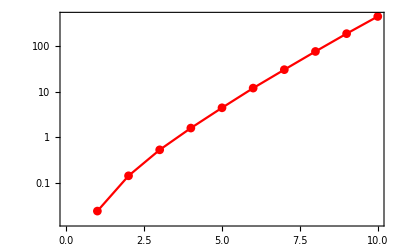

```mathematica
timesplot=ListLogPlot[times,PlotStyle->Hue[0],Frame->True,Axes->False,Joined->True,PlotMarkers->Automatic]
```

This is the list of the lengths of each perturbative expression

```mathematica
lengths=Length/@Expand[{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10}]
```

0.827049

{6,30,96,264,672,1632,3840,8832,19968,44544}

We also plot then in a logaritmic plot

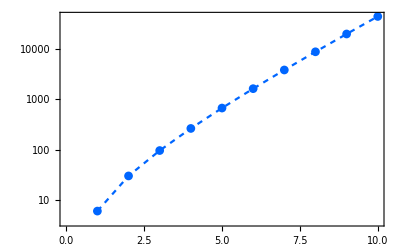

```mathematica
lengthsplot=ListLogPlot[lengths,PlotStyle->{Hue[0.6],Dashing[{0.01,0.01}]},Frame->True,Axes->False,Joined->True,PlotMarkers->Automatic,PlotStyle->Blue]
```

### 7.2. Timings with the Leibnitz rule

We now apply Perturbation on products of different numbers of objects. We then graphically represent the time it takes for the expression to be expanded versus the perturbative order and the number of factors in the product. The n-th order perturbation of the Leibnitz rule is implemented in the context of xPert` through a closed formula. We will see that this is faster than the chain rule, that is implemented essentialy via the Mathematica command Dt.

Driver to average a number of experiments. For timings below a second the computation is repeated a number of times:

```mathematica
average[lists_List]:=Plus@@lists/Length[lists];
threshold=1;
experiment[number_Integer,order_Integer]:=Module[{timing=experiment1[number,order],repeat},
If[timing[[1]]<threshold,
repeat=Max[1,Ceiling[threshold/timing[[1]]]];
average@Table[experiment1[number,order],{repeat}],
timing]
];
```

Generate products of n>1 arguments:

```mathematica
Table[prod[n]=Times@@Table[Unique["x"],{n}],{n,1,10}];
```

and measure the time Perturbation takes to act on them, and the number of terms produced:

```mathematica
experiment1[number_,1]:=AbsoluteTiming[Length@Expand@Perturbation[prod[number]]];
experiment1[number_,order_]:=AbsoluteTiming[Length@Expand@Perturbation[prod[number],order]];
```

```mathematica
Llist[1]=experiment[#,1]&/@Range[2,10]
```

8.10531

{{0.0000568355,2},{0.0000896927,3},{0.000135001,4},{0.000178347,5},{0.000227432,6},{0.000319771,7},{0.000404375,8},{0.00047046,9},{0.00061004,10}}

```mathematica
Llist[2]=experiment[#,2]&/@Range[2,10]
```

8.55383

{{0.0000784957,3},{0.000170098,6},{0.000297317,10},{0.000484202,15},{0.000739437,21},{0.00103357,28},{0.00151017,36},{0.00197774,45},{0.00282992,55}}

```mathematica
Llist[3]=experiment[#,3]&/@Range[2,10]
```

8.36075

{{0.00010108,4},{0.000288142,10},{0.000648373,20},{0.00122394,35},{0.00204942,56},{0.0031594,84},{0.0049931,120},{0.00737903,165},{0.0103541,220}}

```mathematica
Llist[4]=experiment[#,4]&/@Range[2,10]
```

8.76363

{{0.00012451,5},{0.000391496,15},{0.001003,35},{0.0024109,70},{0.00519854,126},{0.00936811,210},{0.0152636,330},{0.0249281,495},{0.0393186,715}}

```mathematica
Llist[5]=experiment[#,5]&/@Range[2,10]
```

8.70045

{{0.000159919,6},{0.0006223,21},{0.00179097,56},{0.00465088,126},{0.010339,252},{0.0204441,462},{0.0380385,792},{0.0667974,1287},{0.107271,2002}}

```mathematica
Llist[6]=experiment[#,6]&/@Range[2,10]
```

9.07617

{{0.000170574,7},{0.000807338,28},{0.0027236,84},{0.00707061,210},{0.0180096,462},{0.0393467,924},{0.0798135,1716},{0.144885,3003},{0.257061,5005}}

```mathematica
Llist[7]=experiment[#,7]&/@Range[2,10]
```

10.0298

{{0.000181814,8},{0.000940073,36},{0.0036498,120},{0.011416,330},{0.0302331,792},{0.0737375,1716},{0.162235,3432},{0.318009,6435},{0.593889,11440}}

```mathematica
Llist[8]=experiment[#,8]&/@Range[2,10]
```

10.9808

{{0.000200934,9},{0.00116682,45},{0.00509925,165},{0.0171434,495},{0.0518655,1287},{0.139692,3003},{0.318786,6435},{0.665588,12870},{1.38907,24310}}

```mathematica
Llist[9]=experiment[#,9]&/@Range[2,10]
```

12.1912

{{0.000231359,10},{0.00148242,55},{0.0069748,220},{0.0253987,715},{0.0813231,2002},{0.226835,5005},{0.568945,11440},{1.29245,24310},{2.88409,48620}}

```mathematica
Llist[10]=experiment[#,10]&/@Range[2,10]
```

15.3407

{{0.000245658,11},{0.00171861,66},{0.0089789,286},{0.0354913,1001},{0.120266,3003},{0.367617,8008},{1.03501,19448},{2.51875,43758},{5.64732,92378}}

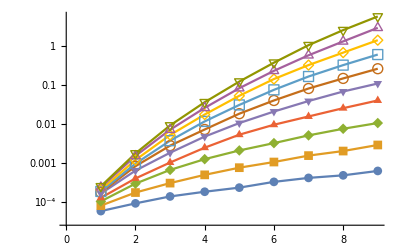

```mathematica
Ltimingsplot=ListLogPlot[Map[First,Array[Llist,{10}],{2}],Joined->True,PlotMarkers->Automatic]
```

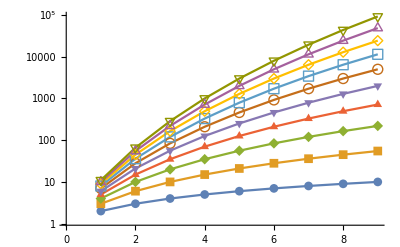

```mathematica
Ltermsplot=ListLogPlot[Map[Last,Array[Llist,{10}],{2}],Joined->True,PlotMarkers->Automatic]
```

### 7.3. Timings with the chain rule

In this section we measure the time it takes to the command Perturbation to act on a scalar function of up to 8 arguments through the chain rule. We analize it up to the fifth perturbative order. In the context of xPert`, we have implemented the nth order perturbation of the chain rule trough the Mathematica command Dt.

Generate functions of n arguments and perturb them:

```mathematica
Table[func[n]=F@@Table[Unique["x"],{n}],{n,1,5}];
```

```mathematica
experiment1[number_,1]:=AbsoluteTiming[Length@Expand@NoScalar@Perturbation[func[number]]];
experiment1[number_,order_]:=AbsoluteTiming[Length@NoScalar@Expand@Perturbation[func[number],order]];
```

```mathematica
Flist[1]=experiment1[#,2]&/@Range[10]
```

{{0.000643,2},{0.00094,5},{0.001691,9},{0.002091,14},{0.002691,20},{0.003643,27},{0.004496,35},{0.005463,44},{0.006567,54},{0.008377,65}}

The first case is a product of two objects and hence its length must be corrected:

```mathematica
Flist[1]=ReplacePart[Flist[1],1,{1,2}]
```

{{0.000643,1},{0.00094,5},{0.001691,9},{0.002091,14},{0.002691,20},{0.003643,27},{0.004496,35},{0.005463,44},{0.006567,54},{0.008377,65}}

```mathematica
Flist[2]=experiment1[#,2]&/@Range[10]
```

{{0.000851,2},{0.001304,5},{0.001893,9},{0.002487,14},{0.003071,20},{0.003635,27},{0.004647,35},{0.005388,44},{0.006832,54},{0.00821,65}}

```mathematica
Flist[3]=experiment1[#,3]&/@Range[10]
```

0.220394

{{0.000878,3},{0.001996,10},{0.005007,22},{0.008346,40},{0.011845,65},{0.017405,98},{0.026651,140},{0.035967,192},{0.047944,255},{0.064206,330}}

```mathematica
Flist[4]=experiment1[#,4]&/@Range[7]
```

1.46002

{{0.001927,5},{0.005766,20},{0.017501,51},{0.046449,105},{0.140178,190},{0.351955,315},{0.895502,490}}

```mathematica
Flist[5]=experiment1[#,5]&/@Range[5]
```

1.56413

{{0.002326,7},{0.01331,36},{0.069967,108},{0.297026,252},{1.18052,506}}

```mathematica
Flist[6]=experiment1[#,6]&/@Range[4]
```

2.43551

{{0.003376,11},{0.034028,65},{0.28556,221},{2.11268,574}}

```mathematica
Flist[7]=experiment1[#,7]&/@Range[4]
```

16.1761

{{0.005029,15},{0.092223,110},{1.29868,429},{14.7714,1240}}

```mathematica
Flist[8]=experiment1[#,8]&/@Range[3]
```

7.08356

{{0.010048,22},{0.291801,185},{6.77878,810}}

```mathematica
Flist[9]=experiment1[#,9]&/@Range[3]
```

36.1076

{{0.012089,30},{0.878127,300},{35.202,1479}}

```mathematica
Flist[10]=experiment1[#,9]&/@Range[3]
```

35.3461

{{0.015731,30},{0.981088,300},{34.3325,1479}}

```mathematica
MaxMemoryUsed[]
```

457024944

Graphs:

```mathematica
tlist=Transpose[PadRight[Array[Flist,10],{10,10},Null]]/.Null->Nothing;
```

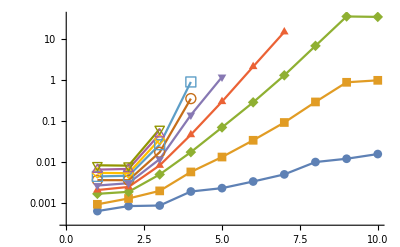

```mathematica
ListLogPlot[Map[First,tlist,{2}],Joined->True,PlotMarkers->Automatic]
```

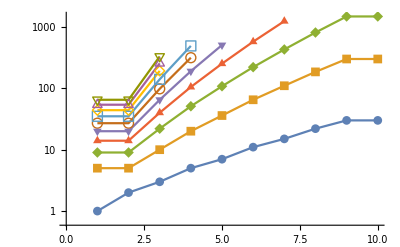

```mathematica
ListLogPlot[Map[Last,tlist,{2}],Joined->True,PlotMarkers->Automatic]
```

## 8. Final comments

Note: For further information about xPert`, and to be kept informed about new releases, you may contact the authors at david.brizuela@ehu.eus, jose@xact.es or mena@iem.cfmac.csic.es. Suggestions and comments are welcome and very much appreciated!
This is xPertDoc.nb, the docfile of xPert`, currently in version 1.0.6.	Last update February 28, 2018.